## Analytic Results

### Key analytic results as stated in paper

```mathematica
Sz[βz_,mx_,my_]:=Exp[-(βz/(mx+my))];

Sp[βp_,m_]:=Exp[-(βp/m)];

Eq5=(βz*mx-(mx+my)^2)/(mx(mx+my)^2);
Eq6=(βz*my-(mx+my)^2)/(my(mx+my)^2);

Eq7=(βp-m)/m^2;

Eq8a=(my(Exp[βp/my]-Exp[βz/(mx+my)]))/(2my*Exp[βp/my]-(mx+my)Exp[βz/(mx+my)]);
Eq8b=1;

Eq9=((βz*mx-(mx+my)^2)(my*Exp[βp/my]-mx*Exp[βz/(mx+my)]))/(mx(mx+my)^2(2my*Exp[βp/my]-(mx+my)Exp[βz/(mx+my)]));
Eq10=1/(my^2(mx+my)^2)((my^2 Exp[βp/my](βz*my-(mx+my)^2)+Exp[βz/(mx+my)]((mx+my)^2(βp*mx+my^2-βp*my)-βz*mx*my^2))/(2my*Exp[βp/my]-(mx+my)Exp[βz/(mx+my)]));

Eq11=(βz*my)/(mx+my)+my*Log[mx/my];
Eq12=(βz*mx)/(mx+my);

(* ... For equations A11-A16 we will assume that y is the microgamete and employ the logic in Appendix D*)

EqA11=Nx;
EqA12=Ny/(Ny+Nyh)*Nx;
EqA13=Nyh/(Ny+Nyh)*Nx;
EqA14=0;
EqA15=Ny/(Ny+Nyh)*(Ny+Nyh-Nx);
EqA16=Nyh/(Ny+Nyh)*(Ny+Nyh-Nx);


EqA25=FY*Sz[βz,mx,my]+FYh*Sz[βz,mx,myh]+HX*Sp[βp,mx];
EqA26=FY*Sz[βz,mx,my]+HY*Sp[βp,my];
EqA27=FYh*Sz[βz,mx,myh]+HYh*Sp[βp,myh];


EqA29=(wy+wyh)/(wx+wy+wyh);

EqA30=wyh/(wy+wyh);

EqA40=δm(fyh(1-fyh))/(my^2(mx+my)^2((my-fs(mx+my))Exp[βz/(mx+my)]+my(fs-1)Exp[βp/my]))*(my^2(1-fs)((mx+my)^2-βz*my)Exp[βp/my]-(mx+my)^2(my(1-fs)-mx*fs)(my-βp)Exp[βz/(mx+my)]);

EqA41=δm*fxh(1-fxh)(βz/(mx+my)^2-1/mx);

EqA53=((fb*A)/(ma+δm)Exp[-βp/(ma+δm)])/((fb*A)/(ma+δm)Exp[-βp/(ma+δm)]+((1-fb)*A)/ma Exp[-βp/ma]);
```

### Algebraic manipulations that verify results in paper

```mathematica
(* DERIVATION OF Eq.(6) *)

(* ... begin by evaluating equation 30, noting that in the limit of Eq.(5) [i.e. βp->∞], HX=HY=HYh=0 ... *)
(EqA30/.{wx->EqA25,wy->EqA26,wyh->EqA27})/.{FX->EqA11,FY->EqA12,FYh->EqA13,HX->0,HY->0,HYh->0}//FullSimplify;

(* ... rewrite Nx, Ny and Nyh in terms of fs, and f ...*)
%/.{Nx->(1-fs)A/mx,Ny->fs(1-fyh)A/my,Nyh->fs*fyh A/myh};

(* ... note that in this βp->∞ limit, 1:1 sex ratios + maintained ... *)
%/.fs->1/2;

(* ... sub myh=my+δm ... *)
%/.myh->my+δm;

(* ... execute Eq.(A39) to obtain special βp->∞ case of Eq.(A40) ... *)
δm*(D[%,δm]/.δm->0)//FullSimplify;

(* ... execute Eq.(A43) to obtain special βp->∞ case in Eq.(6) ... *)
1/δm*(D[%,fyh]/.fyh->0);

(* ... show equivalence with Eq.(6) ... *)
Eq6-%//FullSimplify
```

0

```mathematica
(* DERIVATION OF Eq.(5) *)

(* ... begin by evaluating similar equation to 30 (see above derivation for Eq.(6)), noting that in the limit of Eq.(5) [i.e. βp->∞], HX=HY=HYh=0 ... *)
(wxh/(wx+wxh)/.{wx->FX*Sz[βz,mx,my]+HX*Sp[βp,mx],wxh->FXh*Sz[βz,mxh,my]+HXh*Sp[βp,mxh],wy->FX*Sz[βz,mx,my]+FXh*Sz[βz,mxh,my]+HY*Sp[βp,my]})/.{FX->Nx/(Nx+Nxh)(Nx+Nxh),FXh->Nxh/(Nx+Nxh)(Nx+Nxh),FY->Nx+Nxh,HX->0,HY->0,HXh->0}//FullSimplify;

(* ... rewrite Nx, Ny and Nyh in terms of fs, and f ...*)
%/.{Nx->(1-fs)(1-fxh)A/mx,Nxh->(1-fs)fxh A/mxh,Ny->fs A/my};

(* ... note that in this βp->∞ limit, 1:1 sex ratios + maintained ... *)
%/.fs->1/2;

(* ... sub myh=my+δm ... *)
%/.mxh->mx+δm;

(* ... execute Eq.(A39) to obtain special βp->∞ case of Eq.(A40) ... *)
δm*(D[%,δm]/.δm->0)//FullSimplify;

(* ... execute Eq.(A43) to obtain special βp->∞ case in Eq.(5) ... *)
1/δm*(D[%,fxh]/.fxh->0);

(* ... show equivalence with Eq.(5) ... *)
Eq5-%//FullSimplify
```

0

```mathematica
(* DERIVATION OF Eq.(7) *)

(* ... execute Eq.(A51) ... *)
δm*(D[EqA53,δm]/.δm->0)//FullSimplify;

(* ... execute Eq.(A50) ... *)
1/δm D[%,fb]/.fb->0//FullSimplify;

(* ... show equivalence with Eq.(7) ... *)
Eq7- %/.{ma->m}//FullSimplify
```

0

```mathematica
(* DERIVATION OF Eq.(8) *)

(* ... begin by evaluating equation 29 (sex ratio) with no mutants and subbing in Eqs.(A35-A37) ... *)
(EqA29/.wyh->0/.{wx->EqA25,wy->EqA26,wyh->EqA27})/.{FX->(1-fs)(A*M)/mx,FY->(1-fs)(A*M)/mx,FYh->0,HX->0,HY->fs*(A*M)/my-(1-fs)(A*M)/mx}//FullSimplify;

(* ... solve Eq.(A34) for fs ... *)
fs/.Reverse[Solve[%==fs,fs]]; 

(* ... show equivalence with Eq.(8) ... *)
{Eq8a,Eq8b}-%//FullSimplify
```

{0,0}

```mathematica
(* DERIVATION OF Eq.(10) *)

(* ... similar to derivation of Eq.(6); begin by evaluating equation 30 ... *)
(EqA30/.{wx->EqA25,wy->EqA26,wyh->EqA27})/.{FX->EqA11,FY->EqA12,FYh->EqA13,HX->EqA14,HY->EqA15,HYh->EqA16}//FullSimplify;

(* ... rewrite Nx, Ny and Nyh in terms of fs, and f ...*)
%/.{Nx->(1-fs)A/mx,Ny->fs(1-fyh)A/my,Nyh->fs*fyh A/myh};

(* ... sub myh=my+δm ... *)
%/.myh->my+δm;

(* ... execute Eq.(A39) to obtain Eq.(A40) ... *)
δm*(D[%,δm]/.δm->0)//FullSimplify;

(* ... show equivalence with Eq.(A40) ... *)
EqA40-%//FullSimplify;

(* ... execute Eq.(A43) to obtain Eq.(10) (almost) ... *)
fs*1/δm*(D[EqA40,fyh]/.fyh->0);

(* ... sub for fs from Eq(8a) ... *)
%/.fs->Eq8a//FullSimplify;


(* ... show equivalence with Eq.(10) ... *)
Eq10-%//FullSimplify
```

0

```mathematica
(* DERIVATION OF Eq.(9) *)

(* ... begin by evaluating similar equation to 30 (see above derivation for Eq.(10)), ... *)
(wxh/(wx+wxh)/.{wx->FX*Sz[βz,mx,my]+HX*Sp[βp,mx],wxh->FXh*Sz[βz,mxh,my]+HXh*Sp[βp,mxh],wy->FX*Sz[βz,mx,my]+FXh*Sz[βz,mxh,my]+HY*Sp[βp,my]})/.{FX->Nx/(Nx+Nxh)(Nx+Nxh),FXh->Nxh/(Nx+Nxh)(Nx+Nxh),FY->Nx+Nxh,HX->0,HXh->0,HY->Ny-(Nx+NXh)}//FullSimplify;

(* ... rewrite Nx, Ny and Nyh in terms of fs, and f ...*)
%/.{Nx->(1-fs)(1-fxh)A/mx,Nxh->(1-fs)fxh A/mxh,Ny->fs A/my};

(* ... sub myh=my+δm ... *)
%/.mxh->mx+δm;

(* ... execute Eq.(A39) to obtain Eq.(A41) ... *)
δm*(D[%,δm]/.δm->0)//FullSimplify;

(* ... execute Eq.(A45) to obtain special βp->∞ case in Eq.(5) ... *)
(1-fs)1/δm*(D[%,fxh]/.fxh->0);

(* ... sub for fs from Eq(8a) ... *)
%/.fs->Eq8a//FullSimplify;

(* ... show equivalence with Eq.(9) ... *)
Eq9-%//FullSimplify
```

0

```mathematica
(* DERIVATION OF Eq.(11) *)

(* ... begin by deriving Eq.(46) ... *)
wa/(wx+wy+wa)/.{wx->Nx*Sz[βz,mx,my]+0*Sp[βp,mx],wy->Nx*Sz[βz,mx,my]+(Ny-Nx)*Sp[βp,my],wa->Na*Sp[βp,ma]}//FullSimplify;

(* ... evalutate using Eqs.(A47-A49) ... *)
%/.{Nx->(1-fs)(1-fa)(A*M)/mx,Ny->fs(1-fa)(A*M)/my,Na->fa*(A*M)/ma};

(* ... sub for fs from Eq(8a) ... *)
%/.fs->Eq8a//FullSimplify;

(* ... assume asexual mutant is derived microgamete y ... *)
%/.ma->my//FullSimplify;

(* ... solve = fa for βp *)
Solve[%==fa,βp]/.C[1]->0//FullSimplify;

Eq11-βp/.%[[1]]//FullSimplify
```

0

```mathematica
(* DERIVATION OF Eq.(12) *)

(* ... begin by deriving Eq.(46) ... *)
wa/(wx+wy+wa)/.{wx->Nx*Sz[βz,mx,my]+0*Sp[βp,mx],wy->Nx*Sz[βz,mx,my]+(Ny-Nx)*Sp[βp,my],wa->Na*Sp[βp,ma]}//FullSimplify;

(* ... evalutate using Eqs.(A47-A49) ... *)
%/.{Nx->(1-fs)(1-fa)(A*M)/mx,Ny->fs(1-fa)(A*M)/my,Na->fa*(A*M)/ma};

(* ... sub for fs from Eq(8a) ... *)
%/.fs->Eq8a//FullSimplify;

(* ... assume asexual mutant is derived macrogamete x ... *)
%/.ma->mx//FullSimplify;

(* ... solve = fa for βp *)
Solve[%==fa,βp]/.C[1]->0//FullSimplify;

Eq12-βp/.%[[1]]//FullSimplify
```

0

## Simulations

### Define functions for simulations

```mathematica
(* Fertilisation Functions *)

F[ϕ_,NX_,NY_]:=Min[{NX,NY}];
Hx[ϕ_,NX_,NY_]:=Max[{NX-NY,0}];
Hy[ϕ_,NX_,NY_]:=Max[{NY-NX,0}];

Sz[βz_,mx_,my_]:=Exp[-(βz/(mx+my))];

Sz[βp_,m_]:=Exp[-(βp/m)];

(* Absolute Fitness Functions for use in numerical schemes to calculate invasion trajectories over a discrete number of generations *)

WTotRelXMutAna[fx_,fxh_,fy_]=({Wx/(Wx+Wxh+Wy),Wxh/(Wx+Wxh+Wy),Wy/(Wx+Wxh+Wy)}/.{
Wx->Nx/(Nx+Nxh)(F[ϕ,Nx+Nxh,Ny]*Sz[βz,mx,my]+Hx[ϕ,Nx+Nxh,Ny]*Sz[βp,mx]),
Wxh->Nxh/(Nx+Nxh)(F[ϕ,Nx+Nxh,Ny]*Sz[βz,mxh,my]+Hx[ϕ,Nx+Nxh,Ny]*Sz[βp,mxh]),
Wy->(Nx/(Nx+Nxh)F[ϕ,Nx+Nxh,Ny]*Sz[βz,mx,my]+Nxh/(Nx+Nxh)F[ϕ,Nx+Nxh,Ny]*Sz[βz,mxh,my]+Hy[ϕ,Nx+Nxh,Ny]*Sz[βp,my])

}/.{Nx->A*fx M/mx,Nxh->A*fxh M/mxh,Ny->A*fy M/my}/.mxh->mx+δm);

WTotRelYMutAna[fx_,fy_,fyh_]=({Wx/(Wx+Wy+Wyh),Wy/(Wx+Wy+Wyh),Wyh/(Wx+Wy+Wyh)}/.{
Wx->(Ny/(Ny+Nyh)F[ϕ,Nx,Ny+Nyh]*Sz[βz,mx,my]+Nyh/(Ny+Nyh)F[ϕ,Nx,Ny+Nyh]*Sz[βz,mx,myh]+Hx[ϕ,Nx,Ny+Nyh]*Sz[βp,mx]),
Wy->Ny/(Ny+Nyh)(F[ϕ,Nx,Ny+Nyh]*Sz[βz,mx,my]+Hy[ϕ,Nx,Ny+Nyh]*Sz[βp,my]),
Wyh->Nyh/(Ny+Nyh)(F[ϕ,Nx,Ny+Nyh]*Sz[βz,mx,myh]+Hy[ϕ,Nx,Ny+Nyh]*Sz[βp,myh])
}/.{Nx->A*fx M/mx,Ny->A*fy M/my,Nyh->A*fyh M/myh}/.myh->my+δm);

(* Invasion Functions - full loop (no approximations) over generations to test whether mutant x or y type can invade *)
(* fs in the initial sex ratio (which can vary over course of invasion) *)
(* f0 initial frequency of x or y mutant with respect to resident (Nxh/(Nxh+Nx) or Nyh/(Nyh+Ny)) *)
(* simulations run until either: (i) the mutant falls below its initial frequncy; (ii) the resident drops below the mutants initial frequency (it's displaced); (iii) the sex ratio approachs 1 (microgametes take over); or (iv) maxGen is exceeded (the invasion is taking too long) *)


invTrajXMut[mParams_,params_]:=Module[{mPar=mParams,par=params,trajFXXHY,i},
trajFXXHY=Table[{i,0,0,0},{i,1,maxGen/.par}];
trajFXXHY[[1,2;;]]={(1-fs)(1-f0),(1-fs)*f0,fs}/.par/.mPar;
i=2;
While[(trajFXXHY[[i-1,2]]/(trajFXXHY[[i-1,2]]+trajFXXHY[[i-1,3]])≥(f0/.par))&&(trajFXXHY[[i-1,3]]/(trajFXXHY[[i-1,2]]+trajFXXHY[[i-1,3]])≥(f0/.par))&&i≤maxGen/.par,
trajFXXHY[[i,2;;]]=WTotRelXMutAna[trajFXXHY[[i-1,2]],trajFXXHY[[i-1,3]],trajFXXHY[[i-1,4]]]/.mPar/.par;
i++;
];
trajFXXHY=Drop[trajFXXHY,-(maxGen-i+1/.par)];
Return[trajFXXHY];
];

invTrajYMut[mParams_,params_]:=Module[{mPar=mParams,par=params,trajFXYYH,i},
trajFXYYH=Table[{i,0,0,0},{i,1,maxGen/.par}];
trajFXYYH[[1,2;;]]={(1-fs),fs(1-f0),fs*f0}/.par/.mPar;
i=2;
While[(trajFXYYH[[i-1,3]]/(trajFXYYH[[i-1,3]]+trajFXYYH[[i-1,4]])≥(f0/.par))&&(trajFXYYH[[i-1,4]]/(trajFXYYH[[i-1,3]]+trajFXYYH[[i-1,4]])≥(f0/.par))&&i≤maxGen/.par,
trajFXYYH[[i,2;;]]=WTotRelYMutAna[trajFXYYH[[i-1,2]],trajFXYYH[[i-1,3]],trajFXYYH[[i-1,4]]]/.mPar/.par;
i++;
];
trajFXYYH=Drop[trajFXYYH,-(maxGen-i+1/.par)];
Return[trajFXYYH];
];

(* Invasion Functions - continuous ODE approximation (see Eqs.(A40-A41)) *)

invODETrajXMut1D[mParams_,params_]:=Module[{mPar=mParams,par=params,nSol},
nSol=NDSolve[{
fxh'[t]==(EqA41/.par/.mPar/.fxh->fxh[t]),
fxh[0]==f0/.par/.mPar
},{fxh[t]},{t,0,maxGen/.par}];
Return[nSol];
];

invODETrajYMut1D[mParams_,params_]:=Module[{mPar=mParams,par=params,nSol},
nSol=NDSolve[{
fyh'[t]==(EqA40/.par/.mPar/.fyh->fyh[t]),
fyh[0]==f0/.par/.mPar},{fyh[t]},{t,0,maxGen/.par}];
Return[nSol];
];
```

### Illustrate invasion dynamics + continuous ODE approximation

{fs→0.50514,δm→-0.01,mx→0.4,my→0.1}

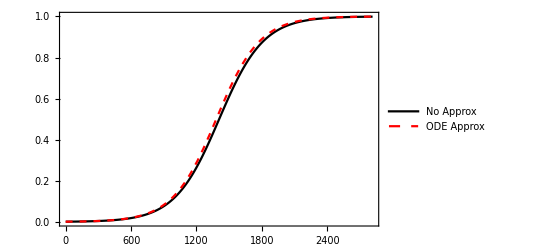

```mathematica
(* Mutant macrogamete x *)

params={ϕ->100,βz->0.5,βp->0.6,A->1000,M->1,f0->10^-3,maxGen->10000};
mParams={fs->0,δm->-0.01,mx->0.4,my->0.1};
(* Assume resident population initially at equilibrium sex ratio given by *)
mParams[[1]]=fs->Eq8a/.params/.mParams[[2;;]];
mParams

exTrajXMut=invTrajXMut[mParams,params];
exTrajXMutODE1D=invODETrajXMut1D[mParams,params];

Show[
ListLinePlot[Table[{exTrajXMut[[i ,1]],exTrajXMut[[i ,3]]/(exTrajXMut[[i ,2]]+exTrajXMut[[i ,3]])},{i,1,Length[exTrajXMut]}],PlotStyle->Black,Frame->True,PlotRange->{{0,Length[exTrajXMut]},{0,1}},PlotLegends->{"No Approx"}],
Plot[Evaluate[fxh[t]/.exTrajXMutODE1D],{t,0,Length[exTrajXMut]},PlotStyle->{Red,Dashed},PlotRange->All,PlotLegends->{"ODE Approx"}]
]
```

{fs→0.50514,δm→-0.005,mx→0.4,my→0.1}

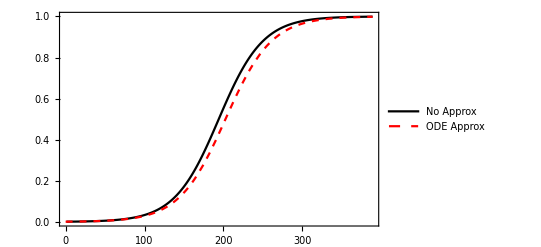

```mathematica
(* Mutant microgamete y *)

params={ϕ->100,βz->0.5,βp->0.6,A->1000,M->1,f0->10^-3,maxGen->10000};
mParams={fs->0,δm->-0.005,mx->0.4,my->0.1};
(* Assume resident population initially at equilibrium sex ratio given by *)
mParams[[1]]=fs->Eq8a/.params/.mParams[[2;;]];
mParams

exTrajYMut=invTrajYMut[mParams,params];
exTrajYMutODE1D=invODETrajYMut1D[mParams,params];

Show[
ListLinePlot[Table[{exTrajYMut[[i ,1]],exTrajYMut[[i ,4]]/(exTrajYMut[[i ,3]]+exTrajYMut[[i ,4]])},{i,1,Length[exTrajYMut]}],PlotStyle->Black,Frame->True,PlotRange->{{0,Length[exTrajYMut]},{0,1}},PlotLegends->{"No Approx"}],
Plot[Evaluate[fyh[t]/.exTrajYMutODE1D],{t,0,Length[exTrajYMut]},PlotStyle->{Red,Dashed},PlotRange->All,PlotLegends->{"ODE Approx"}]
]
```

### Data for trajectories in Figure 2

#### Panel A

```mathematica
panelAevoTraj1={{1,2,2,0.5},{2,1.98,2,0.5050525590220163},{3,1.98,1.98,0.5000513695517165},{4,1.98,1.98,0.4999833086692036},{5,1.96,1.98,0.5050411189584767},{6,1.96,1.98,0.5050762107209524},{7,1.96,1.98,0.5051095827870741},{8,1.96,1.98,0.5050762107209524},{9,1.94,1.98,0.5101742205208404},{10,1.92,1.98,0.5153455988205708},{11,1.92,1.96,0.5102536493909805},{12,1.92,1.94,0.5051205446078242},{13,1.92,1.92,0.50005102713243},{14,1.9,1.92,0.5050054591936713},{15,1.9,1.92,0.5050738228731282},{16,1.9,1.9,0.5000509131110267},{17,1.88,1.9,0.5049931042544347},{18,1.8599999999999999,1.9,0.5100721936592748},{19,1.8599999999999999,1.9,0.5101406573531564},{20,1.8599999999999999,1.88,0.5050827223352762},{21,1.8399999999999999,1.88,0.5100454158894174},{22,1.8399999999999999,1.88,0.5100794988382278},{23,1.8399999999999999,1.88,0.510113827174066},{24,1.8399999999999999,1.8599999999999999,0.5050696185814749},{25,1.8199999999999998,1.8599999999999999,0.5100180992450758},{26,1.8199999999999998,1.8599999999999999,0.510051929785699},{27,1.8199999999999998,1.8599999999999999,0.5100864581290806},{28,1.8199999999999998,1.8399999999999999,0.5050562544136942},{29,1.8199999999999998,1.8199999999999998,0.5000504594515038},{30,1.7999999999999998,1.8199999999999998,0.504941152280067},{31,1.7999999999999998,1.8199999999999998,0.5049743755607693},{32,1.7799999999999998,1.8199999999999998,0.5099617835112993},{33,1.7799999999999998,1.8199999999999998,0.5100300377232984},{34,1.7799999999999998,1.8199999999999998,0.5100300377232984},{35,1.7799999999999998,1.8199999999999998,0.5099951053672565},{36,1.7799999999999998,1.8199999999999998,0.5099951053672565},{37,1.7799999999999998,1.8199999999999998,0.5099951053672565},{38,1.7599999999999998,1.8199999999999998,0.5150083151375968},{39,1.7599999999999998,1.8199999999999998,0.5150771764261195},{40,1.7399999999999998,1.8199999999999998,0.5200791209863714},{41,1.7199999999999998,1.8199999999999998,0.5251714240249415},{42,1.7199999999999998,1.7999999999999998,0.5201171617641587},{43,1.7199999999999998,1.7999999999999998,0.5200830999865139},{44,1.7199999999999998,1.7799999999999998,0.5150173200018516},{45,1.7199999999999998,1.7799999999999998,0.514983828764366},{46,1.7199999999999998,1.7799999999999998,0.514983828764366},{47,1.7199999999999998,1.7799999999999998,0.514983828764366},{48,1.7199999999999998,1.7599999999999998,0.5099738706581824},{49,1.7199999999999998,1.7399999999999998,0.5049852437080783},{50,1.7199999999999998,1.7399999999999998,0.5049528550925488},{51,1.7199999999999998,1.7199999999999998,0.5000494187461036},{52,1.7199999999999998,1.6999999999999997,0.49513009474146535},{53,1.7199999999999998,1.6999999999999997,0.49509806738521256},{54,1.7199999999999998,1.6999999999999997,0.49509806738521256},{55,1.7199999999999998,1.6999999999999997,0.49509806738521256},{56,1.6999999999999997,1.6999999999999997,0.4999506931431994},{57,1.6999999999999997,1.6999999999999997,0.5000181591293709},{58,1.6799999999999997,1.6999999999999997,0.504854724063054},{59,1.6799999999999997,1.6799999999999997,0.5000491961085605},{60,1.6799999999999997,1.6799999999999997,0.4999817298611443},{61,1.6599999999999997,1.6799999999999997,0.5048397009918506},{62,1.6599999999999997,1.6599999999999997,0.5000490866552344},{63,1.6599999999999997,1.6599999999999997,0.4999816181097966},{64,1.6399999999999997,1.6599999999999997,0.5048238435948001},{65,1.6199999999999997,1.6599999999999997,0.5097113572369162},{66,1.6199999999999997,1.6599999999999997,0.5097791993452819},{67,1.6199999999999997,1.6399999999999997,0.5049059079545547},{68,1.5999999999999996,1.6399999999999997,0.5096768751035656},{69,1.5999999999999996,1.6199999999999997,0.5048890848499422},{70,1.5799999999999996,1.6199999999999997,0.5096416068456942},{71,1.5799999999999996,1.6199999999999997,0.509672329328004},{72,1.5799999999999996,1.6199999999999997,0.5097093493012366},{73,1.5799999999999996,1.6199999999999997,0.5097093493012366},{74,1.5599999999999996,1.6199999999999997,0.5144999948369262},{75,1.5599999999999996,1.6199999999999997,0.5145676169608091},{76,1.5399999999999996,1.6199999999999997,0.5193618977271163},{77,1.5199999999999996,1.6199999999999997,0.5242232426459843},{78,1.5199999999999996,1.6199999999999997,0.5242543153047469},{79,1.4999999999999996,1.6199999999999997,0.5290801771027529},{80,1.4799999999999995,1.6199999999999997,0.5339275713888126},{81,1.4799999999999995,1.6199999999999997,0.533958490447904},{82,1.4799999999999995,1.6199999999999997,0.533958490447904},{83,1.4799999999999995,1.6199999999999997,0.5339946989910181},{84,1.4799999999999995,1.5999999999999996,0.5290433203423724},{85,1.4599999999999995,1.5999999999999996,0.5337603350312714},{86,1.4599999999999995,1.5999999999999996,0.5337908816382129},{87,1.4399999999999995,1.5999999999999996,0.5385588385824025},{88,1.4399999999999995,1.5999999999999996,0.5385894869270298},{89,1.4399999999999995,1.5999999999999996,0.5385894869270298},{90,1.4399999999999995,1.5999999999999996,0.5386256307129155},{91,1.4199999999999995,1.5999999999999996,0.5433350103486284},{92,1.4199999999999995,1.5999999999999996,0.5434013075571968},{93,1.4199999999999995,1.5999999999999996,0.5434013075571968},{94,1.4199999999999995,1.5799999999999996,0.538450244749647},{95,1.3999999999999995,1.5799999999999996,0.543090022275094},{96,1.3999999999999995,1.5599999999999996,0.5382382771117803},{97,1.3999999999999995,1.5599999999999996,0.5381706262181748},{98,1.3999999999999995,1.5599999999999996,0.5381706262181748},{99,1.3999999999999995,1.5599999999999996,0.5381706262181748},{100,1.3999999999999995,1.5599999999999996,0.5381706262181748},{101,1.3999999999999995,1.5599999999999996,0.5381706262181748},{102,1.3999999999999995,1.5399999999999996,0.5333308676935635},{103,1.3999999999999995,1.5399999999999996,0.5332634164591938},{104,1.3999999999999995,1.5399999999999996,0.5332634164591938},{105,1.3999999999999995,1.5399999999999996,0.5332634164591938},{106,1.3999999999999995,1.5399999999999996,0.5333002835485431},{107,1.3799999999999994,1.5399999999999996,0.5379240234275957},{108,1.3799999999999994,1.5399999999999996,0.5379534662149916},{109,1.3799999999999994,1.5399999999999996,0.537990064055364},{110,1.3799999999999994,1.5399999999999996,0.5379534662149916},{111,1.3599999999999994,1.5399999999999996,0.5425818605657071},{112,1.3599999999999994,1.5399999999999996,0.5426109892858507},{113,1.3399999999999994,1.5399999999999996,0.5472007426324805},{114,1.3399999999999994,1.5399999999999996,0.5472297111932837},{115,1.3199999999999994,1.5399999999999996,0.5517740482362307},{116,1.3199999999999994,1.5199999999999996,0.5469869032197358},{117,1.3199999999999994,1.4999999999999996,0.5421424175785952},{118,1.3199999999999994,1.4799999999999995,0.5373353124742707},{119,1.2999999999999994,1.4799999999999995,0.5417707332893391},{120,1.2999999999999994,1.4799999999999995,0.5417985402662354},{121,1.2799999999999994,1.4799999999999995,0.5462507067606782},{122,1.2799999999999994,1.4599999999999995,0.5415793594001567},{123,1.2599999999999993,1.4599999999999995,0.5459175407542889},{124,1.2399999999999993,1.4599999999999995,0.5502876029145379},{125,1.2399999999999993,1.4599999999999995,0.550350091953365},{126,1.2399999999999993,1.4599999999999995,0.550350091953365},{127,1.2199999999999993,1.4599999999999995,0.554588222211447},{128,1.2199999999999993,1.4599999999999995,0.5546498495671222},{129,1.2199999999999993,1.4599999999999995,0.5546498495671222},{130,1.2199999999999993,1.4399999999999995,0.5499816595922457},{131,1.2199999999999993,1.4199999999999995,0.5453148975427622},{132,1.1999999999999993,1.4199999999999995,0.5494844226191151},{133,1.1799999999999993,1.4199999999999995,0.5536657193832836},{134,1.1799999999999993,1.3999999999999995,0.5491547665007405},{135,1.1599999999999993,1.3999999999999995,0.5531857036562828},{136,1.1599999999999993,1.3999999999999995,0.5532101007492638},{137,1.1599999999999993,1.3999999999999995,0.5532457453640403},{138,1.1599999999999993,1.3999999999999995,0.5532101007492638},{139,1.1599999999999993,1.3999999999999995,0.5532457453640403},{140,1.1599999999999993,1.3999999999999995,0.5532101007492638},{141,1.1599999999999993,1.3999999999999995,0.5532457453640403},{142,1.1599999999999993,1.3999999999999995,0.5532457453640403},{143,1.1599999999999993,1.3799999999999994,0.5487243696946928},{144,1.1599999999999993,1.3799999999999994,0.5486615695940058},{145,1.1599999999999993,1.3599999999999994,0.544200859460182},{146,1.1599999999999993,1.3399999999999994,0.5397002155493823},{147,1.1399999999999992,1.3399999999999994,0.5437222823675254},{148,1.1199999999999992,1.3399999999999994,0.5477428012292365},{149,1.0999999999999992,1.3399999999999994,0.5516649399096322},{150,1.0999999999999992,1.3199999999999994,0.5473598056676934},{151,1.0999999999999992,1.2999999999999994,0.5429897596785647},{152,1.0999999999999992,1.2799999999999994,0.5386376324601824},{153,1.0999999999999992,1.2799999999999994,0.5385759893151177},{154,1.0999999999999992,1.2799999999999994,0.5385759893151177},{155,1.0999999999999992,1.2799999999999994,0.5385759893151177},{156,1.0999999999999992,1.2799999999999994,0.5385759893151177},{157,1.0799999999999992,1.2799999999999994,0.5424805649643509},{158,1.0799999999999992,1.2599999999999993,0.5382626733681792},{159,1.0799999999999992,1.2599999999999993,0.5382015013892827},{160,1.0799999999999992,1.2399999999999993,0.533976159249546},{161,1.0799999999999992,1.2399999999999993,0.5339150649942298},{162,1.0799999999999992,1.2399999999999993,0.5339531275445031},{163,1.0799999999999992,1.2199999999999993,0.5297030527430366},{164,1.0799999999999992,1.2199999999999993,0.5296415168862846},{165,1.0799999999999992,1.2199999999999993,0.5296415168862846},{166,1.0599999999999992,1.2199999999999993,0.5335598418299866},{167,1.0599999999999992,1.1999999999999993,0.5294175767787441},{168,1.0599999999999992,1.1999999999999993,0.5293564869028695},{169,1.0599999999999992,1.1999999999999993,0.5293564869028695},{170,1.0599999999999992,1.1999999999999993,0.5293952171627782},{171,1.0599999999999992,1.1999999999999993,0.5293564869028695},{172,1.0399999999999991,1.1999999999999993,0.5332163436297488},{173,1.0399999999999991,1.1999999999999993,0.5332363280410031},{174,1.0399999999999991,1.1999999999999993,0.5332744018526303},{175,1.0399999999999991,1.1999999999999993,0.5332363280410031},{176,1.0399999999999991,1.1999999999999993,0.5332744018526303},{177,1.0199999999999991,1.1999999999999993,0.5369897272135334},{178,0.9999999999999991,1.1999999999999993,0.5406463584411225},{179,0.9999999999999991,1.1999999999999993,0.5407017528959874},{180,0.9799999999999991,1.1999999999999993,0.5441751645931897},{181,0.9799999999999991,1.1999999999999993,0.5441932897830861},{182,0.9799999999999991,1.1999999999999993,0.5442290828202064},{183,0.9799999999999991,1.1799999999999993,0.540227723943113},{184,0.9599999999999991,1.1799999999999993,0.543601855985464},{185,0.9599999999999991,1.1799999999999993,0.5436193270188365},{186,0.9599999999999991,1.1799999999999993,0.5436193270188365},{187,0.9399999999999991,1.1799999999999993,0.5469068062082454},{188,0.9399999999999991,1.1799999999999993,0.5469579623351214},{189,0.9399999999999991,1.1799999999999993,0.5469579623351214},{190,0.9399999999999991,1.1799999999999993,0.5469232431957494},{191,0.9399999999999991,1.1799999999999993,0.5469232431957494},{192,0.919999999999999,1.1799999999999993,0.5500545424817759},{193,0.919999999999999,1.1799999999999993,0.5500704281917882},{194,0.899999999999999,1.1799999999999993,0.5530343311878987},{195,0.879999999999999,1.1799999999999993,0.5558332528236941},{196,0.879999999999999,1.1599999999999993,0.5522219482247395},{197,0.859999999999999,1.1599999999999993,0.5548467058475011},{198,0.839999999999999,1.1599999999999993,0.557335409857552},{199,0.839999999999999,1.1599999999999993,0.5573770269184026},{200,0.839999999999999,1.1599999999999993,0.5573770269184026},{201,0.819999999999999,1.1599999999999993,0.5596107420584905},{202,0.819999999999999,1.1399999999999992,0.5562542969773343},{203,0.7999999999999989,1.1399999999999992,0.5583443524683955},{204,0.7999999999999989,1.1199999999999992,0.5550777558950152},{205,0.7999999999999989,1.0999999999999992,0.5517511229716361},{206,0.7999999999999989,1.0799999999999992,0.548417100673634},{207,0.7999999999999989,1.0799999999999992,0.548371099670829},{208,0.7799999999999989,1.0799999999999992,0.5505768697902834},{209,0.7599999999999989,1.0799999999999992,0.5525613354863085},{210,0.7599999999999989,1.0799999999999992,0.5525696268233907},{211,0.7399999999999989,1.0799999999999992,0.5543004064190149},{212,0.7399999999999989,1.0799999999999992,0.5543332286311491},{213,0.7399999999999989,1.0799999999999992,0.5543332286311491},{214,0.7399999999999989,1.0799999999999992,0.5543075768076305},{215,0.7399999999999989,1.0799999999999992,0.5543075768076305},{216,0.7399999999999989,1.0799999999999992,0.5543075768076305},{217,0.7399999999999989,1.0799999999999992,0.5543332286311491},{218,0.7199999999999989,1.0799999999999992,0.5557815557444722},{219,0.6999999999999988,1.0799999999999992,0.5569922991853135},{220,0.6999999999999988,1.0599999999999992,0.5542347757402549},{221,0.6799999999999988,1.0599999999999992,0.5552459520909061},{222,0.6799999999999988,1.0599999999999992,0.5552704399894266},{223,0.6799999999999988,1.0599999999999992,0.555249661380679},{224,0.6599999999999988,1.0599999999999992,0.5560068503056563},{225,0.6599999999999988,1.0599999999999992,0.5560279008624789},{226,0.6599999999999988,1.0599999999999992,0.5560093068172594},{227,0.6399999999999988,1.0599999999999992,0.5564668469807519},{228,0.6399999999999988,1.0599999999999992,0.5564680306826258},{229,0.6399999999999988,1.0599999999999992,0.5564843048370477},{230,0.6399999999999988,1.0599999999999992,0.5564843048370477},{231,0.6199999999999988,1.0599999999999992,0.556616066701702},{232,0.5999999999999988,1.0599999999999992,0.5564458908191472},{233,0.5799999999999987,1.0599999999999992,0.555949356556467},{234,0.5799999999999987,1.0599999999999992,0.5559553354274116},{235,0.5799999999999987,1.0399999999999991,0.5539394979788533},{236,0.5799999999999987,1.0399999999999991,0.5539321441672638},{237,0.5799999999999987,1.0399999999999991,0.5539321441672638},{238,0.5799999999999987,1.0399999999999991,0.5539226736146889},{239,0.5799999999999987,1.0399999999999991,0.5539226736146889},{240,0.5599999999999987,1.0399999999999991,0.5532360539582948},{241,0.5599999999999987,1.0399999999999991,0.5532329829989135},{242,0.5399999999999987,1.0399999999999991,0.5522139850891044},{243,0.5399999999999987,1.0399999999999991,0.5522099946458084},{244,0.5399999999999987,1.0199999999999991,0.5504628154026614},{245,0.5399999999999987,0.9999999999999991,0.5486924350378357},{246,0.5199999999999987,0.9999999999999991,0.5476109026767911},{247,0.5199999999999987,0.9999999999999991,0.5476094492298972},{248,0.5199999999999987,0.9799999999999991,0.5459715546074387},{249,0.5199999999999987,0.9799999999999991,0.5459628336461537},{250,0.5199999999999987,0.9799999999999991,0.5459664013492188},{251,0.49999999999999867,0.9799999999999991,0.5447030963577394},{252,0.47999999999999865,0.9799999999999991,0.5431106326728271},{253,0.47999999999999865,0.9799999999999991,0.5431055918253429},{254,0.47999999999999865,0.9799999999999991,0.5431024670263032},{255,0.47999999999999865,0.9799999999999991,0.5431055918253429},{256,0.47999999999999865,0.9799999999999991,0.5431024670263032},{257,0.47999999999999865,0.9799999999999991,0.5431024670263032},{258,0.47999999999999865,0.9799999999999991,0.5431024670263032},{259,0.47999999999999865,0.9599999999999991,0.5417332193101946},{260,0.45999999999999863,0.9599999999999991,0.5399626954319662},{261,0.45999999999999863,0.9599999999999991,0.5399575976873173},{262,0.4399999999999986,0.9599999999999991,0.5378782259580359},{263,0.4199999999999986,0.9599999999999991,0.5354996905904877},{264,0.4199999999999986,0.9399999999999991,0.5345112540532391},{265,0.4199999999999986,0.919999999999999,0.533527251523385},{266,0.3999999999999986,0.919999999999999,0.5311546620991585},{267,0.37999999999999856,0.919999999999999,0.5285197066789562},{268,0.35999999999999854,0.919999999999999,0.5256743020682816},{269,0.35999999999999854,0.919999999999999,0.5256689291156756},{270,0.35999999999999854,0.899999999999999,0.5250323491674656},{271,0.35999999999999854,0.899999999999999,0.525031396679016},{272,0.3399999999999985,0.899999999999999,0.5221596437534217},{273,0.3399999999999985,0.899999999999999,0.5221551250482115},{274,0.3399999999999985,0.899999999999999,0.5221551250482115},{275,0.3399999999999985,0.899999999999999,0.5221551250482115},{276,0.3399999999999985,0.879999999999999,0.5216207490066509},{277,0.3399999999999985,0.879999999999999,0.5216414606148907},{278,0.3399999999999985,0.879999999999999,0.5216200766003958},{279,0.3399999999999985,0.859999999999999,0.5211006477243276},{280,0.3399999999999985,0.859999999999999,0.5210999759913577},{281,0.3399999999999985,0.859999999999999,0.5210999759913577},{282,0.3199999999999985,0.859999999999999,0.5183241194034416},{283,0.3199999999999985,0.859999999999999,0.5182978657783687},{284,0.3199999999999985,0.859999999999999,0.5182978657783687},{285,0.3199999999999985,0.839999999999999,0.5178765773369003},{286,0.3199999999999985,0.819999999999999,0.5174479676933796},{287,0.3199999999999985,0.819999999999999,0.5174684769013016},{288,0.3199999999999985,0.819999999999999,0.5174475072245491},{289,0.3199999999999985,0.7999999999999989,0.5170119489943376},{290,0.2999999999999985,0.7999999999999989,0.5144624707242544},{291,0.2799999999999985,0.7999999999999989,0.5118691414559725},{292,0.25999999999999845,0.7999999999999989,0.5093432136221763},{293,0.23999999999999846,0.7999999999999989,0.5069788800915674},{294,0.21999999999999847,0.7999999999999989,0.5048737604550061},{295,0.21999999999999847,0.7999999999999989,0.5048511996381473},{296,0.19999999999999848,0.7999999999999989,0.5031160690664425},{297,0.1799999999999985,0.7999999999999989,0.5017687079729307},{298,0.1599999999999985,0.7999999999999989,0.5008514578252673},{299,0.1599999999999985,0.7999999999999989,0.5008411686324346},{300,0.1599999999999985,0.7999999999999989,0.500850703228951},{301,0.13999999999999851,0.7999999999999989,0.500322764660951},{302,0.11999999999999851,0.7999999999999989,0.5000856184415915},{303,0.0999999999999985,0.7999999999999989,0.5000127914104078},{304,0.0799999999999985,0.7999999999999989,0.5000007458009815},{305,0.0799999999999985,0.7999999999999989,0.5000007346437801},{306,0.0799999999999985,0.7999999999999989,0.5000007346437801},{307,0.0599999999999985,0.7999999999999989,0.5000000105830367},{308,0.0599999999999985,0.7999999999999989,0.5000000102803779},{309,0.0599999999999985,0.7999999999999989,0.5000000102803779},{310,0.0599999999999985,0.7999999999999989,0.5000000102803779},{311,0.039999999999998495,0.7999999999999989,0.5000000000459123},{312,0.039999999999998495,0.819999999999999,0.5000000000001198},{313,0.039999999999998495,0.819999999999999,0.5000000000001198},{314,0.039999999999998495,0.839999999999999,0.5000000000001197},{315,0.039999999999998495,0.859999999999999,0.5000000000001196},{316,0.039999999999998495,0.879999999999999,0.5000000000001196},{317,0.039999999999998495,0.879999999999999,0.5000000000001197},{318,0.039999999999998495,0.879999999999999,0.5000000000001197},{319,0.039999999999998495,0.879999999999999,0.5000000000001197},{320,0.039999999999998495,0.899999999999999,0.5000000000001197},{321,0.039999999999998495,0.899999999999999,0.5000000000001196},{322,0.039999999999998495,0.899999999999999,0.5000000000001196},{323,0.039999999999998495,0.899999999999999,0.5000000000001196},{324,0.039999999999998495,0.899999999999999,0.5000000000001196},{325,0.039999999999998495,0.899999999999999,0.5000000000001196},{326,0.039999999999998495,0.899999999999999,0.5000000000001196},{327,0.039999999999998495,0.899999999999999,0.5000000000001196},{328,0.039999999999998495,0.899999999999999,0.5000000000001196},{329,0.039999999999998495,0.899999999999999,0.5000000000405254},{330,0.039999999999998495,0.899999999999999,0.5000000000001196},{331,0.039999999999998495,0.899999999999999,0.5000000000405254},{332,0.039999999999998495,0.899999999999999,0.5000000000001196},{333,0.039999999999998495,0.899999999999999,0.5000000000001196},{334,0.039999999999998495,0.899999999999999,0.5000000000001196},{335,0.039999999999998495,0.899999999999999,0.5000000000001196},{336,0.039999999999998495,0.899999999999999,0.5000000000001196},{337,0.039999999999998495,0.899999999999999,0.5000000000001196},{338,0.039999999999998495,0.899999999999999,0.5000000000001196},{339,0.039999999999998495,0.899999999999999,0.5000000000001196},{340,0.039999999999998495,0.899999999999999,0.5000000000001196},{341,0.039999999999998495,0.899999999999999,0.5000000000001196},{342,0.039999999999998495,0.899999999999999,0.5000000000001196},{343,0.039999999999998495,0.899999999999999,0.5000000000001196},{344,0.039999999999998495,0.899999999999999,0.5000000000001196},{345,0.039999999999998495,0.899999999999999,0.5000000000001196},{346,0.039999999999998495,0.899999999999999,0.5000000000001196},{347,0.039999999999998495,0.899999999999999,0.5000000000001196},{348,0.039999999999998495,0.899999999999999,0.5000000000405254},{349,0.039999999999998495,0.899999999999999,0.5000000000001196},{350,0.039999999999998495,0.899999999999999,0.5000000000001196},{351,0.039999999999998495,0.899999999999999,0.5000000000001196},{352,0.039999999999998495,0.899999999999999,0.5000000000405254},{353,0.039999999999998495,0.899999999999999,0.5000000000001196},{354,0.039999999999998495,0.899999999999999,0.5000000000001196},{355,0.039999999999998495,0.899999999999999,0.5000000000405254},{356,0.039999999999998495,0.899999999999999,0.5000000000405254},{357,0.039999999999998495,0.899999999999999,0.5000000000405254},{358,0.039999999999998495,0.899999999999999,0.5000000000001196},{359,0.039999999999998495,0.899999999999999,0.5000000000001196},{360,0.039999999999998495,0.899999999999999,0.5000000000001196},{361,0.039999999999998495,0.899999999999999,0.5000000000001196},{362,0.039999999999998495,0.899999999999999,0.5000000000405254},{363,0.039999999999998495,0.899999999999999,0.5000000000001196},{364,0.039999999999998495,0.899999999999999,0.5000000000405254},{365,0.039999999999998495,0.899999999999999,0.5000000000405254},{366,0.039999999999998495,0.899999999999999,0.5000000000001196},{367,0.039999999999998495,0.899999999999999,0.5000000000001196},{368,0.039999999999998495,0.899999999999999,0.5000000000001196},{369,0.039999999999998495,0.899999999999999,0.5000000000001196},{370,0.039999999999998495,0.899999999999999,0.5000000000001196},{371,0.039999999999998495,0.899999999999999,0.5000000000405254},{372,0.039999999999998495,0.899999999999999,0.5000000000405254},{373,0.039999999999998495,0.899999999999999,0.5000000000405254},{374,0.039999999999998495,0.899999999999999,0.5000000000001196},{375,0.039999999999998495,0.899999999999999,0.5000000000001196},{376,0.039999999999998495,0.899999999999999,0.5000000000001196},{377,0.039999999999998495,0.899999999999999,0.5000000000001196},{378,0.039999999999998495,0.899999999999999,0.5000000000001196},{379,0.039999999999998495,0.899999999999999,0.5000000000001196},{380,0.039999999999998495,0.899999999999999,0.5000000000001196},{381,0.039999999999998495,0.899999999999999,0.5000000000001196},{382,0.039999999999998495,0.899999999999999,0.5000000000001196},{383,0.039999999999998495,0.899999999999999,0.5000000000001196},{384,0.039999999999998495,0.899999999999999,0.5000000000405254},{385,0.039999999999998495,0.899999999999999,0.5000000000001196},{386,0.039999999999998495,0.899999999999999,0.5000000000405254},{387,0.039999999999998495,0.899999999999999,0.5000000000001196},{388,0.039999999999998495,0.899999999999999,0.5000000000405254},{389,0.039999999999998495,0.899999999999999,0.5000000000405254},{390,0.039999999999998495,0.899999999999999,0.5000000000405254},{391,0.039999999999998495,0.899999999999999,0.5000000000405254},{392,0.039999999999998495,0.899999999999999,0.5000000000405254},{393,0.039999999999998495,0.899999999999999,0.5000000000001196},{394,0.039999999999998495,0.899999999999999,0.5000000000001196},{395,0.039999999999998495,0.899999999999999,0.5000000000405254},{396,0.039999999999998495,0.899999999999999,0.5000000000001196},{397,0.039999999999998495,0.899999999999999,0.5000000000001196},{398,0.039999999999998495,0.899999999999999,0.5000000000001196},{399,0.039999999999998495,0.899999999999999,0.5000000000001196},{400,0.039999999999998495,0.899999999999999,0.5000000000001196},{401,0.039999999999998495,0.899999999999999,0.5000000000001196},{402,0.039999999999998495,0.899999999999999,0.5000000000001196},{403,0.039999999999998495,0.899999999999999,0.5000000000405254},{404,0.039999999999998495,0.899999999999999,0.5000000000405254},{405,0.039999999999998495,0.899999999999999,0.5000000000001196},{406,0.039999999999998495,0.899999999999999,0.5000000000001196},{407,0.039999999999998495,0.899999999999999,0.5000000000405254},{408,0.039999999999998495,0.899999999999999,0.5000000000405254},{409,0.039999999999998495,0.899999999999999,0.5000000000001196},{410,0.039999999999998495,0.899999999999999,0.5000000000001196},{411,0.039999999999998495,0.899999999999999,0.5000000000001196},{412,0.039999999999998495,0.899999999999999,0.5000000000405254},{413,0.039999999999998495,0.899999999999999,0.5000000000405254},{414,0.039999999999998495,0.899999999999999,0.5000000000405254},{415,0.039999999999998495,0.899999999999999,0.5000000000001196},{416,0.039999999999998495,0.899999999999999,0.5000000000001196},{417,0.039999999999998495,0.899999999999999,0.5000000000001196},{418,0.039999999999998495,0.899999999999999,0.5000000000001196},{419,0.039999999999998495,0.899999999999999,0.5000000000001196},{420,0.039999999999998495,0.899999999999999,0.5000000000001196},{421,0.039999999999998495,0.899999999999999,0.5000000000001196},{422,0.039999999999998495,0.899999999999999,0.5000000000001196},{423,0.039999999999998495,0.899999999999999,0.5000000000001196},{424,0.039999999999998495,0.899999999999999,0.5000000000001196},{425,0.039999999999998495,0.899999999999999,0.5000000000001196},{426,0.039999999999998495,0.899999999999999,0.5000000000001196},{427,0.039999999999998495,0.899999999999999,0.5000000000001196},{428,0.039999999999998495,0.899999999999999,0.5000000000001196},{429,0.039999999999998495,0.899999999999999,0.5000000000405254},{430,0.039999999999998495,0.899999999999999,0.5000000000405254},{431,0.039999999999998495,0.899999999999999,0.5000000000405254},{432,0.039999999999998495,0.899999999999999,0.5000000000001196},{433,0.039999999999998495,0.899999999999999,0.5000000000001196},{434,0.039999999999998495,0.899999999999999,0.5000000000001196},{435,0.039999999999998495,0.899999999999999,0.5000000000001196},{436,0.039999999999998495,0.899999999999999,0.5000000000001196},{437,0.039999999999998495,0.899999999999999,0.5000000000405254},{438,0.039999999999998495,0.899999999999999,0.5000000000001196},{439,0.039999999999998495,0.899999999999999,0.5000000000001196},{440,0.039999999999998495,0.899999999999999,0.5000000000405254},{441,0.039999999999998495,0.899999999999999,0.5000000000001196},{442,0.039999999999998495,0.899999999999999,0.5000000000001196},{443,0.039999999999998495,0.899999999999999,0.5000000000001196},{444,0.039999999999998495,0.899999999999999,0.5000000000001196},{445,0.039999999999998495,0.899999999999999,0.5000000000001196},{446,0.039999999999998495,0.899999999999999,0.5000000000405254},{447,0.039999999999998495,0.899999999999999,0.5000000000001196},{448,0.039999999999998495,0.899999999999999,0.5000000000405254},{449,0.039999999999998495,0.899999999999999,0.5000000000405254},{450,0.039999999999998495,0.899999999999999,0.5000000000001196},{451,0.039999999999998495,0.899999999999999,0.5000000000001196},{452,0.039999999999998495,0.899999999999999,0.5000000000001196},{453,0.039999999999998495,0.899999999999999,0.5000000000001196},{454,0.039999999999998495,0.899999999999999,0.5000000000001196},{455,0.039999999999998495,0.899999999999999,0.5000000000001196},{456,0.039999999999998495,0.899999999999999,0.5000000000001196},{457,0.039999999999998495,0.899999999999999,0.5000000000001196},{458,0.039999999999998495,0.899999999999999,0.5000000000001196},{459,0.039999999999998495,0.899999999999999,0.5000000000001196},{460,0.039999999999998495,0.899999999999999,0.5000000000001196},{461,0.039999999999998495,0.899999999999999,0.5000000000001196},{462,0.039999999999998495,0.899999999999999,0.5000000000001196},{463,0.039999999999998495,0.899999999999999,0.5000000000405254},{464,0.039999999999998495,0.899999999999999,0.5000000000001196},{465,0.039999999999998495,0.899999999999999,0.5000000000405254},{466,0.039999999999998495,0.899999999999999,0.5000000000405254},{467,0.039999999999998495,0.899999999999999,0.5000000000001196},{468,0.039999999999998495,0.899999999999999,0.5000000000001196},{469,0.039999999999998495,0.899999999999999,0.5000000000001196},{470,0.039999999999998495,0.899999999999999,0.5000000000001196},{471,0.039999999999998495,0.899999999999999,0.5000000000001196},{472,0.039999999999998495,0.899999999999999,0.5000000000001196},{473,0.039999999999998495,0.899999999999999,0.5000000000001196},{474,0.039999999999998495,0.899999999999999,0.5000000000405254},{475,0.039999999999998495,0.899999999999999,0.5000000000405254},{476,0.039999999999998495,0.899999999999999,0.5000000000001196},{477,0.039999999999998495,0.899999999999999,0.5000000000405254},{478,0.039999999999998495,0.899999999999999,0.5000000000001196},{479,0.039999999999998495,0.899999999999999,0.5000000000001196},{480,0.039999999999998495,0.899999999999999,0.5000000000001196},{481,0.039999999999998495,0.899999999999999,0.5000000000001196},{482,0.039999999999998495,0.899999999999999,0.5000000000405254},{483,0.039999999999998495,0.899999999999999,0.5000000000001196},{484,0.039999999999998495,0.899999999999999,0.5000000000405254},{485,0.039999999999998495,0.899999999999999,0.5000000000001196},{486,0.039999999999998495,0.899999999999999,0.5000000000001196},{487,0.039999999999998495,0.899999999999999,0.5000000000001196},{488,0.039999999999998495,0.899999999999999,0.5000000000001196},{489,0.039999999999998495,0.899999999999999,0.5000000000001196},{490,0.039999999999998495,0.899999999999999,0.5000000000001196},{491,0.039999999999998495,0.899999999999999,0.5000000000001196},{492,0.039999999999998495,0.899999999999999,0.5000000000001196},{493,0.039999999999998495,0.899999999999999,0.5000000000001196},{494,0.039999999999998495,0.899999999999999,0.5000000000001196},{495,0.039999999999998495,0.899999999999999,0.5000000000001196},{496,0.039999999999998495,0.899999999999999,0.5000000000001196},{497,0.039999999999998495,0.899999999999999,0.5000000000001196},{498,0.039999999999998495,0.899999999999999,0.5000000000001196},{499,0.039999999999998495,0.899999999999999,0.5000000000001196},{500,0.039999999999998495,0.899999999999999,0.5000000000001196}};
```

```mathematica
panelAevoTraj2={{1,1,1,0.5},{2,1,1,0.4999779717932872},{3,0.98,1,0.5039975200826923},{4,0.98,0.98,0.5000405084120276},{5,0.96,0.98,0.5039578900869992},{6,0.94,0.98,0.5078596096907856},{7,0.94,0.96,0.503995016918086},{8,0.94,0.96,0.5039777009417943},{9,0.94,0.96,0.5039777009417943},{10,0.94,0.96,0.5039777009417943},{11,0.9199999999999999,0.96,0.5077714441614182},{12,0.9199999999999999,0.94,0.5039516460575402},{13,0.9199999999999999,0.94,0.503934723869672},{14,0.8999999999999999,0.94,0.5076801105292145},{15,0.8799999999999999,0.94,0.5113663442845413},{16,0.8799999999999999,0.94,0.5113818933538868},{17,0.8799999999999999,0.9199999999999999,0.5076600530171177},{18,0.8799999999999999,0.8999999999999999,0.5038597272289506},{19,0.8799999999999999,0.8999999999999999,0.5038440480121943},{20,0.8799999999999999,0.8999999999999999,0.5038440480121943},{21,0.8799999999999999,0.8999999999999999,0.5038002819573344},{22,0.8799999999999999,0.8999999999999999,0.5038002819573344},{23,0.8799999999999999,0.8999999999999999,0.5038440480121943},{24,0.8799999999999999,0.8999999999999999,0.5038440480121943},{25,0.8599999999999999,0.8999999999999999,0.5074872692054677},{26,0.8599999999999999,0.8799999999999999,0.5038116112191641},{27,0.8599999999999999,0.8599999999999999,0.5000377703881846},{28,0.8399999999999999,0.8599999999999999,0.5036877410575997},{29,0.8399999999999999,0.8599999999999999,0.5037465086082443},{30,0.8399999999999999,0.8399999999999999,0.5000369431646228},{31,0.8399999999999999,0.8399999999999999,0.5000224341422396},{32,0.8199999999999998,0.8399999999999999,0.5036371026237394},{33,0.8199999999999998,0.8199999999999998,0.5000367749332274},{34,0.7999999999999998,0.8199999999999998,0.503583838011611},{35,0.7799999999999998,0.8199999999999998,0.5070561117628057},{36,0.7799999999999998,0.8199999999999998,0.5071113843786952},{37,0.7599999999999998,0.8199999999999998,0.5103658249556169},{38,0.7599999999999998,0.8199999999999998,0.5104187771548014},{39,0.7599999999999998,0.7999999999999998,0.507004812417838},{40,0.7399999999999998,0.7999999999999998,0.5101754351201719},{41,0.7399999999999998,0.7999999999999998,0.5102277596766643},{42,0.7399999999999998,0.7999999999999998,0.510187093814117},{43,0.7199999999999998,0.7999999999999998,0.5132281655859858},{44,0.7199999999999998,0.7799999999999998,0.5100405939797322},{45,0.7199999999999998,0.7599999999999998,0.5067506397276748},{46,0.6999999999999997,0.7599999999999998,0.5097720404734538},{47,0.6999999999999997,0.7399999999999998,0.5066155654515798},{48,0.6799999999999997,0.7399999999999998,0.5095576197851425},{49,0.6799999999999997,0.7199999999999998,0.5064744323442779},{50,0.6599999999999997,0.7199999999999998,0.5093340808456898},{51,0.6599999999999997,0.6999999999999997,0.5063280137222408},{52,0.6599999999999997,0.6799999999999997,0.5032091347044754},{53,0.6599999999999997,0.6799999999999997,0.5031995086387059},{54,0.6599999999999997,0.6799999999999997,0.503157382923317},{55,0.6599999999999997,0.6799999999999997,0.503157382923317},{56,0.6399999999999997,0.6799999999999997,0.5061170713057145},{57,0.6199999999999997,0.6799999999999997,0.5088580437347576},{58,0.6199999999999997,0.6799999999999997,0.508903422752181},{59,0.6199999999999997,0.6799999999999997,0.508903422752181},{60,0.5999999999999996,0.6799999999999997,0.5113538599820522},{61,0.5999999999999996,0.6599999999999997,0.5086563546286866},{62,0.5999999999999996,0.6599999999999997,0.5086483709006233},{63,0.5799999999999996,0.6599999999999997,0.5109934803428845},{64,0.5799999999999996,0.6599999999999997,0.5109996860167348},{65,0.5799999999999996,0.6399999999999997,0.5083894257342862},{66,0.5799999999999996,0.6399999999999997,0.5083820370934014},{67,0.5799999999999996,0.6399999999999997,0.5083458425259034},{68,0.5799999999999996,0.6399999999999997,0.5083820370934014},{69,0.5599999999999996,0.6399999999999997,0.5106172529287203},{70,0.5599999999999996,0.6199999999999997,0.5081105255156411},{71,0.5599999999999996,0.6199999999999997,0.5081038195482538},{72,0.5599999999999996,0.6199999999999997,0.5081038195482538},{73,0.5599999999999996,0.6199999999999997,0.5080685515149831},{74,0.5399999999999996,0.6199999999999997,0.510224405490008},{75,0.5399999999999996,0.5999999999999996,0.5078191213325478},{76,0.5399999999999996,0.5999999999999996,0.507778867743564},{77,0.5399999999999996,0.5799999999999996,0.5053007090440856},{78,0.5399999999999996,0.5599999999999996,0.5027052490717335},{79,0.5399999999999996,0.5599999999999996,0.5026606465098615},{80,0.5399999999999996,0.5599999999999996,0.5026606465098615},{81,0.5399999999999996,0.5599999999999996,0.5026990317150387},{82,0.5399999999999996,0.5599999999999996,0.5026606465098615},{83,0.5199999999999996,0.5599999999999996,0.5050552550780671},{84,0.5199999999999996,0.5599999999999996,0.5050602150966986},{85,0.49999999999999956,0.5599999999999996,0.5071555484950134},{86,0.49999999999999956,0.5399999999999996,0.5048922923193138},{87,0.49999999999999956,0.5399999999999996,0.5048532823517401},{88,0.49999999999999956,0.5399999999999996,0.5048873281618973},{89,0.49999999999999956,0.5399999999999996,0.5048873281618973},{90,0.49999999999999956,0.5199999999999996,0.5025045295854048},{91,0.47999999999999954,0.5199999999999996,0.5046329465649786},{92,0.47999999999999954,0.5199999999999996,0.5046695783683962},{93,0.47999999999999954,0.49999999999999956,0.5023968945132751},{94,0.47999999999999954,0.49999999999999956,0.5023922690437974},{95,0.47999999999999954,0.47999999999999954,0.5000237458814066},{96,0.4599999999999995,0.47999999999999954,0.5022421750996506},{97,0.4399999999999995,0.47999999999999954,0.5041707049540325},{98,0.4399999999999995,0.47999999999999954,0.5042035701978336},{99,0.4399999999999995,0.4599999999999995,0.5021661683894596},{100,0.4399999999999995,0.4599999999999995,0.5021626531190451},{101,0.4399999999999995,0.4399999999999995,0.5000214189562162},{102,0.4399999999999995,0.4199999999999995,0.4979941768792017},{103,0.4399999999999995,0.4199999999999995,0.4979602958834166},{104,0.4399999999999995,0.4199999999999995,0.4979602958834166},{105,0.4199999999999995,0.4199999999999995,0.4999797015329209},{106,0.4199999999999995,0.4199999999999995,0.4999830817247123},{107,0.39999999999999947,0.4199999999999995,0.5018795739202537},{108,0.37999999999999945,0.4199999999999995,0.5033985215972964},{109,0.37999999999999945,0.39999999999999947,0.5017789723328882},{110,0.37999999999999945,0.39999999999999947,0.5017497476891501},{111,0.37999999999999945,0.39999999999999947,0.5017769123026018},{112,0.37999999999999945,0.37999999999999945,0.5000175381490914},{113,0.35999999999999943,0.37999999999999945,0.5016102928282262},{114,0.35999999999999943,0.35999999999999943,0.5000162867138294},{115,0.35999999999999943,0.35999999999999943,0.4999857391183636},{116,0.35999999999999943,0.35999999999999943,0.4999857391183636},{117,0.3399999999999994,0.35999999999999943,0.501467745145313},{118,0.3399999999999994,0.35999999999999943,0.5014918524533665},{119,0.3399999999999994,0.35999999999999943,0.5014690150917795},{120,0.3399999999999994,0.35999999999999943,0.5014690150917795},{121,0.3399999999999994,0.35999999999999943,0.5014918524533665},{122,0.3399999999999994,0.35999999999999943,0.5014918524533665},{123,0.3199999999999994,0.35999999999999943,0.5025343971968499},{124,0.3199999999999994,0.35999999999999943,0.502552198985044},{125,0.2999999999999994,0.35999999999999943,0.5031920237914776},{126,0.2999999999999994,0.35999999999999943,0.5032036863943876},{127,0.2999999999999994,0.35999999999999943,0.5032036863943876},{128,0.2999999999999994,0.35999999999999943,0.5032036863943876},{129,0.2999999999999994,0.3399999999999994,0.5022459405784027},{130,0.2999999999999994,0.3399999999999994,0.5022307122048684},{131,0.27999999999999936,0.3399999999999994,0.5027327183327127},{132,0.27999999999999936,0.3399999999999994,0.5027328434297581},{133,0.27999999999999936,0.3399999999999994,0.5027415730698526},{134,0.25999999999999934,0.3399999999999994,0.502863560290536},{135,0.25999999999999934,0.3399999999999994,0.5028669528375432},{136,0.23999999999999935,0.3399999999999994,0.5026798423748745},{137,0.23999999999999935,0.3399999999999994,0.5027414977605549},{138,0.23999999999999935,0.3399999999999994,0.5027414977605549},{139,0.21999999999999936,0.3399999999999994,0.5022609340690743},{140,0.21999999999999936,0.3399999999999994,0.5022517571380756},{141,0.21999999999999936,0.3399999999999994,0.5022606854911424},{142,0.19999999999999937,0.3399999999999994,0.5017062108929716},{143,0.19999999999999937,0.35999999999999943,0.5018148784745774},{144,0.19999999999999937,0.35999999999999943,0.501814902754326},{145,0.19999999999999937,0.35999999999999943,0.501814902754326},{146,0.19999999999999937,0.37999999999999945,0.5019193669093565},{147,0.19999999999999937,0.39999999999999947,0.5020130996721573},{148,0.17999999999999938,0.39999999999999947,0.501268909473591},{149,0.17999999999999938,0.4199999999999995,0.5012966224327144},{150,0.17999999999999938,0.4199999999999995,0.5013064136419553},{151,0.17999999999999938,0.4199999999999995,0.5012966279040383},{152,0.17999999999999938,0.4199999999999995,0.5013064136419553},{153,0.17999999999999938,0.4199999999999995,0.5013064136419553},{154,0.17999999999999938,0.4199999999999995,0.5012966279040383},{155,0.17999999999999938,0.4199999999999995,0.5012966279040383},{156,0.17999999999999938,0.4199999999999995,0.5012966279040383},{157,0.17999999999999938,0.4199999999999995,0.5012966279040383},{158,0.17999999999999938,0.4399999999999995,0.5013310106114952},{159,0.17999999999999938,0.4399999999999995,0.5013411383186028},{160,0.17999999999999938,0.4399999999999995,0.5013411383186028},{161,0.17999999999999938,0.4599999999999995,0.5013628138050065},{162,0.1599999999999994,0.4599999999999995,0.5007062332590159},{163,0.1599999999999994,0.4599999999999995,0.5006981692825171},{164,0.1599999999999994,0.4599999999999995,0.5006981692825171},{165,0.1599999999999994,0.4599999999999995,0.5007058463405328},{166,0.1599999999999994,0.47999999999999954,0.5007080768106825},{167,0.1599999999999994,0.49999999999999956,0.5007175129077147},{168,0.1599999999999994,0.5199999999999996,0.500726582374402},{169,0.1599999999999994,0.5199999999999996,0.50072658284557},{170,0.1399999999999994,0.5199999999999996,0.5002918930572645},{171,0.1399999999999994,0.5199999999999996,0.5002915119380191},{172,0.1399999999999994,0.5199999999999996,0.5002866068023373},{173,0.1399999999999994,0.5399999999999996,0.5002885377626838},{174,0.1399999999999994,0.5599999999999996,0.500290494959243},{175,0.1199999999999994,0.5599999999999996,0.500081236464986},{176,0.1199999999999994,0.5599999999999996,0.5000787263603924},{177,0.1199999999999994,0.5599999999999996,0.50008105052714},{178,0.1199999999999994,0.5599999999999996,0.50008105052714},{179,0.0999999999999994,0.5599999999999996,0.5000126519478623},{180,0.0999999999999994,0.5799999999999996,0.5000118044162151},{181,0.0999999999999994,0.5799999999999996,0.5000125359371009},{182,0.0999999999999994,0.5799999999999996,0.5000118044156345},{183,0.0999999999999994,0.5799999999999996,0.5000125359371009},{184,0.07999999999999939,0.5799999999999996,0.5000007556375394},{185,0.07999999999999939,0.5999999999999996,0.5000006198125337},{186,0.07999999999999939,0.6199999999999997,0.5000006171607236},{187,0.07999999999999939,0.6199999999999997,0.5000006171607194},{188,0.07999999999999939,0.6399999999999997,0.500000615112472},{189,0.07999999999999939,0.6399999999999997,0.5000006151124148},{190,0.07999999999999939,0.6399999999999997,0.5000006151124148},{191,0.05999999999999939,0.6399999999999997,0.5000000106032755},{192,0.05999999999999939,0.6399999999999997,0.5000000039260294},{193,0.05999999999999939,0.6599999999999997,0.5000000039033551},{194,0.05999999999999939,0.6599999999999997,0.5000000039033543},{195,0.03999999999999938,0.6599999999999997,0.5000000000440062},{196,0.03999999999999938,0.6599999999999997,0.5000000000001242},{197,0.03999999999999938,0.6599999999999997,0.5000000000001242},{198,0.03999999999999938,0.6599999999999997,0.5000000000001242},{199,0.03999999999999938,0.6599999999999997,0.5000000000420675},{200,0.03999999999999938,0.6599999999999997,0.5000000000420675},{201,0.03999999999999938,0.6599999999999997,0.5000000000001242},{202,0.03999999999999938,0.6799999999999997,0.5000000000001232},{203,0.03999999999999938,0.6799999999999997,0.5000000000001232},{204,0.03999999999999938,0.6799999999999997,0.5000000000001233},{205,0.03999999999999938,0.6799999999999997,0.500000000041736},{206,0.03999999999999938,0.6799999999999997,0.5000000000001233},{207,0.03999999999999938,0.6799999999999997,0.5000000000001233},{208,0.03999999999999938,0.6799999999999997,0.5000000000001233},{209,0.03999999999999938,0.6799999999999997,0.500000000041736},{210,0.03999999999999938,0.6799999999999997,0.5000000000001233},{211,0.03999999999999938,0.6799999999999997,0.5000000000001233},{212,0.03999999999999938,0.6999999999999997,0.5000000000001225},{213,0.03999999999999938,0.6999999999999997,0.5000000000001223},{214,0.03999999999999938,0.7199999999999998,0.5000000000001218},{215,0.03999999999999938,0.7399999999999998,0.5000000000001211},{216,0.03999999999999938,0.7399999999999998,0.5000000000001211},{217,0.03999999999999938,0.7599999999999998,0.5000000000001207},{218,0.03999999999999938,0.7599999999999998,0.5000000000001208},{219,0.03999999999999938,0.7599999999999998,0.5000000000001208},{220,0.03999999999999938,0.7599999999999998,0.5000000000001208},{221,0.03999999999999938,0.7599999999999998,0.5000000000001208},{222,0.03999999999999938,0.7799999999999998,0.5000000000001202},{223,0.03999999999999938,0.7999999999999998,0.50000000000012},{224,0.03999999999999938,0.7999999999999998,0.50000000000012},{225,0.03999999999999938,0.8199999999999998,0.5000000000001198},{226,0.03999999999999938,0.8199999999999998,0.5000000000001198},{227,0.03999999999999938,0.8199999999999998,0.5000000000001198},{228,0.03999999999999938,0.8199999999999998,0.5000000000405772},{229,0.03999999999999938,0.8199999999999998,0.5000000000405772},{230,0.03999999999999938,0.8199999999999998,0.5000000000405772},{231,0.03999999999999938,0.8199999999999998,0.5000000000405772},{232,0.03999999999999938,0.8199999999999998,0.5000000000001198},{233,0.03999999999999938,0.8199999999999998,0.5000000000001198},{234,0.03999999999999938,0.8399999999999999,0.5000000000001197},{235,0.03999999999999938,0.8599999999999999,0.5000000000001196},{236,0.03999999999999938,0.8799999999999999,0.5000000000001196},{237,0.03999999999999938,0.8799999999999999,0.5000000000001196},{238,0.03999999999999938,0.8999999999999999,0.5000000000001196},{239,0.03999999999999938,0.8999999999999999,0.5000000000001196},{240,0.03999999999999938,0.8999999999999999,0.5000000000001197},{241,0.03999999999999938,0.8999999999999999,0.5000000000405254},{242,0.03999999999999938,0.8999999999999999,0.5000000000405254},{243,0.03999999999999938,0.8999999999999999,0.5000000000001197},{244,0.03999999999999938,0.8999999999999999,0.5000000000405254},{245,0.03999999999999938,0.8999999999999999,0.5000000000001196},{246,0.03999999999999938,0.8999999999999999,0.5000000000405254},{247,0.03999999999999938,0.8999999999999999,0.5000000000001197},{248,0.03999999999999938,0.8999999999999999,0.5000000000001197},{249,0.03999999999999938,0.8999999999999999,0.5000000000001196},{250,0.03999999999999938,0.8999999999999999,0.5000000000001197},{251,0.03999999999999938,0.8999999999999999,0.5000000000001196},{252,0.03999999999999938,0.8999999999999999,0.5000000000405254},{253,0.03999999999999938,0.8999999999999999,0.5000000000001197},{254,0.03999999999999938,0.8999999999999999,0.5000000000001197},{255,0.03999999999999938,0.8999999999999999,0.5000000000001197},{256,0.03999999999999938,0.8999999999999999,0.5000000000405254},{257,0.03999999999999938,0.8999999999999999,0.5000000000001196},{258,0.03999999999999938,0.8999999999999999,0.5000000000405254},{259,0.03999999999999938,0.8999999999999999,0.5000000000405254},{260,0.03999999999999938,0.8999999999999999,0.5000000000405254},{261,0.03999999999999938,0.8999999999999999,0.5000000000405254},{262,0.03999999999999938,0.8999999999999999,0.5000000000001197},{263,0.03999999999999938,0.8999999999999999,0.5000000000001197},{264,0.03999999999999938,0.8999999999999999,0.5000000000405254},{265,0.03999999999999938,0.8999999999999999,0.5000000000001196},{266,0.03999999999999938,0.8999999999999999,0.5000000000405254},{267,0.03999999999999938,0.8999999999999999,0.5000000000405254},{268,0.03999999999999938,0.8999999999999999,0.5000000000001196},{269,0.03999999999999938,0.8999999999999999,0.5000000000001197},{270,0.03999999999999938,0.8999999999999999,0.5000000000001197},{271,0.03999999999999938,0.8999999999999999,0.5000000000001196},{272,0.03999999999999938,0.8999999999999999,0.5000000000001196},{273,0.03999999999999938,0.8999999999999999,0.5000000000001196},{274,0.03999999999999938,0.8999999999999999,0.5000000000001196},{275,0.03999999999999938,0.8999999999999999,0.5000000000001196},{276,0.03999999999999938,0.8999999999999999,0.5000000000001196},{277,0.03999999999999938,0.8999999999999999,0.5000000000001196},{278,0.03999999999999938,0.8999999999999999,0.5000000000001196},{279,0.03999999999999938,0.8999999999999999,0.5000000000001197},{280,0.03999999999999938,0.8999999999999999,0.5000000000001197},{281,0.03999999999999938,0.8999999999999999,0.5000000000405254},{282,0.03999999999999938,0.8999999999999999,0.5000000000405254},{283,0.03999999999999938,0.8999999999999999,0.5000000000405254},{284,0.03999999999999938,0.8999999999999999,0.5000000000405254},{285,0.03999999999999938,0.8999999999999999,0.5000000000001196},{286,0.03999999999999938,0.8999999999999999,0.5000000000405254},{287,0.03999999999999938,0.8999999999999999,0.5000000000405254},{288,0.03999999999999938,0.8999999999999999,0.5000000000001196},{289,0.03999999999999938,0.8999999999999999,0.5000000000001197},{290,0.03999999999999938,0.8999999999999999,0.5000000000001197},{291,0.03999999999999938,0.8999999999999999,0.5000000000405254},{292,0.03999999999999938,0.8999999999999999,0.5000000000405254},{293,0.03999999999999938,0.8999999999999999,0.5000000000001197},{294,0.03999999999999938,0.8999999999999999,0.5000000000001197},{295,0.03999999999999938,0.8999999999999999,0.5000000000001196},{296,0.03999999999999938,0.8999999999999999,0.5000000000001196},{297,0.03999999999999938,0.8999999999999999,0.5000000000001197},{298,0.03999999999999938,0.8999999999999999,0.5000000000001196},{299,0.03999999999999938,0.8999999999999999,0.5000000000001196},{300,0.03999999999999938,0.8999999999999999,0.5000000000001197},{301,0.03999999999999938,0.8999999999999999,0.5000000000001197},{302,0.03999999999999938,0.8999999999999999,0.5000000000001196},{303,0.03999999999999938,0.8999999999999999,0.5000000000001197},{304,0.03999999999999938,0.8999999999999999,0.5000000000001197},{305,0.03999999999999938,0.8999999999999999,0.5000000000405254},{306,0.03999999999999938,0.8999999999999999,0.5000000000001196},{307,0.03999999999999938,0.8999999999999999,0.5000000000001196},{308,0.03999999999999938,0.8999999999999999,0.5000000000001196},{309,0.03999999999999938,0.8999999999999999,0.5000000000405254},{310,0.03999999999999938,0.8999999999999999,0.5000000000405254},{311,0.03999999999999938,0.8999999999999999,0.5000000000405254},{312,0.03999999999999938,0.8999999999999999,0.5000000000001196},{313,0.03999999999999938,0.8999999999999999,0.5000000000001196},{314,0.03999999999999938,0.8999999999999999,0.5000000000001196},{315,0.03999999999999938,0.8999999999999999,0.5000000000001197},{316,0.03999999999999938,0.8999999999999999,0.5000000000001197},{317,0.03999999999999938,0.8999999999999999,0.5000000000001197},{318,0.03999999999999938,0.8999999999999999,0.5000000000001197},{319,0.03999999999999938,0.8999999999999999,0.5000000000001197},{320,0.03999999999999938,0.8999999999999999,0.5000000000405254},{321,0.03999999999999938,0.8999999999999999,0.5000000000405254},{322,0.03999999999999938,0.8999999999999999,0.5000000000405254},{323,0.03999999999999938,0.8999999999999999,0.5000000000405254},{324,0.03999999999999938,0.8999999999999999,0.5000000000405254},{325,0.03999999999999938,0.8999999999999999,0.5000000000001197},{326,0.03999999999999938,0.8999999999999999,0.5000000000405254},{327,0.03999999999999938,0.8999999999999999,0.5000000000001196},{328,0.03999999999999938,0.8999999999999999,0.5000000000405254},{329,0.03999999999999938,0.8999999999999999,0.5000000000405254},{330,0.03999999999999938,0.8999999999999999,0.5000000000001197},{331,0.03999999999999938,0.8999999999999999,0.5000000000001197},{332,0.03999999999999938,0.8999999999999999,0.5000000000405254},{333,0.03999999999999938,0.8999999999999999,0.5000000000405254},{334,0.03999999999999938,0.8999999999999999,0.5000000000405254},{335,0.03999999999999938,0.8999999999999999,0.5000000000001196},{336,0.03999999999999938,0.8999999999999999,0.5000000000001197},{337,0.03999999999999938,0.8999999999999999,0.5000000000001197},{338,0.03999999999999938,0.8999999999999999,0.5000000000001197},{339,0.03999999999999938,0.8999999999999999,0.5000000000405254},{340,0.03999999999999938,0.8999999999999999,0.5000000000405254},{341,0.03999999999999938,0.8999999999999999,0.5000000000405254},{342,0.03999999999999938,0.8999999999999999,0.5000000000405254},{343,0.03999999999999938,0.8999999999999999,0.5000000000001196},{344,0.03999999999999938,0.8999999999999999,0.5000000000001196},{345,0.03999999999999938,0.8999999999999999,0.5000000000001196},{346,0.03999999999999938,0.8999999999999999,0.5000000000001196},{347,0.03999999999999938,0.8999999999999999,0.5000000000405254},{348,0.03999999999999938,0.8999999999999999,0.5000000000001197},{349,0.03999999999999938,0.8999999999999999,0.5000000000405254},{350,0.03999999999999938,0.8999999999999999,0.5000000000405254},{351,0.03999999999999938,0.8999999999999999,0.5000000000405254},{352,0.03999999999999938,0.8999999999999999,0.5000000000001197},{353,0.03999999999999938,0.8999999999999999,0.5000000000405254},{354,0.03999999999999938,0.8999999999999999,0.5000000000405254},{355,0.03999999999999938,0.8999999999999999,0.5000000000405254},{356,0.03999999999999938,0.8999999999999999,0.5000000000405254},{357,0.03999999999999938,0.8999999999999999,0.5000000000001196},{358,0.03999999999999938,0.8999999999999999,0.5000000000001196},{359,0.03999999999999938,0.8999999999999999,0.5000000000001196},{360,0.03999999999999938,0.8999999999999999,0.5000000000001196},{361,0.03999999999999938,0.8999999999999999,0.5000000000405254},{362,0.03999999999999938,0.8999999999999999,0.5000000000001197},{363,0.03999999999999938,0.8999999999999999,0.5000000000001196},{364,0.03999999999999938,0.8999999999999999,0.5000000000405254},{365,0.03999999999999938,0.8999999999999999,0.5000000000405254},{366,0.03999999999999938,0.8999999999999999,0.5000000000001197},{367,0.03999999999999938,0.8999999999999999,0.5000000000405254},{368,0.03999999999999938,0.8999999999999999,0.5000000000405254},{369,0.03999999999999938,0.8999999999999999,0.5000000000001197},{370,0.03999999999999938,0.8999999999999999,0.5000000000001196},{371,0.03999999999999938,0.8999999999999999,0.5000000000001196},{372,0.03999999999999938,0.8999999999999999,0.5000000000001197},{373,0.03999999999999938,0.8999999999999999,0.5000000000405254},{374,0.03999999999999938,0.8999999999999999,0.5000000000001196},{375,0.03999999999999938,0.8999999999999999,0.5000000000405254},{376,0.03999999999999938,0.8999999999999999,0.5000000000405254},{377,0.03999999999999938,0.8999999999999999,0.5000000000001197},{378,0.03999999999999938,0.8999999999999999,0.5000000000001197},{379,0.03999999999999938,0.8999999999999999,0.5000000000001197},{380,0.03999999999999938,0.8999999999999999,0.5000000000001197},{381,0.03999999999999938,0.8999999999999999,0.5000000000001197},{382,0.03999999999999938,0.8999999999999999,0.5000000000405254},{383,0.03999999999999938,0.8999999999999999,0.5000000000405254},{384,0.03999999999999938,0.8999999999999999,0.5000000000405254},{385,0.03999999999999938,0.8999999999999999,0.5000000000405254},{386,0.03999999999999938,0.8999999999999999,0.5000000000405254},{387,0.03999999999999938,0.8999999999999999,0.5000000000001196},{388,0.03999999999999938,0.8999999999999999,0.5000000000001196},{389,0.03999999999999938,0.8999999999999999,0.5000000000405254},{390,0.03999999999999938,0.8999999999999999,0.5000000000405254},{391,0.03999999999999938,0.8999999999999999,0.5000000000001197},{392,0.03999999999999938,0.8999999999999999,0.5000000000001197},{393,0.03999999999999938,0.8999999999999999,0.5000000000001197},{394,0.03999999999999938,0.8999999999999999,0.5000000000001197},{395,0.03999999999999938,0.8999999999999999,0.5000000000001197},{396,0.03999999999999938,0.8999999999999999,0.5000000000001196},{397,0.03999999999999938,0.8999999999999999,0.5000000000001197},{398,0.03999999999999938,0.8999999999999999,0.5000000000405254},{399,0.03999999999999938,0.8999999999999999,0.5000000000001197},{400,0.03999999999999938,0.8999999999999999,0.5000000000001197},{401,0.03999999999999938,0.8999999999999999,0.5000000000001197},{402,0.03999999999999938,0.8999999999999999,0.5000000000001197},{403,0.03999999999999938,0.8999999999999999,0.5000000000001197},{404,0.03999999999999938,0.8999999999999999,0.5000000000001196},{405,0.03999999999999938,0.8999999999999999,0.5000000000001196},{406,0.03999999999999938,0.8999999999999999,0.5000000000001196},{407,0.03999999999999938,0.8999999999999999,0.5000000000001197},{408,0.03999999999999938,0.8999999999999999,0.5000000000001197},{409,0.03999999999999938,0.8999999999999999,0.5000000000001197},{410,0.03999999999999938,0.8999999999999999,0.5000000000405254},{411,0.03999999999999938,0.8999999999999999,0.5000000000001196},{412,0.03999999999999938,0.8999999999999999,0.5000000000405254},{413,0.03999999999999938,0.8999999999999999,0.5000000000405254},{414,0.03999999999999938,0.8999999999999999,0.5000000000001197},{415,0.03999999999999938,0.8999999999999999,0.5000000000001196},{416,0.03999999999999938,0.8999999999999999,0.5000000000001196},{417,0.03999999999999938,0.8999999999999999,0.5000000000001196},{418,0.03999999999999938,0.8999999999999999,0.5000000000001196},{419,0.03999999999999938,0.8999999999999999,0.5000000000001197},{420,0.03999999999999938,0.8999999999999999,0.5000000000001197},{421,0.03999999999999938,0.8999999999999999,0.5000000000405254},{422,0.03999999999999938,0.8999999999999999,0.5000000000001196},{423,0.03999999999999938,0.8999999999999999,0.5000000000001196},{424,0.03999999999999938,0.8999999999999999,0.5000000000405254},{425,0.03999999999999938,0.8999999999999999,0.5000000000405254},{426,0.03999999999999938,0.8999999999999999,0.5000000000001197},{427,0.03999999999999938,0.8999999999999999,0.5000000000405254},{428,0.03999999999999938,0.8999999999999999,0.5000000000405254},{429,0.03999999999999938,0.8999999999999999,0.5000000000001196},{430,0.03999999999999938,0.8999999999999999,0.5000000000405254},{431,0.03999999999999938,0.8999999999999999,0.5000000000001196},{432,0.03999999999999938,0.8999999999999999,0.5000000000001196},{433,0.03999999999999938,0.8999999999999999,0.5000000000001197},{434,0.03999999999999938,0.8999999999999999,0.5000000000001197},{435,0.03999999999999938,0.8999999999999999,0.5000000000405254},{436,0.03999999999999938,0.8999999999999999,0.5000000000405254},{437,0.03999999999999938,0.8999999999999999,0.5000000000405254},{438,0.03999999999999938,0.8999999999999999,0.5000000000001196},{439,0.03999999999999938,0.8999999999999999,0.5000000000405254},{440,0.03999999999999938,0.8999999999999999,0.5000000000405254},{441,0.03999999999999938,0.8999999999999999,0.5000000000405254},{442,0.03999999999999938,0.8999999999999999,0.5000000000001196},{443,0.03999999999999938,0.8999999999999999,0.5000000000001197},{444,0.03999999999999938,0.8999999999999999,0.5000000000001197},{445,0.03999999999999938,0.8999999999999999,0.5000000000001197},{446,0.03999999999999938,0.8999999999999999,0.5000000000001196},{447,0.03999999999999938,0.8999999999999999,0.5000000000001196},{448,0.03999999999999938,0.8999999999999999,0.5000000000001196},{449,0.03999999999999938,0.8999999999999999,0.5000000000001196},{450,0.03999999999999938,0.8999999999999999,0.5000000000405254},{451,0.03999999999999938,0.8999999999999999,0.5000000000405254},{452,0.03999999999999938,0.8999999999999999,0.5000000000405254},{453,0.03999999999999938,0.8999999999999999,0.5000000000001197},{454,0.03999999999999938,0.8999999999999999,0.5000000000405254},{455,0.03999999999999938,0.8999999999999999,0.5000000000001197},{456,0.03999999999999938,0.8999999999999999,0.5000000000001197},{457,0.03999999999999938,0.8999999999999999,0.5000000000001196},{458,0.03999999999999938,0.8999999999999999,0.5000000000001196},{459,0.03999999999999938,0.8999999999999999,0.5000000000405254},{460,0.03999999999999938,0.8999999999999999,0.5000000000405254},{461,0.03999999999999938,0.8999999999999999,0.5000000000405254},{462,0.03999999999999938,0.8999999999999999,0.5000000000405254},{463,0.03999999999999938,0.8999999999999999,0.5000000000405254},{464,0.03999999999999938,0.8999999999999999,0.5000000000405254},{465,0.03999999999999938,0.8999999999999999,0.5000000000405254},{466,0.03999999999999938,0.8999999999999999,0.5000000000001197},{467,0.03999999999999938,0.8999999999999999,0.5000000000001197},{468,0.03999999999999938,0.8999999999999999,0.5000000000405254},{469,0.03999999999999938,0.8999999999999999,0.5000000000405254},{470,0.03999999999999938,0.8999999999999999,0.5000000000001197},{471,0.03999999999999938,0.8999999999999999,0.5000000000001197},{472,0.03999999999999938,0.8999999999999999,0.5000000000001197},{473,0.03999999999999938,0.8999999999999999,0.5000000000001196},{474,0.03999999999999938,0.8999999999999999,0.5000000000405254},{475,0.03999999999999938,0.8999999999999999,0.5000000000001196},{476,0.03999999999999938,0.8999999999999999,0.5000000000001196},{477,0.03999999999999938,0.8999999999999999,0.5000000000001197},{478,0.03999999999999938,0.8999999999999999,0.5000000000001197},{479,0.03999999999999938,0.8999999999999999,0.5000000000001196},{480,0.03999999999999938,0.8999999999999999,0.5000000000001197},{481,0.03999999999999938,0.8999999999999999,0.5000000000001197},{482,0.03999999999999938,0.8999999999999999,0.5000000000001197},{483,0.03999999999999938,0.8999999999999999,0.5000000000405254},{484,0.03999999999999938,0.8999999999999999,0.5000000000405254},{485,0.03999999999999938,0.8999999999999999,0.5000000000405254},{486,0.03999999999999938,0.8999999999999999,0.5000000000001197},{487,0.03999999999999938,0.8999999999999999,0.5000000000001197},{488,0.03999999999999938,0.8999999999999999,0.5000000000405254},{489,0.03999999999999938,0.8999999999999999,0.5000000000405254},{490,0.03999999999999938,0.8999999999999999,0.5000000000405254},{491,0.03999999999999938,0.8999999999999999,0.5000000000405254},{492,0.03999999999999938,0.8999999999999999,0.5000000000001197},{493,0.03999999999999938,0.8999999999999999,0.5000000000001197},{494,0.03999999999999938,0.8999999999999999,0.5000000000001196},{495,0.03999999999999938,0.8999999999999999,0.5000000000001197},{496,0.03999999999999938,0.8999999999999999,0.5000000000001196},{497,0.03999999999999938,0.8999999999999999,0.5000000000001196},{498,0.03999999999999938,0.8999999999999999,0.5000000000001196},{499,0.03999999999999938,0.8999999999999999,0.5000000000001197},{500,0.03999999999999938,0.8999999999999999,0.5000000000001196}};




panelAevoTraj3={{1,0.15,1.5,0.5},{2,0.15,1.5,0.5007217753039844},{3,0.15,1.5,0.5007217753039844},{4,0.15,1.48,0.5007063776753011},{5,0.15,1.46,0.5007010728585358},{6,0.13,1.46,0.500222896542786},{7,0.11,1.46,0.500044568244012},{8,0.11,1.46,0.5000445460736473},{9,0.11,1.44,0.5000424707515343},{10,0.11,1.44,0.5000424707422078},{11,0.09,1.44,0.500004308425678},{12,0.06999999999999999,1.44,0.500000129115019},{13,0.04999999999999999,1.44,0.5000000009188992},{14,0.04999999999999999,1.44,0.5000000000694743},{15,0.04999999999999999,1.44,0.5000000000694743},{16,0.02999999999999999,1.44,0.5000000000008329},{17,0.02999999999999999,1.42,0.5},{18,0.02999999999999999,1.42,0.5},{19,0.02999999999999999,1.42,0.5},{20,0.02999999999999999,1.42,0.5000000000007077},{21,0.02999999999999999,1.4,0.5},{22,0.02999999999999999,1.4,0.5000000000007042},{23,0.02999999999999999,1.4,0.5},{24,0.02999999999999999,1.4,0.5000000000007042},{25,0.02999999999999999,1.4,0.5000000000007042},{26,0.02999999999999999,1.4,0.5000000000007042},{27,0.02999999999999999,1.38,0.5},{28,0.02999999999999999,1.38,0.5},{29,0.02999999999999999,1.38,0.5000000000007008},{30,0.02999999999999999,1.38,0.5000000000007008},{31,0.02999999999999999,1.3599999999999999,0.5},{32,0.02999999999999999,1.3399999999999999,0.5},{33,0.02999999999999999,1.3399999999999999,0.5000000000000001},{34,0.02999999999999999,1.3399999999999999,0.5000000000006942},{35,0.02999999999999999,1.3399999999999999,0.5000000000006942},{36,0.02999999999999999,1.3399999999999999,0.5000000000006942},{37,0.02999999999999999,1.3399999999999999,0.5000000000006942},{38,0.02999999999999999,1.3399999999999999,0.5000000000006942},{39,0.02999999999999999,1.3399999999999999,0.5000000000006942},{40,0.02999999999999999,1.3399999999999999,0.5000000000006942},{41,0.02999999999999999,1.3399999999999999,0.5000000000000001},{42,0.02999999999999999,1.3399999999999999,0.5000000000000001},{43,0.02999999999999999,1.3399999999999999,0.5000000000006942},{44,0.02999999999999999,1.3199999999999998,0.5},{45,0.02999999999999999,1.3199999999999998,0.5},{46,0.02999999999999999,1.3199999999999998,0.5000000000006911},{47,0.02999999999999999,1.3199999999999998,0.5},{48,0.02999999999999999,1.3199999999999998,0.5},{49,0.02999999999999999,1.3199999999999998,0.5},{50,0.02999999999999999,1.3199999999999998,0.5},{51,0.02999999999999999,1.2999999999999998,0.5},{52,0.02999999999999999,1.2999999999999998,0.5},{53,0.02999999999999999,1.2999999999999998,0.500000000000688},{54,0.02999999999999999,1.2999999999999998,0.500000000000688},{55,0.02999999999999999,1.2999999999999998,0.500000000000688},{56,0.02999999999999999,1.2999999999999998,0.500000000000688},{57,0.02999999999999999,1.2999999999999998,0.500000000000688},{58,0.02999999999999999,1.2799999999999998,0.5},{59,0.02999999999999999,1.2599999999999998,0.5},{60,0.02999999999999999,1.2599999999999998,0.500000000000682},{61,0.02999999999999999,1.2599999999999998,0.500000000000682},{62,0.02999999999999999,1.2599999999999998,0.500000000000682},{63,0.02999999999999999,1.2599999999999998,0.500000000000682},{64,0.02999999999999999,1.2599999999999998,0.500000000000682},{65,0.02999999999999999,1.2599999999999998,0.500000000000682},{66,0.02999999999999999,1.2399999999999998,0.5000000000000001},{67,0.02999999999999999,1.2399999999999998,0.5000000000000001},{68,0.02999999999999999,1.2399999999999998,0.5000000000006792},{69,0.02999999999999999,1.2199999999999998,0.5},{70,0.02999999999999999,1.2199999999999998,0.5000000000006765},{71,0.02999999999999999,1.1999999999999997,0.5},{72,0.02999999999999999,1.1799999999999997,0.5},{73,0.02999999999999999,1.1799999999999997,0.5},{74,0.02999999999999999,1.1799999999999997,0.5},{75,0.02999999999999999,1.1799999999999997,0.5000000000006712},{76,0.02999999999999999,1.1599999999999997,0.5},{77,0.02999999999999999,1.1399999999999997,0.5},{78,0.02999999999999999,1.1399999999999997,0.5000000000006665},{79,0.02999999999999999,1.1399999999999997,0.5000000000006665},{80,0.02999999999999999,1.1399999999999997,0.5},{81,0.02999999999999999,1.1399999999999997,0.5000000000006665},{82,0.02999999999999999,1.1399999999999997,0.5000000000006665},{83,0.02999999999999999,1.1399999999999997,0.5},{84,0.02999999999999999,1.1399999999999997,0.5},{85,0.02999999999999999,1.1199999999999997,0.5},{86,0.02999999999999999,1.1199999999999997,0.5},{87,0.02999999999999999,1.1199999999999997,0.5000000000006642},{88,0.02999999999999999,1.1199999999999997,0.5000000000006642},{89,0.02999999999999999,1.1199999999999997,0.5000000000006642},{90,0.02999999999999999,1.1199999999999997,0.5000000000006642},{91,0.02999999999999999,1.1199999999999997,0.5000000000006642},{92,0.02999999999999999,1.1199999999999997,0.5000000000006642},{93,0.02999999999999999,1.0999999999999996,0.5},{94,0.02999999999999999,1.0999999999999996,0.5000000000000001},{95,0.02999999999999999,1.0999999999999996,0.500000000000662},{96,0.02999999999999999,1.0799999999999996,0.49999999999999994},{97,0.02999999999999999,1.0599999999999996,0.49999999999999994},{98,0.02999999999999999,1.0599999999999996,0.49999999999999994},{99,0.02999999999999999,1.0399999999999996,0.5},{100,0.02999999999999999,1.0399999999999996,0.5},{101,0.02999999999999999,1.0399999999999996,0.5000000000000001},{102,0.02999999999999999,1.0399999999999996,0.5000000000000001},{103,0.02999999999999999,1.0399999999999996,0.5000000000000001},{104,0.02999999999999999,1.0399999999999996,0.5000000000000001},{105,0.02999999999999999,1.0199999999999996,0.5},{106,0.02999999999999999,1.0199999999999996,0.5000000000006554},{107,0.02999999999999999,1.0199999999999996,0.5000000000006554},{108,0.02999999999999999,1.0199999999999996,0.5},{109,0.02999999999999999,0.9999999999999996,0.5},{110,0.02999999999999999,0.9999999999999996,0.5000000000006541},{111,0.02999999999999999,0.9999999999999996,0.5000000000006541},{112,0.02999999999999999,0.9999999999999996,0.5000000000006541},{113,0.02999999999999999,0.9999999999999996,0.5},{114,0.02999999999999999,0.9999999999999996,0.5},{115,0.02999999999999999,0.9999999999999996,0.5},{116,0.02999999999999999,0.9999999999999996,0.5},{117,0.02999999999999999,0.9799999999999995,0.5},{118,0.02999999999999999,0.9799999999999995,0.5},{119,0.02999999999999999,0.9599999999999995,0.5},{120,0.02999999999999999,0.9599999999999995,0.5000000000006521},{121,0.02999999999999999,0.9599999999999995,0.49999999999999994},{122,0.02999999999999999,0.9599999999999995,0.5},{123,0.02999999999999999,0.9599999999999995,0.5},{124,0.02999999999999999,0.9599999999999995,0.5},{125,0.02999999999999999,0.9599999999999995,0.49999999999999994},{126,0.02999999999999999,0.9599999999999995,0.5},{127,0.02999999999999999,0.9599999999999995,0.5},{128,0.02999999999999999,0.9599999999999995,0.5},{129,0.02999999999999999,0.9599999999999995,0.5},{130,0.02999999999999999,0.9599999999999995,0.5},{131,0.02999999999999999,0.9599999999999995,0.5000000000006521},{132,0.02999999999999999,0.9599999999999995,0.5000000000006521},{133,0.02999999999999999,0.9599999999999995,0.5000000000006521},{134,0.02999999999999999,0.9599999999999995,0.49999999999999994},{135,0.02999999999999999,0.9599999999999995,0.49999999999999994},{136,0.02999999999999999,0.9599999999999995,0.49999999999999994},{137,0.02999999999999999,0.9599999999999995,0.5000000000006521},{138,0.02999999999999999,0.9599999999999995,0.5000000000006521},{139,0.02999999999999999,0.9599999999999995,0.5000000000006521},{140,0.02999999999999999,0.9599999999999995,0.49999999999999994},{141,0.02999999999999999,0.9599999999999995,0.5000000000006521},{142,0.02999999999999999,0.9599999999999995,0.5000000000006521},{143,0.02999999999999999,0.9599999999999995,0.49999999999999994},{144,0.02999999999999999,0.9599999999999995,0.49999999999999994},{145,0.02999999999999999,0.9599999999999995,0.5000000000006521},{146,0.02999999999999999,0.9599999999999995,0.5000000000006521},{147,0.02999999999999999,0.9599999999999995,0.5000000000006521},{148,0.02999999999999999,0.9599999999999995,0.5},{149,0.02999999999999999,0.9599999999999995,0.5},{150,0.02999999999999999,0.9599999999999995,0.5},{151,0.02999999999999999,0.9599999999999995,0.49999999999999994},{152,0.02999999999999999,0.9599999999999995,0.49999999999999994},{153,0.02999999999999999,0.9599999999999995,0.49999999999999994},{154,0.02999999999999999,0.9599999999999995,0.49999999999999994},{155,0.02999999999999999,0.9599999999999995,0.49999999999999994},{156,0.02999999999999999,0.9599999999999995,0.5},{157,0.02999999999999999,0.9599999999999995,0.49999999999999994},{158,0.02999999999999999,0.9599999999999995,0.5000000000006521},{159,0.02999999999999999,0.9599999999999995,0.49999999999999994},{160,0.02999999999999999,0.9599999999999995,0.49999999999999994},{161,0.02999999999999999,0.9599999999999995,0.5},{162,0.02999999999999999,0.9599999999999995,0.5},{163,0.02999999999999999,0.9599999999999995,0.5},{164,0.02999999999999999,0.9599999999999995,0.5},{165,0.02999999999999999,0.9599999999999995,0.5},{166,0.02999999999999999,0.9599999999999995,0.5000000000006521},{167,0.02999999999999999,0.9599999999999995,0.49999999999999994},{168,0.02999999999999999,0.9599999999999995,0.5000000000006521},{169,0.02999999999999999,0.9599999999999995,0.5000000000006521},{170,0.02999999999999999,0.9599999999999995,0.49999999999999994},{171,0.02999999999999999,0.9599999999999995,0.49999999999999994},{172,0.02999999999999999,0.9599999999999995,0.5000000000006521},{173,0.02999999999999999,0.9599999999999995,0.5},{174,0.02999999999999999,0.9599999999999995,0.49999999999999994},{175,0.02999999999999999,0.9599999999999995,0.5000000000006521},{176,0.02999999999999999,0.9599999999999995,0.5},{177,0.02999999999999999,0.9599999999999995,0.5},{178,0.02999999999999999,0.9599999999999995,0.5},{179,0.02999999999999999,0.9599999999999995,0.5},{180,0.02999999999999999,0.9599999999999995,0.5},{181,0.02999999999999999,0.9599999999999995,0.5},{182,0.02999999999999999,0.9599999999999995,0.5},{183,0.02999999999999999,0.9599999999999995,0.49999999999999994},{184,0.02999999999999999,0.9599999999999995,0.49999999999999994},{185,0.02999999999999999,0.9599999999999995,0.5000000000006521},{186,0.02999999999999999,0.9599999999999995,0.49999999999999994},{187,0.02999999999999999,0.9599999999999995,0.5000000000006521},{188,0.02999999999999999,0.9599999999999995,0.49999999999999994},{189,0.02999999999999999,0.9599999999999995,0.5},{190,0.02999999999999999,0.9599999999999995,0.5000000000006521},{191,0.02999999999999999,0.9599999999999995,0.5000000000006521},{192,0.02999999999999999,0.9599999999999995,0.49999999999999994},{193,0.02999999999999999,0.9599999999999995,0.5},{194,0.02999999999999999,0.9599999999999995,0.5000000000006521},{195,0.02999999999999999,0.9599999999999995,0.5000000000006521},{196,0.02999999999999999,0.9599999999999995,0.5000000000006521},{197,0.02999999999999999,0.9599999999999995,0.5},{198,0.02999999999999999,0.9599999999999995,0.5000000000006521},{199,0.02999999999999999,0.9599999999999995,0.5},{200,0.02999999999999999,0.9599999999999995,0.49999999999999994},{201,0.02999999999999999,0.9599999999999995,0.5000000000006521},{202,0.02999999999999999,0.9599999999999995,0.5},{203,0.02999999999999999,0.9599999999999995,0.5},{204,0.02999999999999999,0.9599999999999995,0.49999999999999994},{205,0.02999999999999999,0.9599999999999995,0.5000000000006521},{206,0.02999999999999999,0.9599999999999995,0.5000000000006521},{207,0.02999999999999999,0.9599999999999995,0.5000000000006521},{208,0.02999999999999999,0.9599999999999995,0.5000000000006521},{209,0.02999999999999999,0.9599999999999995,0.5000000000006521},{210,0.02999999999999999,0.9599999999999995,0.5000000000006521},{211,0.02999999999999999,0.9599999999999995,0.5},{212,0.02999999999999999,0.9599999999999995,0.5},{213,0.02999999999999999,0.9599999999999995,0.49999999999999994},{214,0.02999999999999999,0.9599999999999995,0.5},{215,0.02999999999999999,0.9599999999999995,0.49999999999999994},{216,0.02999999999999999,0.9599999999999995,0.49999999999999994},{217,0.02999999999999999,0.9599999999999995,0.49999999999999994},{218,0.02999999999999999,0.9599999999999995,0.5},{219,0.02999999999999999,0.9599999999999995,0.5},{220,0.02999999999999999,0.9599999999999995,0.5000000000006521},{221,0.02999999999999999,0.9599999999999995,0.5000000000006521},{222,0.02999999999999999,0.9599999999999995,0.5000000000006521},{223,0.02999999999999999,0.9599999999999995,0.5000000000006521},{224,0.02999999999999999,0.9599999999999995,0.5000000000006521},{225,0.02999999999999999,0.9599999999999995,0.5000000000006521},{226,0.02999999999999999,0.9599999999999995,0.5},{227,0.02999999999999999,0.9599999999999995,0.5000000000006521},{228,0.02999999999999999,0.9599999999999995,0.5000000000006521},{229,0.02999999999999999,0.9599999999999995,0.49999999999999994},{230,0.02999999999999999,0.9599999999999995,0.49999999999999994},{231,0.02999999999999999,0.9599999999999995,0.5},{232,0.02999999999999999,0.9599999999999995,0.49999999999999994},{233,0.02999999999999999,0.9599999999999995,0.49999999999999994},{234,0.02999999999999999,0.9599999999999995,0.5000000000006521},{235,0.02999999999999999,0.9599999999999995,0.5},{236,0.02999999999999999,0.9599999999999995,0.5},{237,0.02999999999999999,0.9599999999999995,0.5},{238,0.02999999999999999,0.9599999999999995,0.5},{239,0.02999999999999999,0.9599999999999995,0.5},{240,0.02999999999999999,0.9599999999999995,0.5},{241,0.02999999999999999,0.9599999999999995,0.5000000000006521},{242,0.02999999999999999,0.9599999999999995,0.5},{243,0.02999999999999999,0.9599999999999995,0.5},{244,0.02999999999999999,0.9599999999999995,0.5},{245,0.02999999999999999,0.9599999999999995,0.5000000000006521},{246,0.02999999999999999,0.9599999999999995,0.5},{247,0.02999999999999999,0.9599999999999995,0.5000000000006521},{248,0.02999999999999999,0.9599999999999995,0.5},{249,0.02999999999999999,0.9599999999999995,0.49999999999999994},{250,0.02999999999999999,0.9599999999999995,0.5000000000006521},{251,0.02999999999999999,0.9599999999999995,0.5000000000006521},{252,0.02999999999999999,0.9599999999999995,0.5000000000006521},{253,0.02999999999999999,0.9599999999999995,0.5},{254,0.02999999999999999,0.9599999999999995,0.5},{255,0.02999999999999999,0.9599999999999995,0.5},{256,0.02999999999999999,0.9599999999999995,0.49999999999999994},{257,0.02999999999999999,0.9599999999999995,0.5000000000006521},{258,0.02999999999999999,0.9599999999999995,0.5},{259,0.02999999999999999,0.9599999999999995,0.5000000000006521},{260,0.02999999999999999,0.9599999999999995,0.5000000000006521},{261,0.02999999999999999,0.9599999999999995,0.49999999999999994},{262,0.02999999999999999,0.9599999999999995,0.5000000000006521},{263,0.02999999999999999,0.9599999999999995,0.5000000000006521},{264,0.02999999999999999,0.9599999999999995,0.5000000000006521},{265,0.02999999999999999,0.9599999999999995,0.5000000000006521},{266,0.02999999999999999,0.9599999999999995,0.5},{267,0.02999999999999999,0.9599999999999995,0.5000000000006521},{268,0.02999999999999999,0.9599999999999995,0.5000000000006521},{269,0.02999999999999999,0.9599999999999995,0.5000000000006521},{270,0.02999999999999999,0.9599999999999995,0.5},{271,0.02999999999999999,0.9599999999999995,0.5},{272,0.02999999999999999,0.9599999999999995,0.49999999999999994},{273,0.02999999999999999,0.9599999999999995,0.49999999999999994},{274,0.02999999999999999,0.9599999999999995,0.5},{275,0.02999999999999999,0.9599999999999995,0.49999999999999994},{276,0.02999999999999999,0.9599999999999995,0.5000000000006521},{277,0.02999999999999999,0.9599999999999995,0.5000000000006521},{278,0.02999999999999999,0.9599999999999995,0.5000000000006521},{279,0.02999999999999999,0.9599999999999995,0.5},{280,0.02999999999999999,0.9599999999999995,0.5},{281,0.02999999999999999,0.9599999999999995,0.5000000000006521},{282,0.02999999999999999,0.9599999999999995,0.5},{283,0.02999999999999999,0.9599999999999995,0.5},{284,0.02999999999999999,0.9599999999999995,0.5000000000006521},{285,0.02999999999999999,0.9599999999999995,0.5000000000006521},{286,0.02999999999999999,0.9599999999999995,0.49999999999999994},{287,0.02999999999999999,0.9599999999999995,0.49999999999999994},{288,0.02999999999999999,0.9599999999999995,0.49999999999999994},{289,0.02999999999999999,0.9599999999999995,0.5},{290,0.02999999999999999,0.9599999999999995,0.5},{291,0.02999999999999999,0.9599999999999995,0.5},{292,0.02999999999999999,0.9599999999999995,0.5},{293,0.02999999999999999,0.9599999999999995,0.5000000000006521},{294,0.02999999999999999,0.9599999999999995,0.5},{295,0.02999999999999999,0.9599999999999995,0.5},{296,0.02999999999999999,0.9599999999999995,0.5},{297,0.02999999999999999,0.9599999999999995,0.5},{298,0.02999999999999999,0.9599999999999995,0.5000000000006521},{299,0.02999999999999999,0.9599999999999995,0.5000000000006521},{300,0.02999999999999999,0.9599999999999995,0.49999999999999994},{301,0.02999999999999999,0.9599999999999995,0.5},{302,0.02999999999999999,0.9599999999999995,0.49999999999999994},{303,0.02999999999999999,0.9599999999999995,0.5},{304,0.02999999999999999,0.9599999999999995,0.5000000000006521},{305,0.02999999999999999,0.9599999999999995,0.5000000000006521},{306,0.02999999999999999,0.9599999999999995,0.5000000000006521},{307,0.02999999999999999,0.9599999999999995,0.5000000000006521},{308,0.02999999999999999,0.9599999999999995,0.5000000000006521},{309,0.02999999999999999,0.9599999999999995,0.5000000000006521},{310,0.02999999999999999,0.9599999999999995,0.49999999999999994},{311,0.02999999999999999,0.9599999999999995,0.5000000000006521},{312,0.02999999999999999,0.9599999999999995,0.49999999999999994},{313,0.02999999999999999,0.9599999999999995,0.5000000000006521},{314,0.02999999999999999,0.9599999999999995,0.49999999999999994},{315,0.02999999999999999,0.9599999999999995,0.49999999999999994},{316,0.02999999999999999,0.9599999999999995,0.5000000000006521},{317,0.02999999999999999,0.9599999999999995,0.49999999999999994},{318,0.02999999999999999,0.9599999999999995,0.49999999999999994},{319,0.02999999999999999,0.9599999999999995,0.5},{320,0.02999999999999999,0.9599999999999995,0.49999999999999994},{321,0.02999999999999999,0.9599999999999995,0.49999999999999994},{322,0.02999999999999999,0.9599999999999995,0.49999999999999994},{323,0.02999999999999999,0.9599999999999995,0.49999999999999994},{324,0.02999999999999999,0.9599999999999995,0.5000000000006521},{325,0.02999999999999999,0.9599999999999995,0.5000000000006521},{326,0.02999999999999999,0.9599999999999995,0.5000000000006521},{327,0.02999999999999999,0.9599999999999995,0.5000000000006521},{328,0.02999999999999999,0.9599999999999995,0.5},{329,0.02999999999999999,0.9599999999999995,0.5},{330,0.02999999999999999,0.9599999999999995,0.5000000000006521},{331,0.02999999999999999,0.9599999999999995,0.5000000000006521},{332,0.02999999999999999,0.9599999999999995,0.5000000000006521},{333,0.02999999999999999,0.9599999999999995,0.5},{334,0.02999999999999999,0.9599999999999995,0.5},{335,0.02999999999999999,0.9599999999999995,0.5},{336,0.02999999999999999,0.9599999999999995,0.5000000000006521},{337,0.02999999999999999,0.9599999999999995,0.5000000000006521},{338,0.02999999999999999,0.9599999999999995,0.5000000000006521},{339,0.02999999999999999,0.9599999999999995,0.5},{340,0.02999999999999999,0.9599999999999995,0.5},{341,0.02999999999999999,0.9599999999999995,0.5000000000006521},{342,0.02999999999999999,0.9599999999999995,0.5000000000006521},{343,0.02999999999999999,0.9599999999999995,0.5000000000006521},{344,0.02999999999999999,0.9599999999999995,0.5000000000006521},{345,0.02999999999999999,0.9599999999999995,0.5000000000006521},{346,0.02999999999999999,0.9599999999999995,0.5},{347,0.02999999999999999,0.9599999999999995,0.5},{348,0.02999999999999999,0.9599999999999995,0.5},{349,0.02999999999999999,0.9599999999999995,0.5000000000006521},{350,0.02999999999999999,0.9599999999999995,0.49999999999999994},{351,0.02999999999999999,0.9599999999999995,0.49999999999999994},{352,0.02999999999999999,0.9599999999999995,0.49999999999999994},{353,0.02999999999999999,0.9599999999999995,0.49999999999999994},{354,0.02999999999999999,0.9599999999999995,0.49999999999999994},{355,0.02999999999999999,0.9599999999999995,0.5000000000006521},{356,0.02999999999999999,0.9599999999999995,0.5},{357,0.02999999999999999,0.9599999999999995,0.5},{358,0.02999999999999999,0.9599999999999995,0.5},{359,0.02999999999999999,0.9599999999999995,0.5000000000006521},{360,0.02999999999999999,0.9599999999999995,0.5},{361,0.02999999999999999,0.9599999999999995,0.5000000000006521},{362,0.02999999999999999,0.9599999999999995,0.5000000000006521},{363,0.02999999999999999,0.9599999999999995,0.5000000000006521},{364,0.02999999999999999,0.9599999999999995,0.49999999999999994},{365,0.02999999999999999,0.9599999999999995,0.5000000000006521},{366,0.02999999999999999,0.9599999999999995,0.49999999999999994},{367,0.02999999999999999,0.9599999999999995,0.49999999999999994},{368,0.02999999999999999,0.9599999999999995,0.5},{369,0.02999999999999999,0.9599999999999995,0.5},{370,0.02999999999999999,0.9599999999999995,0.49999999999999994},{371,0.02999999999999999,0.9599999999999995,0.49999999999999994},{372,0.02999999999999999,0.9599999999999995,0.49999999999999994},{373,0.02999999999999999,0.9599999999999995,0.49999999999999994},{374,0.02999999999999999,0.9599999999999995,0.5000000000006521},{375,0.02999999999999999,0.9599999999999995,0.5000000000006521},{376,0.02999999999999999,0.9599999999999995,0.49999999999999994},{377,0.02999999999999999,0.9599999999999995,0.49999999999999994},{378,0.02999999999999999,0.9599999999999995,0.5},{379,0.02999999999999999,0.9599999999999995,0.5},{380,0.02999999999999999,0.9599999999999995,0.5},{381,0.02999999999999999,0.9599999999999995,0.5000000000006521},{382,0.02999999999999999,0.9599999999999995,0.49999999999999994},{383,0.02999999999999999,0.9599999999999995,0.5},{384,0.02999999999999999,0.9599999999999995,0.5},{385,0.02999999999999999,0.9599999999999995,0.49999999999999994},{386,0.02999999999999999,0.9599999999999995,0.49999999999999994},{387,0.02999999999999999,0.9599999999999995,0.5000000000006521},{388,0.02999999999999999,0.9599999999999995,0.49999999999999994},{389,0.02999999999999999,0.9599999999999995,0.5000000000006521},{390,0.02999999999999999,0.9599999999999995,0.5000000000006521},{391,0.02999999999999999,0.9599999999999995,0.5},{392,0.02999999999999999,0.9599999999999995,0.49999999999999994},{393,0.02999999999999999,0.9599999999999995,0.5},{394,0.02999999999999999,0.9599999999999995,0.5},{395,0.02999999999999999,0.9599999999999995,0.5000000000006521},{396,0.02999999999999999,0.9599999999999995,0.5000000000006521},{397,0.02999999999999999,0.9599999999999995,0.5},{398,0.02999999999999999,0.9599999999999995,0.5},{399,0.02999999999999999,0.9599999999999995,0.5},{400,0.02999999999999999,0.9599999999999995,0.5},{401,0.02999999999999999,0.9599999999999995,0.49999999999999994},{402,0.02999999999999999,0.9599999999999995,0.5},{403,0.02999999999999999,0.9599999999999995,0.5000000000006521},{404,0.02999999999999999,0.9599999999999995,0.5000000000006521},{405,0.02999999999999999,0.9599999999999995,0.49999999999999994},{406,0.02999999999999999,0.9599999999999995,0.49999999999999994},{407,0.02999999999999999,0.9599999999999995,0.49999999999999994},{408,0.02999999999999999,0.9599999999999995,0.49999999999999994},{409,0.02999999999999999,0.9599999999999995,0.49999999999999994},{410,0.02999999999999999,0.9599999999999995,0.49999999999999994},{411,0.02999999999999999,0.9599999999999995,0.5},{412,0.02999999999999999,0.9599999999999995,0.5},{413,0.02999999999999999,0.9599999999999995,0.49999999999999994},{414,0.02999999999999999,0.9599999999999995,0.5000000000006521},{415,0.02999999999999999,0.9599999999999995,0.5000000000006521},{416,0.02999999999999999,0.9599999999999995,0.5000000000006521},{417,0.02999999999999999,0.9599999999999995,0.5},{418,0.02999999999999999,0.9599999999999995,0.5000000000006521},{419,0.02999999999999999,0.9599999999999995,0.5000000000006521},{420,0.02999999999999999,0.9599999999999995,0.49999999999999994},{421,0.02999999999999999,0.9599999999999995,0.5},{422,0.02999999999999999,0.9599999999999995,0.49999999999999994},{423,0.02999999999999999,0.9599999999999995,0.49999999999999994},{424,0.02999999999999999,0.9599999999999995,0.49999999999999994},{425,0.02999999999999999,0.9599999999999995,0.49999999999999994},{426,0.02999999999999999,0.9599999999999995,0.5000000000006521},{427,0.02999999999999999,0.9599999999999995,0.5},{428,0.02999999999999999,0.9599999999999995,0.49999999999999994},{429,0.02999999999999999,0.9599999999999995,0.49999999999999994},{430,0.02999999999999999,0.9599999999999995,0.49999999999999994},{431,0.02999999999999999,0.9599999999999995,0.5000000000006521},{432,0.02999999999999999,0.9599999999999995,0.5000000000006521},{433,0.02999999999999999,0.9599999999999995,0.49999999999999994},{434,0.02999999999999999,0.9599999999999995,0.49999999999999994},{435,0.02999999999999999,0.9599999999999995,0.5000000000006521},{436,0.02999999999999999,0.9599999999999995,0.5},{437,0.02999999999999999,0.9599999999999995,0.5},{438,0.02999999999999999,0.9599999999999995,0.5},{439,0.02999999999999999,0.9599999999999995,0.5},{440,0.02999999999999999,0.9599999999999995,0.5000000000006521},{441,0.02999999999999999,0.9599999999999995,0.5000000000006521},{442,0.02999999999999999,0.9599999999999995,0.5000000000006521},{443,0.02999999999999999,0.9599999999999995,0.49999999999999994},{444,0.02999999999999999,0.9599999999999995,0.49999999999999994},{445,0.02999999999999999,0.9599999999999995,0.49999999999999994},{446,0.02999999999999999,0.9599999999999995,0.5},{447,0.02999999999999999,0.9599999999999995,0.5},{448,0.02999999999999999,0.9599999999999995,0.5000000000006521},{449,0.02999999999999999,0.9599999999999995,0.5},{450,0.02999999999999999,0.9599999999999995,0.5},{451,0.02999999999999999,0.9599999999999995,0.49999999999999994},{452,0.02999999999999999,0.9599999999999995,0.49999999999999994},{453,0.02999999999999999,0.9599999999999995,0.49999999999999994},{454,0.02999999999999999,0.9599999999999995,0.49999999999999994},{455,0.02999999999999999,0.9599999999999995,0.49999999999999994},{456,0.02999999999999999,0.9599999999999995,0.49999999999999994},{457,0.02999999999999999,0.9599999999999995,0.5000000000006521},{458,0.02999999999999999,0.9599999999999995,0.5000000000006521},{459,0.02999999999999999,0.9599999999999995,0.5000000000006521},{460,0.02999999999999999,0.9599999999999995,0.5},{461,0.02999999999999999,0.9599999999999995,0.5},{462,0.02999999999999999,0.9599999999999995,0.5},{463,0.02999999999999999,0.9599999999999995,0.5},{464,0.02999999999999999,0.9599999999999995,0.5},{465,0.02999999999999999,0.9599999999999995,0.49999999999999994},{466,0.02999999999999999,0.9599999999999995,0.49999999999999994},{467,0.02999999999999999,0.9599999999999995,0.5000000000006521},{468,0.02999999999999999,0.9599999999999995,0.49999999999999994},{469,0.02999999999999999,0.9599999999999995,0.5},{470,0.02999999999999999,0.9599999999999995,0.5},{471,0.02999999999999999,0.9599999999999995,0.5},{472,0.02999999999999999,0.9599999999999995,0.49999999999999994},{473,0.02999999999999999,0.9599999999999995,0.5000000000006521},{474,0.02999999999999999,0.9599999999999995,0.5000000000006521},{475,0.02999999999999999,0.9599999999999995,0.49999999999999994},{476,0.02999999999999999,0.9599999999999995,0.5000000000006521},{477,0.02999999999999999,0.9599999999999995,0.5},{478,0.02999999999999999,0.9599999999999995,0.5000000000006521},{479,0.02999999999999999,0.9599999999999995,0.5000000000006521},{480,0.02999999999999999,0.9599999999999995,0.5000000000006521},{481,0.02999999999999999,0.9599999999999995,0.49999999999999994},{482,0.02999999999999999,0.9599999999999995,0.5000000000006521},{483,0.02999999999999999,0.9599999999999995,0.5},{484,0.02999999999999999,0.9599999999999995,0.5},{485,0.02999999999999999,0.9599999999999995,0.5},{486,0.02999999999999999,0.9599999999999995,0.5000000000006521},{487,0.02999999999999999,0.9599999999999995,0.49999999999999994},{488,0.02999999999999999,0.9599999999999995,0.5000000000006521},{489,0.02999999999999999,0.9599999999999995,0.5000000000006521},{490,0.02999999999999999,0.9599999999999995,0.49999999999999994},{491,0.02999999999999999,0.9599999999999995,0.5000000000006521},{492,0.02999999999999999,0.9599999999999995,0.5},{493,0.02999999999999999,0.9599999999999995,0.5},{494,0.02999999999999999,0.9599999999999995,0.5000000000006521},{495,0.02999999999999999,0.9599999999999995,0.49999999999999994},{496,0.02999999999999999,0.9599999999999995,0.5000000000006521},{497,0.02999999999999999,0.9599999999999995,0.5000000000006521},{498,0.02999999999999999,0.9599999999999995,0.5000000000006521},{499,0.02999999999999999,0.9599999999999995,0.5000000000006521},{500,0.02999999999999999,0.9599999999999995,0.5000000000006521}};
```

#### Panel B

```mathematica
panelBevoTraj1={{1,2,2,0.5},{2,2,2,0.49997760209587727},{3,2,2,0.49997760209587727},{4,2,2,0.5000223979041227},{5,2,1.98,0.47567583401838653},{6,2,1.98,0.4753752586118179},{7,2,1.98,0.47541970007198037},{8,1.98,1.98,0.49974235970398256},{9,1.96,1.98,0.5243073089178424},{10,1.94,1.98,0.5506321680091361},{11,1.94,1.98,0.5509108891954915},{12,1.94,1.98,0.5509108891954915},{13,1.94,1.96,0.5248447893445308},{14,1.94,1.96,0.5245453228619567},{15,1.94,1.96,0.5245453228619567},{16,1.92,1.96,0.55058837765097},{17,1.92,1.96,0.5509087175861258},{18,1.9,1.96,0.5788079773150917},{19,1.9,1.96,0.5791533351774225},{20,1.9,1.96,0.5791096228025803},{21,1.9,1.96,0.5791096228025803},{22,1.9,1.96,0.5791533351774225},{23,1.9,1.96,0.5791533351774225},{24,1.9,1.94,0.5511399926989585},{25,1.9,1.92,0.5248083002893267},{26,1.9,1.92,0.5245089075810844},{27,1.88,1.92,0.5504928426720217},{28,1.8599999999999999,1.92,0.5786223465011243},{29,1.8599999999999999,1.9,0.5510412865538846},{30,1.8599999999999999,1.88,0.5247703333857067},{31,1.8599999999999999,1.8599999999999999,0.5002567373153519},{32,1.8599999999999999,1.8399999999999999,0.4757991506713729},{33,1.8599999999999999,1.8399999999999999,0.47550124959767626},{34,1.8599999999999999,1.8399999999999999,0.4755486121139879},{35,1.8599999999999999,1.8399999999999999,0.47550124959767626},{36,1.8599999999999999,1.8199999999999998,0.449658199206466},{37,1.8399999999999999,1.8199999999999998,0.47526920300364506},{38,1.8199999999999998,1.8199999999999998,0.49974348660770446},{39,1.8199999999999998,1.7999999999999998,0.4758386945460863},{40,1.8199999999999998,1.7799999999999998,0.44976445129357473},{41,1.8199999999999998,1.7599999999999998,0.4218743238884266},{42,1.8199999999999998,1.7599999999999998,0.42153189726103457},{43,1.8199999999999998,1.7399999999999998,0.39199895544855},{44,1.8199999999999998,1.7199999999999998,0.35994562818770487},{45,1.7999999999999998,1.7199999999999998,0.39148476507455787},{46,1.7999999999999998,1.6999999999999997,0.3602207921370007},{47,1.7999999999999998,1.6999999999999997,0.35982532456275934},{48,1.7999999999999998,1.6999999999999997,0.3598691725561623},{49,1.7999999999999998,1.6999999999999997,0.35982532456275934},{50,1.7999999999999998,1.6799999999999997,0.3259007719487928},{51,1.7999999999999998,1.6799999999999997,0.32551343824553686},{52,1.7999999999999998,1.6599999999999997,0.2889819224100674},{53,1.7999999999999998,1.6399999999999997,0.24919094164432565},{54,1.7999999999999998,1.6199999999999997,0.20623778433552045},{55,1.7999999999999998,1.6199999999999997,0.20564900952128157},{56,1.7999999999999998,1.6199999999999997,0.20567928663248014},{57,1.7999999999999998,1.6199999999999997,0.20567928663248014},{58,1.7999999999999998,1.6199999999999997,0.20567928663248014},{59,1.7999999999999998,1.5999999999999996,0.15978753484122796},{60,1.7999999999999998,1.5999999999999996,0.15911923402329572},{61,1.7799999999999998,1.5999999999999996,0.20615555680165687},{62,1.7799999999999998,1.5799999999999996,0.1612438555316378},{63,1.7799999999999998,1.5799999999999996,0.16058715389386383},{64,1.7799999999999998,1.5799999999999996,0.16058715389386383},{65,1.7799999999999998,1.5599999999999996,0.11142707913670079},{66,1.7799999999999998,1.5599999999999996,0.11055525293557857},{67,1.7799999999999998,1.5399999999999996,0.0580308406323341},{68,1.7799999999999998,1.5399999999999996,0.0562567545979313},{69,1.7799999999999998,1.5399999999999996,0.0562567545979313},{70,1.7799999999999998,1.5199999999999996,0.00980579540858155},{71,1.7799999999999998,1.4999999999999996,0.},{72,1.7799999999999998,1.4999999999999996,0.},{73,1.7799999999999998,1.4999999999999996,0.},{74,1.7799999999999998,1.4799999999999995,0.},{75,1.7799999999999998,1.4799999999999995,0.},{76,1.7799999999999998,1.4599999999999995,0.},{77,1.7799999999999998,1.4599999999999995,0.},{78,1.7799999999999998,1.4399999999999995,0.},{79,1.7799999999999998,1.4199999999999995,0.},{80,1.7799999999999998,1.4199999999999995,0.},{81,1.7799999999999998,1.3999999999999995,0.},{82,1.7799999999999998,1.3999999999999995,0.},{83,1.7799999999999998,1.3999999999999995,0.},{84,1.7799999999999998,1.3999999999999995,0.},{85,1.7799999999999998,1.3799999999999994,0.},{86,1.7799999999999998,1.3799999999999994,0.},{87,1.7799999999999998,1.3599999999999994,0.},{88,1.7799999999999998,1.3399999999999994,0.},{89,1.7799999999999998,1.3199999999999994,0.},{90,1.7799999999999998,1.3199999999999994,0.},{91,1.7799999999999998,1.2999999999999994,0.},{92,1.7799999999999998,1.2999999999999994,0.},{93,1.7799999999999998,1.2799999999999994,0.},{94,1.7799999999999998,1.2599999999999993,0.},{95,1.7799999999999998,1.2599999999999993,0.},{96,1.7799999999999998,1.2599999999999993,0.},{97,1.7799999999999998,1.2399999999999993,0.},{98,1.7799999999999998,1.2399999999999993,0.},{99,1.7799999999999998,1.2199999999999993,0.},{100,1.7799999999999998,1.2199999999999993,0.},{101,1.7799999999999998,1.2199999999999993,0.},{102,1.7799999999999998,1.1999999999999993,0.},{103,1.7799999999999998,1.1999999999999993,0.},{104,1.7799999999999998,1.1799999999999993,0.},{105,1.7799999999999998,1.1599999999999993,0.},{106,1.7799999999999998,1.1399999999999992,0.},{107,1.7799999999999998,1.1399999999999992,0.},{108,1.7799999999999998,1.1399999999999992,0.},{109,1.7799999999999998,1.1399999999999992,0.},{110,1.7799999999999998,1.1199999999999992,0.},{111,1.7799999999999998,1.0999999999999992,0.},{112,1.7799999999999998,1.0799999999999992,0.},{113,1.7799999999999998,1.0599999999999992,0.},{114,1.7799999999999998,1.0399999999999991,0.},{115,1.7799999999999998,1.0199999999999991,0.},{116,1.7799999999999998,0.9999999999999991,0.},{117,1.7799999999999998,0.9999999999999991,0.},{118,1.7799999999999998,0.9999999999999991,0.},{119,1.7799999999999998,0.9799999999999991,0.},{120,1.7799999999999998,0.9799999999999991,0.},{121,1.7799999999999998,0.9599999999999991,0.},{122,1.7799999999999998,0.9599999999999991,0.},{123,1.7799999999999998,0.9399999999999991,0.},{124,1.7799999999999998,0.9399999999999991,0.},{125,1.7799999999999998,0.919999999999999,0.},{126,1.7799999999999998,0.919999999999999,0.},{127,1.7799999999999998,0.899999999999999,0.},{128,1.7799999999999998,0.879999999999999,0.},{129,1.7799999999999998,0.859999999999999,0.},{130,1.7799999999999998,0.859999999999999,0.},{131,1.7799999999999998,0.859999999999999,0.},{132,1.7799999999999998,0.859999999999999,0.},{133,1.7799999999999998,0.839999999999999,0.},{134,1.7799999999999998,0.819999999999999,0.},{135,1.7799999999999998,0.819999999999999,0.},{136,1.7799999999999998,0.7999999999999989,0.},{137,1.7799999999999998,0.7799999999999989,0.},{138,1.7799999999999998,0.7599999999999989,0.},{139,1.7799999999999998,0.7399999999999989,0.},{140,1.7799999999999998,0.7399999999999989,0.},{141,1.7799999999999998,0.7399999999999989,0.},{142,1.7799999999999998,0.7399999999999989,0.},{143,1.7799999999999998,0.7199999999999989,0.},{144,1.7799999999999998,0.7199999999999989,0.},{145,1.7799999999999998,0.7199999999999989,0.},{146,1.7799999999999998,0.7199999999999989,0.},{147,1.7799999999999998,0.7199999999999989,0.},{148,1.7799999999999998,0.7199999999999989,0.},{149,1.7799999999999998,0.7199999999999989,0.},{150,1.7799999999999998,0.7199999999999989,0.},{151,1.7799999999999998,0.7199999999999989,0.},{152,1.7799999999999998,0.7199999999999989,0.},{153,1.7799999999999998,0.7199999999999989,0.},{154,1.7799999999999998,0.7199999999999989,0.},{155,1.7799999999999998,0.7199999999999989,0.},{156,1.7799999999999998,0.7199999999999989,0.},{157,1.7799999999999998,0.7199999999999989,0.},{158,1.7799999999999998,0.7199999999999989,0.},{159,1.7799999999999998,0.7199999999999989,0.},{160,1.7799999999999998,0.7199999999999989,0.},{161,1.7799999999999998,0.7199999999999989,0.},{162,1.7799999999999998,0.7199999999999989,0.},{163,1.7799999999999998,0.7199999999999989,0.},{164,1.7799999999999998,0.7199999999999989,0.},{165,1.7799999999999998,0.7199999999999989,0.},{166,1.7799999999999998,0.7199999999999989,0.},{167,1.7799999999999998,0.7199999999999989,0.},{168,1.7799999999999998,0.7199999999999989,0.},{169,1.7799999999999998,0.7199999999999989,0.},{170,1.7799999999999998,0.7199999999999989,0.},{171,1.7799999999999998,0.7199999999999989,0.},{172,1.7799999999999998,0.7199999999999989,0.},{173,1.7799999999999998,0.7199999999999989,0.},{174,1.7799999999999998,0.7199999999999989,0.},{175,1.7799999999999998,0.7199999999999989,0.},{176,1.7799999999999998,0.7199999999999989,0.},{177,1.7799999999999998,0.7199999999999989,0.},{178,1.7799999999999998,0.7199999999999989,0.},{179,1.7799999999999998,0.7199999999999989,0.},{180,1.7799999999999998,0.7199999999999989,0.},{181,1.7799999999999998,0.7199999999999989,0.},{182,1.7799999999999998,0.7199999999999989,0.},{183,1.7799999999999998,0.7199999999999989,0.},{184,1.7799999999999998,0.7199999999999989,0.},{185,1.7799999999999998,0.7199999999999989,0.},{186,1.7799999999999998,0.7199999999999989,0.},{187,1.7799999999999998,0.7199999999999989,0.},{188,1.7799999999999998,0.7199999999999989,0.},{189,1.7799999999999998,0.7199999999999989,0.},{190,1.7799999999999998,0.7199999999999989,0.},{191,1.7799999999999998,0.7199999999999989,0.},{192,1.7799999999999998,0.7199999999999989,0.},{193,1.7799999999999998,0.7199999999999989,0.},{194,1.7799999999999998,0.7199999999999989,0.},{195,1.7799999999999998,0.7199999999999989,0.},{196,1.7799999999999998,0.7199999999999989,0.},{197,1.7799999999999998,0.7199999999999989,0.},{198,1.7799999999999998,0.7199999999999989,0.},{199,1.7799999999999998,0.7199999999999989,0.},{200,1.7799999999999998,0.7199999999999989,0.},{201,1.7799999999999998,0.7199999999999989,0.},{202,1.7799999999999998,0.7199999999999989,0.},{203,1.7799999999999998,0.7199999999999989,0.},{204,1.7799999999999998,0.7199999999999989,0.},{205,1.7799999999999998,0.7199999999999989,0.},{206,1.7799999999999998,0.7199999999999989,0.},{207,1.7799999999999998,0.7199999999999989,0.},{208,1.7799999999999998,0.7199999999999989,0.},{209,1.7799999999999998,0.7199999999999989,0.},{210,1.7799999999999998,0.7199999999999989,0.},{211,1.7799999999999998,0.7199999999999989,0.},{212,1.7799999999999998,0.7199999999999989,0.},{213,1.7799999999999998,0.7199999999999989,0.},{214,1.7799999999999998,0.7199999999999989,0.},{215,1.7799999999999998,0.7199999999999989,0.},{216,1.7799999999999998,0.7199999999999989,0.},{217,1.7799999999999998,0.7199999999999989,0.},{218,1.7799999999999998,0.7199999999999989,0.},{219,1.7799999999999998,0.7199999999999989,0.},{220,1.7799999999999998,0.7199999999999989,0.},{221,1.7799999999999998,0.7199999999999989,0.},{222,1.7799999999999998,0.7199999999999989,0.},{223,1.7799999999999998,0.7199999999999989,0.},{224,1.7799999999999998,0.7199999999999989,0.},{225,1.7799999999999998,0.7199999999999989,0.},{226,1.7799999999999998,0.7199999999999989,0.},{227,1.7799999999999998,0.7199999999999989,0.},{228,1.7799999999999998,0.7199999999999989,0.},{229,1.7799999999999998,0.7199999999999989,0.},{230,1.7799999999999998,0.7199999999999989,0.},{231,1.7799999999999998,0.7199999999999989,0.},{232,1.7799999999999998,0.7199999999999989,0.},{233,1.7799999999999998,0.7199999999999989,0.},{234,1.7799999999999998,0.7199999999999989,0.},{235,1.7799999999999998,0.7199999999999989,0.},{236,1.7799999999999998,0.7199999999999989,0.},{237,1.7799999999999998,0.7199999999999989,0.},{238,1.7799999999999998,0.7199999999999989,0.},{239,1.7799999999999998,0.7199999999999989,0.},{240,1.7799999999999998,0.7199999999999989,0.},{241,1.7799999999999998,0.7199999999999989,0.},{242,1.7799999999999998,0.7199999999999989,0.},{243,1.7799999999999998,0.7199999999999989,0.},{244,1.7799999999999998,0.7199999999999989,0.},{245,1.7799999999999998,0.7199999999999989,0.},{246,1.7799999999999998,0.7199999999999989,0.},{247,1.7799999999999998,0.7199999999999989,0.},{248,1.7799999999999998,0.7199999999999989,0.},{249,1.7799999999999998,0.7199999999999989,0.},{250,1.7799999999999998,0.7199999999999989,0.},{251,1.7799999999999998,0.7199999999999989,0.},{252,1.7799999999999998,0.7199999999999989,0.},{253,1.7799999999999998,0.7199999999999989,0.},{254,1.7799999999999998,0.7199999999999989,0.},{255,1.7799999999999998,0.7199999999999989,0.},{256,1.7799999999999998,0.7199999999999989,0.},{257,1.7799999999999998,0.7199999999999989,0.},{258,1.7799999999999998,0.7199999999999989,0.},{259,1.7799999999999998,0.7199999999999989,0.},{260,1.7799999999999998,0.7199999999999989,0.},{261,1.7799999999999998,0.7199999999999989,0.},{262,1.7799999999999998,0.7199999999999989,0.},{263,1.7799999999999998,0.7199999999999989,0.},{264,1.7799999999999998,0.7199999999999989,0.},{265,1.7799999999999998,0.7199999999999989,0.},{266,1.7799999999999998,0.7199999999999989,0.},{267,1.7799999999999998,0.7199999999999989,0.},{268,1.7799999999999998,0.7199999999999989,0.},{269,1.7799999999999998,0.7199999999999989,0.},{270,1.7799999999999998,0.7199999999999989,0.},{271,1.7799999999999998,0.7199999999999989,0.},{272,1.7799999999999998,0.7199999999999989,0.},{273,1.7799999999999998,0.7199999999999989,0.},{274,1.7799999999999998,0.7199999999999989,0.},{275,1.7799999999999998,0.7199999999999989,0.},{276,1.7799999999999998,0.7199999999999989,0.},{277,1.7799999999999998,0.7199999999999989,0.},{278,1.7799999999999998,0.7199999999999989,0.},{279,1.7799999999999998,0.7199999999999989,0.},{280,1.7799999999999998,0.7199999999999989,0.},{281,1.7799999999999998,0.7199999999999989,0.},{282,1.7799999999999998,0.7199999999999989,0.},{283,1.7799999999999998,0.7199999999999989,0.},{284,1.7799999999999998,0.7199999999999989,0.},{285,1.7799999999999998,0.7199999999999989,0.},{286,1.7799999999999998,0.7199999999999989,0.},{287,1.7799999999999998,0.7199999999999989,0.},{288,1.7799999999999998,0.7199999999999989,0.},{289,1.7799999999999998,0.7199999999999989,0.},{290,1.7799999999999998,0.7199999999999989,0.},{291,1.7799999999999998,0.7199999999999989,0.},{292,1.7799999999999998,0.7199999999999989,0.},{293,1.7799999999999998,0.7199999999999989,0.},{294,1.7799999999999998,0.7199999999999989,0.},{295,1.7799999999999998,0.7199999999999989,0.},{296,1.7799999999999998,0.7199999999999989,0.},{297,1.7799999999999998,0.7199999999999989,0.},{298,1.7799999999999998,0.7199999999999989,0.},{299,1.7799999999999998,0.7199999999999989,0.},{300,1.7799999999999998,0.7199999999999989,0.},{301,1.7799999999999998,0.7199999999999989,0.},{302,1.7799999999999998,0.7199999999999989,0.},{303,1.7799999999999998,0.7199999999999989,0.},{304,1.7799999999999998,0.7199999999999989,0.},{305,1.7799999999999998,0.7199999999999989,0.},{306,1.7799999999999998,0.7199999999999989,0.},{307,1.7799999999999998,0.7199999999999989,0.},{308,1.7799999999999998,0.7199999999999989,0.},{309,1.7799999999999998,0.7199999999999989,0.},{310,1.7799999999999998,0.7199999999999989,0.},{311,1.7799999999999998,0.7199999999999989,0.},{312,1.7799999999999998,0.7199999999999989,0.},{313,1.7799999999999998,0.7199999999999989,0.},{314,1.7799999999999998,0.7199999999999989,0.},{315,1.7799999999999998,0.7199999999999989,0.},{316,1.7799999999999998,0.7199999999999989,0.},{317,1.7799999999999998,0.7199999999999989,0.},{318,1.7799999999999998,0.7199999999999989,0.},{319,1.7799999999999998,0.7199999999999989,0.},{320,1.7799999999999998,0.7199999999999989,0.},{321,1.7799999999999998,0.7199999999999989,0.},{322,1.7799999999999998,0.7199999999999989,0.},{323,1.7799999999999998,0.7199999999999989,0.},{324,1.7799999999999998,0.7199999999999989,0.},{325,1.7799999999999998,0.7199999999999989,0.},{326,1.7799999999999998,0.7199999999999989,0.},{327,1.7799999999999998,0.7199999999999989,0.},{328,1.7799999999999998,0.7199999999999989,0.},{329,1.7799999999999998,0.7199999999999989,0.},{330,1.7799999999999998,0.7199999999999989,0.},{331,1.7799999999999998,0.7199999999999989,0.},{332,1.7799999999999998,0.7199999999999989,0.},{333,1.7799999999999998,0.7199999999999989,0.},{334,1.7799999999999998,0.7199999999999989,0.},{335,1.7799999999999998,0.7199999999999989,0.},{336,1.7799999999999998,0.7199999999999989,0.},{337,1.7799999999999998,0.7199999999999989,0.},{338,1.7799999999999998,0.7199999999999989,0.},{339,1.7799999999999998,0.7199999999999989,0.},{340,1.7799999999999998,0.7199999999999989,0.},{341,1.7799999999999998,0.7199999999999989,0.},{342,1.7799999999999998,0.7199999999999989,0.},{343,1.7799999999999998,0.7199999999999989,0.},{344,1.7799999999999998,0.7199999999999989,0.},{345,1.7799999999999998,0.7199999999999989,0.},{346,1.7799999999999998,0.7199999999999989,0.},{347,1.7799999999999998,0.7199999999999989,0.},{348,1.7799999999999998,0.7199999999999989,0.},{349,1.7799999999999998,0.7199999999999989,0.},{350,1.7799999999999998,0.7199999999999989,0.},{351,1.7799999999999998,0.7199999999999989,0.},{352,1.7799999999999998,0.7199999999999989,0.},{353,1.7799999999999998,0.7199999999999989,0.},{354,1.7799999999999998,0.7199999999999989,0.},{355,1.7799999999999998,0.7199999999999989,0.},{356,1.7799999999999998,0.7199999999999989,0.},{357,1.7799999999999998,0.7199999999999989,0.},{358,1.7799999999999998,0.7199999999999989,0.},{359,1.7799999999999998,0.7199999999999989,0.},{360,1.7799999999999998,0.7199999999999989,0.},{361,1.7799999999999998,0.7199999999999989,0.},{362,1.7799999999999998,0.7199999999999989,0.},{363,1.7799999999999998,0.7199999999999989,0.},{364,1.7799999999999998,0.7199999999999989,0.},{365,1.7799999999999998,0.7199999999999989,0.},{366,1.7799999999999998,0.7199999999999989,0.},{367,1.7799999999999998,0.7199999999999989,0.},{368,1.7799999999999998,0.7199999999999989,0.},{369,1.7799999999999998,0.7199999999999989,0.},{370,1.7799999999999998,0.7199999999999989,0.},{371,1.7799999999999998,0.7199999999999989,0.},{372,1.7799999999999998,0.7199999999999989,0.},{373,1.7799999999999998,0.7199999999999989,0.},{374,1.7799999999999998,0.7199999999999989,0.},{375,1.7799999999999998,0.7199999999999989,0.},{376,1.7799999999999998,0.7199999999999989,0.},{377,1.7799999999999998,0.7199999999999989,0.},{378,1.7799999999999998,0.7199999999999989,0.},{379,1.7799999999999998,0.7199999999999989,0.},{380,1.7799999999999998,0.7199999999999989,0.},{381,1.7799999999999998,0.7199999999999989,0.},{382,1.7799999999999998,0.7199999999999989,0.},{383,1.7799999999999998,0.7199999999999989,0.},{384,1.7799999999999998,0.7199999999999989,0.},{385,1.7799999999999998,0.7199999999999989,0.},{386,1.7799999999999998,0.7199999999999989,0.},{387,1.7799999999999998,0.7199999999999989,0.},{388,1.7799999999999998,0.7199999999999989,0.},{389,1.7799999999999998,0.7199999999999989,0.},{390,1.7799999999999998,0.7199999999999989,0.},{391,1.7799999999999998,0.7199999999999989,0.},{392,1.7799999999999998,0.7199999999999989,0.},{393,1.7799999999999998,0.7199999999999989,0.},{394,1.7799999999999998,0.7199999999999989,0.},{395,1.7799999999999998,0.7199999999999989,0.},{396,1.7799999999999998,0.7199999999999989,0.},{397,1.7799999999999998,0.7199999999999989,0.},{398,1.7799999999999998,0.7199999999999989,0.},{399,1.7799999999999998,0.7199999999999989,0.},{400,1.7799999999999998,0.7199999999999989,0.},{401,1.7799999999999998,0.7199999999999989,0.},{402,1.7799999999999998,0.7199999999999989,0.},{403,1.7799999999999998,0.7199999999999989,0.},{404,1.7799999999999998,0.7199999999999989,0.},{405,1.7799999999999998,0.7199999999999989,0.},{406,1.7799999999999998,0.7199999999999989,0.},{407,1.7799999999999998,0.7199999999999989,0.},{408,1.7799999999999998,0.7199999999999989,0.},{409,1.7799999999999998,0.7199999999999989,0.},{410,1.7799999999999998,0.7199999999999989,0.},{411,1.7799999999999998,0.7199999999999989,0.},{412,1.7799999999999998,0.7199999999999989,0.},{413,1.7799999999999998,0.7199999999999989,0.},{414,1.7799999999999998,0.7199999999999989,0.},{415,1.7799999999999998,0.7199999999999989,0.},{416,1.7799999999999998,0.7199999999999989,0.},{417,1.7799999999999998,0.7199999999999989,0.},{418,1.7799999999999998,0.7199999999999989,0.},{419,1.7799999999999998,0.7199999999999989,0.},{420,1.7799999999999998,0.7199999999999989,0.},{421,1.7799999999999998,0.7199999999999989,0.},{422,1.7799999999999998,0.7199999999999989,0.},{423,1.7799999999999998,0.7199999999999989,0.},{424,1.7799999999999998,0.7199999999999989,0.},{425,1.7799999999999998,0.7199999999999989,0.},{426,1.7799999999999998,0.7199999999999989,0.},{427,1.7799999999999998,0.7199999999999989,0.},{428,1.7799999999999998,0.7199999999999989,0.},{429,1.7799999999999998,0.7199999999999989,0.},{430,1.7799999999999998,0.7199999999999989,0.},{431,1.7799999999999998,0.7199999999999989,0.},{432,1.7799999999999998,0.7199999999999989,0.},{433,1.7799999999999998,0.7199999999999989,0.},{434,1.7799999999999998,0.7199999999999989,0.},{435,1.7799999999999998,0.7199999999999989,0.},{436,1.7799999999999998,0.7199999999999989,0.},{437,1.7799999999999998,0.7199999999999989,0.},{438,1.7799999999999998,0.7199999999999989,0.},{439,1.7799999999999998,0.7199999999999989,0.},{440,1.7799999999999998,0.7199999999999989,0.},{441,1.7799999999999998,0.7199999999999989,0.},{442,1.7799999999999998,0.7199999999999989,0.},{443,1.7799999999999998,0.7199999999999989,0.},{444,1.7799999999999998,0.7199999999999989,0.},{445,1.7799999999999998,0.7199999999999989,0.},{446,1.7799999999999998,0.7199999999999989,0.},{447,1.7799999999999998,0.7199999999999989,0.},{448,1.7799999999999998,0.7199999999999989,0.},{449,1.7799999999999998,0.7199999999999989,0.},{450,1.7799999999999998,0.7199999999999989,0.},{451,1.7799999999999998,0.7199999999999989,0.},{452,1.7799999999999998,0.7199999999999989,0.},{453,1.7799999999999998,0.7199999999999989,0.},{454,1.7799999999999998,0.7199999999999989,0.},{455,1.7799999999999998,0.7199999999999989,0.},{456,1.7799999999999998,0.7199999999999989,0.},{457,1.7799999999999998,0.7199999999999989,0.},{458,1.7799999999999998,0.7199999999999989,0.},{459,1.7799999999999998,0.7199999999999989,0.},{460,1.7799999999999998,0.7199999999999989,0.},{461,1.7799999999999998,0.7199999999999989,0.},{462,1.7799999999999998,0.7199999999999989,0.},{463,1.7799999999999998,0.7199999999999989,0.},{464,1.7799999999999998,0.7199999999999989,0.},{465,1.7799999999999998,0.7199999999999989,0.},{466,1.7799999999999998,0.7199999999999989,0.},{467,1.7799999999999998,0.7199999999999989,0.},{468,1.7799999999999998,0.7199999999999989,0.},{469,1.7799999999999998,0.7199999999999989,0.},{470,1.7799999999999998,0.7199999999999989,0.},{471,1.7799999999999998,0.7199999999999989,0.},{472,1.7799999999999998,0.7199999999999989,0.},{473,1.7799999999999998,0.7199999999999989,0.},{474,1.7799999999999998,0.7199999999999989,0.},{475,1.7799999999999998,0.7199999999999989,0.},{476,1.7799999999999998,0.7199999999999989,0.},{477,1.7799999999999998,0.7199999999999989,0.},{478,1.7799999999999998,0.7199999999999989,0.},{479,1.7799999999999998,0.7199999999999989,0.},{480,1.7799999999999998,0.7199999999999989,0.},{481,1.7799999999999998,0.7199999999999989,0.},{482,1.7799999999999998,0.7199999999999989,0.},{483,1.7799999999999998,0.7199999999999989,0.},{484,1.7799999999999998,0.7199999999999989,0.},{485,1.7799999999999998,0.7199999999999989,0.},{486,1.7799999999999998,0.7199999999999989,0.},{487,1.7799999999999998,0.7199999999999989,0.},{488,1.7799999999999998,0.7199999999999989,0.},{489,1.7799999999999998,0.7199999999999989,0.},{490,1.7799999999999998,0.7199999999999989,0.},{491,1.7799999999999998,0.7199999999999989,0.},{492,1.7799999999999998,0.7199999999999989,0.},{493,1.7799999999999998,0.7199999999999989,0.},{494,1.7799999999999998,0.7199999999999989,0.},{495,1.7799999999999998,0.7199999999999989,0.},{496,1.7799999999999998,0.7199999999999989,0.},{497,1.7799999999999998,0.7199999999999989,0.},{498,1.7799999999999998,0.7199999999999989,0.},{499,1.7799999999999998,0.7199999999999989,0.},{500,1.7799999999999998,0.7199999999999989,0.}};
```

```mathematica
panelBevoTraj2={{1,1,1,0.5},{2,1,1,0.5000401365558601},{3,0.98,1,0.5226809513238073},{4,0.98,1,0.5229667510378878},{5,0.98,0.98,0.5002390433509846},{6,0.98,0.98,0.5000407725556761},{7,0.98,0.98,0.5000407725556761},{8,0.98,0.98,0.5000407725556761},{9,0.98,0.98,0.5000407725556761},{10,0.98,0.98,0.5000407725556761},{11,0.98,0.98,0.49995922744432386},{12,0.96,0.98,0.522614542788822},{13,0.94,0.98,0.5460815915448193},{14,0.94,0.96,0.5230339388081797},{15,0.9199999999999999,0.96,0.5458945506098151},{16,0.9199999999999999,0.96,0.546106880530469},{17,0.9199999999999999,0.96,0.546106880530469},{18,0.8999999999999999,0.96,0.5697432007171865},{19,0.8999999999999999,0.96,0.5699611175736276},{20,0.8799999999999999,0.96,0.594000998106226},{21,0.8599999999999999,0.96,0.6185623894568458},{22,0.8599999999999999,0.96,0.6188608428368411},{23,0.8599999999999999,0.96,0.6188608428368411},{24,0.8599999999999999,0.96,0.618790193616459},{25,0.8599999999999999,0.96,0.618790193616459},{26,0.8599999999999999,0.96,0.618790193616459},{27,0.8399999999999999,0.96,0.6433013763481302},{28,0.8399999999999999,0.94,0.618163548621914},{29,0.8199999999999998,0.94,0.6419715031236192},{30,0.7999999999999998,0.94,0.6662522006061217},{31,0.7999999999999998,0.94,0.6664792335920977},{32,0.7999999999999998,0.94,0.6664792335920977},{33,0.7999999999999998,0.9199999999999999,0.641119321121428},{34,0.7999999999999998,0.9199999999999999,0.6408785505463374},{35,0.7999999999999998,0.9199999999999999,0.6408785505463374},{36,0.7799999999999998,0.9199999999999999,0.6643612718896086},{37,0.7799999999999998,0.9199999999999999,0.6646451814186307},{38,0.7799999999999998,0.8999999999999999,0.6396705125317226},{39,0.7599999999999998,0.8999999999999999,0.6623965070516235},{40,0.7599999999999998,0.8999999999999999,0.6626095617469205},{41,0.7399999999999998,0.8999999999999999,0.6851990599273329},{42,0.7399999999999998,0.8799999999999999,0.6608621567185011},{43,0.7399999999999998,0.8799999999999999,0.6605627960490242},{44,0.7399999999999998,0.8599999999999999,0.6365980465624517},{45,0.7399999999999998,0.8599999999999999,0.6363049785434743},{46,0.7399999999999998,0.8399999999999999,0.6128624036786717},{47,0.7399999999999998,0.8399999999999999,0.6125749738834092},{48,0.7399999999999998,0.8399999999999999,0.6126511991965017},{49,0.7399999999999998,0.8399999999999999,0.6125749738834092},{50,0.7199999999999998,0.8399999999999999,0.6344846006529484},{51,0.6999999999999997,0.8399999999999999,0.6560336415860097},{52,0.6999999999999997,0.8199999999999998,0.6332639667740327},{53,0.6799999999999997,0.8199999999999998,0.6537380376406624},{54,0.6799999999999997,0.8199999999999998,0.653919763095395},{55,0.6599999999999997,0.8199999999999998,0.6738012411782031},{56,0.6399999999999997,0.8199999999999998,0.6927569097229183},{57,0.6399999999999997,0.7999999999999998,0.6710980324193361},{58,0.6199999999999997,0.7999999999999998,0.6887667751539679},{59,0.6199999999999997,0.7799999999999998,0.6678198561574992},{60,0.6199999999999997,0.7799999999999998,0.6676291963244642},{61,0.6199999999999997,0.7799999999999998,0.6675642910626985},{62,0.6199999999999997,0.7799999999999998,0.6675642910626985},{63,0.6199999999999997,0.7799999999999998,0.6675642910626985},{64,0.5999999999999996,0.7799999999999998,0.6846233768267134},{65,0.5999999999999996,0.7799999999999998,0.6848256754874802},{66,0.5799999999999996,0.7799999999999998,0.7002612436221097},{67,0.5799999999999996,0.7799999999999998,0.7003894565174168},{68,0.5799999999999996,0.7799999999999998,0.7003894565174168},{69,0.5799999999999996,0.7799999999999998,0.7004444287656457},{70,0.5599999999999996,0.7799999999999998,0.7140967521693998},{71,0.5399999999999996,0.7799999999999998,0.7259143214851372},{72,0.5399999999999996,0.7799999999999998,0.7260068483757847},{73,0.5399999999999996,0.7599999999999998,0.7079488053188294},{74,0.5199999999999996,0.7599999999999998,0.7182247290053696},{75,0.49999999999999956,0.7599999999999998,0.7265172805161865},{76,0.49999999999999956,0.7399999999999998,0.7105492675928942},{77,0.49999999999999956,0.7399999999999998,0.7104072760006972},{78,0.49999999999999956,0.7199999999999998,0.6943017496095432},{79,0.49999999999999956,0.6999999999999997,0.677985158374854},{80,0.49999999999999956,0.6999999999999997,0.6777939334677644},{81,0.49999999999999956,0.6799999999999997,0.661558003024426},{82,0.49999999999999956,0.6799999999999997,0.6613629123233307},{83,0.49999999999999956,0.6599999999999997,0.6449805761637575},{84,0.47999999999999954,0.6599999999999997,0.6559977408842805},{85,0.4599999999999995,0.6599999999999997,0.6650815527676301},{86,0.4399999999999995,0.6599999999999997,0.6717738427046044},{87,0.4399999999999995,0.6399999999999997,0.658585872173923},{88,0.4199999999999995,0.6399999999999997,0.6630655712488303},{89,0.4199999999999995,0.6399999999999997,0.6637080912374813},{90,0.4199999999999995,0.6399999999999997,0.6637080912374813},{91,0.4199999999999995,0.6399999999999997,0.6638531425232767},{92,0.4199999999999995,0.6199999999999997,0.6515853498820243},{93,0.4199999999999995,0.6199999999999997,0.6524637678851314},{94,0.4199999999999995,0.6199999999999997,0.6524637678851314},{95,0.4199999999999995,0.6199999999999997,0.6514909938160861},{96,0.4199999999999995,0.6199999999999997,0.6514435349986357},{97,0.4199999999999995,0.6199999999999997,0.6514435349986357},{98,0.4199999999999995,0.6199999999999997,0.6514435349986357},{99,0.4199999999999995,0.5999999999999996,0.638913520161169},{100,0.39999999999999947,0.5999999999999996,0.6439866298450961},{101,0.39999999999999947,0.5999999999999996,0.6441875401821583},{102,0.39999999999999947,0.5999999999999996,0.6442080445047838},{103,0.39999999999999947,0.5999999999999996,0.6442080445047838},{104,0.39999999999999947,0.5999999999999996,0.6441875401821583},{105,0.39999999999999947,0.5999999999999996,0.6441635161422472},{106,0.39999999999999947,0.5999999999999996,0.6441875401821583},{107,0.39999999999999947,0.5799999999999996,0.632591734506269},{108,0.39999999999999947,0.5799999999999996,0.6346693100137104},{109,0.39999999999999947,0.5799999999999996,0.6324564129495169},{110,0.39999999999999947,0.5799999999999996,0.6324564129495169},{111,0.39999999999999947,0.5799999999999996,0.6324564129495169},{112,0.39999999999999947,0.5799999999999996,0.6346693100137104},{113,0.39999999999999947,0.5799999999999996,0.6346693100137104},{114,0.39999999999999947,0.5799999999999996,0.6325071112438089},{115,0.39999999999999947,0.5799999999999996,0.6346693100137104},{116,0.39999999999999947,0.5799999999999996,0.6346693100137104},{117,0.39999999999999947,0.5599999999999996,0.6205179552739697},{118,0.37999999999999945,0.5599999999999996,0.6258228995941276},{119,0.37999999999999945,0.5599999999999996,0.6258501701749339},{120,0.37999999999999945,0.5599999999999996,0.6258771729732661},{121,0.37999999999999945,0.5599999999999996,0.6258771729732661},{122,0.37999999999999945,0.5399999999999996,0.6148536567704453},{123,0.37999999999999945,0.5399999999999996,0.6147227950027234},{124,0.37999999999999945,0.5399999999999996,0.614777072753147},{125,0.37999999999999945,0.5399999999999996,0.6147227950027234},{126,0.37999999999999945,0.5399999999999996,0.614777072753147},{127,0.37999999999999945,0.5399999999999996,0.6147227950027234},{128,0.37999999999999945,0.5399999999999996,0.6147227950027234},{129,0.37999999999999945,0.5199999999999996,0.6032675165276653},{130,0.35999999999999943,0.5199999999999996,0.6087450277730018},{131,0.35999999999999943,0.5199999999999996,0.6088215654614667},{132,0.35999999999999943,0.5199999999999996,0.6088215654614667},{133,0.35999999999999943,0.5199999999999996,0.6087712618055099},{134,0.35999999999999943,0.49999999999999956,0.5982493875499598},{135,0.35999999999999943,0.49999999999999956,0.5981210324631822},{136,0.3399999999999994,0.49999999999999956,0.6013493330532202},{137,0.3399999999999994,0.49999999999999956,0.6025438640880608},{138,0.3399999999999994,0.49999999999999956,0.6025438640880608},{139,0.3399999999999994,0.49999999999999956,0.6013939408984459},{140,0.3399999999999994,0.49999999999999956,0.6025438640880608},{141,0.3399999999999994,0.49999999999999956,0.6025215571080009},{142,0.3399999999999994,0.47999999999999954,0.5929314515845179},{143,0.3399999999999994,0.47999999999999954,0.5928701404192169},{144,0.3399999999999994,0.47999999999999954,0.5928162749908651},{145,0.3399999999999994,0.4599999999999995,0.5826603673286511},{146,0.3199999999999994,0.4599999999999995,0.5858982093822963},{147,0.3199999999999994,0.4599999999999995,0.5859112028991875},{148,0.3199999999999994,0.4599999999999995,0.5859112028991875},{149,0.3199999999999994,0.4599999999999995,0.5859112028991875},{150,0.3199999999999994,0.4599999999999995,0.5872157548719109},{151,0.3199999999999994,0.4599999999999995,0.5872368680882695},{152,0.3199999999999994,0.4599999999999995,0.5872157548719109},{153,0.3199999999999994,0.4399999999999995,0.5779928909882412},{154,0.3199999999999994,0.4199999999999995,0.5679655419842604},{155,0.3199999999999994,0.4199999999999995,0.5678368498771978},{156,0.2999999999999994,0.4199999999999995,0.5710518199563127},{157,0.2999999999999994,0.4199999999999995,0.5729375894221601},{158,0.2999999999999994,0.39999999999999947,0.5639643693494213},{159,0.2999999999999994,0.39999999999999947,0.5639420450539077},{160,0.2999999999999994,0.39999999999999947,0.5639144816477111},{161,0.2999999999999994,0.37999999999999945,0.5540247880047994},{162,0.2999999999999994,0.37999999999999945,0.5538921520167323},{163,0.2999999999999994,0.37999999999999945,0.5564809717253584},{164,0.2999999999999994,0.35999999999999943,0.5429811035378083},{165,0.2999999999999994,0.35999999999999943,0.5429200796778941},{166,0.27999999999999936,0.35999999999999943,0.5488299841775302},{167,0.27999999999999936,0.35999999999999943,0.5506769296715008},{168,0.27999999999999936,0.35999999999999943,0.5506663340213744},{169,0.27999999999999936,0.35999999999999943,0.5506663340213744},{170,0.27999999999999936,0.35999999999999943,0.5506663340213744},{171,0.27999999999999936,0.35999999999999943,0.5488310315276732},{172,0.27999999999999936,0.35999999999999943,0.5488310315276732},{173,0.27999999999999936,0.35999999999999943,0.5488310315276732},{174,0.27999999999999936,0.35999999999999943,0.5506769296715008},{175,0.27999999999999936,0.35999999999999943,0.5506769296715008},{176,0.27999999999999936,0.35999999999999943,0.5506663340213744},{177,0.27999999999999936,0.35999999999999943,0.5506769296715008},{178,0.27999999999999936,0.35999999999999943,0.5506769296715008},{179,0.27999999999999936,0.3399999999999994,0.5406585608897189},{180,0.27999999999999936,0.3199999999999994,0.5291642045181122},{181,0.27999999999999936,0.3199999999999994,0.5333238751896265},{182,0.27999999999999936,0.2999999999999994,0.5158454856777136},{183,0.27999999999999936,0.2999999999999994,0.5157774880113273},{184,0.27999999999999936,0.2999999999999994,0.5157774880113273},{185,0.27999999999999936,0.2999999999999994,0.5156440843619174},{186,0.27999999999999936,0.2999999999999994,0.5157774880113273},{187,0.27999999999999936,0.2999999999999994,0.5156440843619174},{188,0.27999999999999936,0.2999999999999994,0.5156440843619174},{189,0.27999999999999936,0.2999999999999994,0.5156440843619174},{190,0.27999999999999936,0.27999999999999936,0.5001611339943953},{191,0.25999999999999934,0.27999999999999936,0.514917356199133},{192,0.25999999999999934,0.27999999999999936,0.5149726673979114},{193,0.25999999999999934,0.27999999999999936,0.5157946581498442},{194,0.25999999999999934,0.27999999999999936,0.5149726673979114},{195,0.25999999999999934,0.27999999999999936,0.5157946581498442},{196,0.25999999999999934,0.27999999999999936,0.5151043035808583},{197,0.25999999999999934,0.27999999999999936,0.5157946581498442},{198,0.25999999999999934,0.25999999999999934,0.5001549075150709},{199,0.25999999999999934,0.25999999999999934,0.4945106120539056},{200,0.25999999999999934,0.25999999999999934,0.500082733220459},{201,0.25999999999999934,0.25999999999999934,0.4945106120539056},{202,0.25999999999999934,0.25999999999999934,0.49991726677954096},{203,0.25999999999999934,0.25999999999999934,0.5054893879460944},{204,0.25999999999999934,0.25999999999999934,0.500082733220459},{205,0.25999999999999934,0.25999999999999934,0.500082733220459},{206,0.25999999999999934,0.25999999999999934,0.500082733220459},{207,0.25999999999999934,0.25999999999999934,0.500082733220459},{208,0.25999999999999934,0.25999999999999934,0.49991726677954096},{209,0.25999999999999934,0.25999999999999934,0.49991726677954096},{210,0.25999999999999934,0.25999999999999934,0.5054893879460944},{211,0.25999999999999934,0.25999999999999934,0.5054893879460944},{212,0.25999999999999934,0.25999999999999934,0.49991726677954096},{213,0.25999999999999934,0.25999999999999934,0.500082733220459},{214,0.25999999999999934,0.25999999999999934,0.5054893879460944},{215,0.25999999999999934,0.25999999999999934,0.5054893879460944},{216,0.25999999999999934,0.25999999999999934,0.4945106120539056},{217,0.25999999999999934,0.25999999999999934,0.4945106120539056},{218,0.25999999999999934,0.25999999999999934,0.500082733220459},{219,0.25999999999999934,0.25999999999999934,0.500082733220459},{220,0.25999999999999934,0.25999999999999934,0.49991726677954096},{221,0.25999999999999934,0.25999999999999934,0.49991726677954096},{222,0.25999999999999934,0.25999999999999934,0.4945106120539056},{223,0.25999999999999934,0.25999999999999934,0.49991726677954096},{224,0.25999999999999934,0.25999999999999934,0.500082733220459},{225,0.25999999999999934,0.25999999999999934,0.49991726677954096},{226,0.25999999999999934,0.25999999999999934,0.500082733220459},{227,0.25999999999999934,0.25999999999999934,0.5054893879460944},{228,0.25999999999999934,0.25999999999999934,0.49991726677954096},{229,0.25999999999999934,0.25999999999999934,0.5054893879460944},{230,0.25999999999999934,0.25999999999999934,0.500082733220459},{231,0.25999999999999934,0.25999999999999934,0.5054893879460944},{232,0.25999999999999934,0.25999999999999934,0.49991726677954096},{233,0.25999999999999934,0.25999999999999934,0.5054893879460944},{234,0.25999999999999934,0.25999999999999934,0.5054893879460944},{235,0.25999999999999934,0.25999999999999934,0.500082733220459},{236,0.25999999999999934,0.25999999999999934,0.4945106120539056},{237,0.25999999999999934,0.25999999999999934,0.4945106120539056},{238,0.25999999999999934,0.25999999999999934,0.4945106120539056},{239,0.25999999999999934,0.25999999999999934,0.4945106120539056},{240,0.25999999999999934,0.25999999999999934,0.49991726677954096},{241,0.25999999999999934,0.25999999999999934,0.49991726677954096},{242,0.25999999999999934,0.25999999999999934,0.500082733220459},{243,0.25999999999999934,0.25999999999999934,0.49991726677954096},{244,0.25999999999999934,0.25999999999999934,0.5054893879460944},{245,0.25999999999999934,0.25999999999999934,0.49991726677954096},{246,0.25999999999999934,0.25999999999999934,0.500082733220459},{247,0.25999999999999934,0.25999999999999934,0.4945106120539056},{248,0.25999999999999934,0.25999999999999934,0.49991726677954096},{249,0.25999999999999934,0.25999999999999934,0.49991726677954096},{250,0.25999999999999934,0.25999999999999934,0.49991726677954096},{251,0.25999999999999934,0.25999999999999934,0.49991726677954096},{252,0.25999999999999934,0.25999999999999934,0.5054893879460944},{253,0.25999999999999934,0.25999999999999934,0.4945106120539056},{254,0.25999999999999934,0.25999999999999934,0.5054893879460944},{255,0.25999999999999934,0.25999999999999934,0.5054893879460944},{256,0.25999999999999934,0.25999999999999934,0.5054893879460944},{257,0.25999999999999934,0.25999999999999934,0.500082733220459},{258,0.25999999999999934,0.25999999999999934,0.5054893879460944},{259,0.25999999999999934,0.25999999999999934,0.49991726677954096},{260,0.25999999999999934,0.25999999999999934,0.500082733220459},{261,0.25999999999999934,0.25999999999999934,0.5054893879460944},{262,0.25999999999999934,0.25999999999999934,0.49991726677954096},{263,0.25999999999999934,0.25999999999999934,0.500082733220459},{264,0.25999999999999934,0.25999999999999934,0.49991726677954096},{265,0.25999999999999934,0.25999999999999934,0.49991726677954096},{266,0.25999999999999934,0.25999999999999934,0.500082733220459},{267,0.25999999999999934,0.25999999999999934,0.4945106120539056},{268,0.25999999999999934,0.25999999999999934,0.500082733220459},{269,0.25999999999999934,0.25999999999999934,0.49991726677954096},{270,0.25999999999999934,0.25999999999999934,0.4945106120539056},{271,0.25999999999999934,0.25999999999999934,0.49991726677954096},{272,0.25999999999999934,0.25999999999999934,0.4945106120539056},{273,0.25999999999999934,0.25999999999999934,0.4945106120539056},{274,0.25999999999999934,0.25999999999999934,0.500082733220459},{275,0.25999999999999934,0.25999999999999934,0.5054893879460944},{276,0.25999999999999934,0.25999999999999934,0.49991726677954096},{277,0.25999999999999934,0.25999999999999934,0.49991726677954096},{278,0.25999999999999934,0.25999999999999934,0.4945106120539056},{279,0.25999999999999934,0.25999999999999934,0.500082733220459},{280,0.25999999999999934,0.25999999999999934,0.500082733220459},{281,0.25999999999999934,0.25999999999999934,0.5054893879460944},{282,0.25999999999999934,0.25999999999999934,0.4945106120539056},{283,0.25999999999999934,0.25999999999999934,0.5054893879460944},{284,0.25999999999999934,0.25999999999999934,0.49991726677954096},{285,0.25999999999999934,0.25999999999999934,0.5054893879460944},{286,0.25999999999999934,0.25999999999999934,0.500082733220459},{287,0.25999999999999934,0.25999999999999934,0.500082733220459},{288,0.25999999999999934,0.25999999999999934,0.4945106120539056},{289,0.25999999999999934,0.25999999999999934,0.49991726677954096},{290,0.25999999999999934,0.25999999999999934,0.4945106120539056},{291,0.25999999999999934,0.25999999999999934,0.4945106120539056},{292,0.25999999999999934,0.25999999999999934,0.5054893879460944},{293,0.25999999999999934,0.25999999999999934,0.4945106120539056},{294,0.25999999999999934,0.25999999999999934,0.500082733220459},{295,0.25999999999999934,0.25999999999999934,0.500082733220459},{296,0.25999999999999934,0.25999999999999934,0.5054893879460944},{297,0.25999999999999934,0.25999999999999934,0.49991726677954096},{298,0.25999999999999934,0.25999999999999934,0.49991726677954096},{299,0.25999999999999934,0.25999999999999934,0.4945106120539056},{300,0.25999999999999934,0.25999999999999934,0.5054893879460944},{301,0.25999999999999934,0.25999999999999934,0.5054893879460944},{302,0.25999999999999934,0.25999999999999934,0.4945106120539056},{303,0.25999999999999934,0.25999999999999934,0.4945106120539056},{304,0.25999999999999934,0.25999999999999934,0.4945106120539056},{305,0.25999999999999934,0.25999999999999934,0.4945106120539056},{306,0.25999999999999934,0.25999999999999934,0.500082733220459},{307,0.25999999999999934,0.25999999999999934,0.500082733220459},{308,0.25999999999999934,0.25999999999999934,0.4945106120539056},{309,0.25999999999999934,0.25999999999999934,0.4945106120539056},{310,0.25999999999999934,0.25999999999999934,0.49991726677954096},{311,0.25999999999999934,0.25999999999999934,0.4945106120539056},{312,0.25999999999999934,0.25999999999999934,0.49991726677954096},{313,0.25999999999999934,0.25999999999999934,0.49991726677954096},{314,0.25999999999999934,0.25999999999999934,0.4945106120539056},{315,0.25999999999999934,0.25999999999999934,0.5054893879460944},{316,0.25999999999999934,0.25999999999999934,0.500082733220459},{317,0.25999999999999934,0.25999999999999934,0.49991726677954096},{318,0.25999999999999934,0.25999999999999934,0.49991726677954096},{319,0.25999999999999934,0.25999999999999934,0.500082733220459},{320,0.25999999999999934,0.25999999999999934,0.5054893879460944},{321,0.25999999999999934,0.25999999999999934,0.5054893879460944},{322,0.25999999999999934,0.25999999999999934,0.49991726677954096},{323,0.25999999999999934,0.25999999999999934,0.49991726677954096},{324,0.25999999999999934,0.25999999999999934,0.49991726677954096},{325,0.25999999999999934,0.25999999999999934,0.4945106120539056},{326,0.25999999999999934,0.25999999999999934,0.5054893879460944},{327,0.25999999999999934,0.25999999999999934,0.5054893879460944},{328,0.25999999999999934,0.25999999999999934,0.5054893879460944},{329,0.25999999999999934,0.25999999999999934,0.500082733220459},{330,0.25999999999999934,0.25999999999999934,0.500082733220459},{331,0.25999999999999934,0.25999999999999934,0.49991726677954096},{332,0.25999999999999934,0.25999999999999934,0.500082733220459},{333,0.25999999999999934,0.25999999999999934,0.5054893879460944},{334,0.25999999999999934,0.25999999999999934,0.5054893879460944},{335,0.25999999999999934,0.25999999999999934,0.500082733220459},{336,0.25999999999999934,0.25999999999999934,0.5054893879460944},{337,0.25999999999999934,0.25999999999999934,0.500082733220459},{338,0.25999999999999934,0.25999999999999934,0.5054893879460944},{339,0.25999999999999934,0.25999999999999934,0.5054893879460944},{340,0.25999999999999934,0.25999999999999934,0.4945106120539056},{341,0.25999999999999934,0.25999999999999934,0.500082733220459},{342,0.25999999999999934,0.25999999999999934,0.5054893879460944},{343,0.25999999999999934,0.25999999999999934,0.500082733220459},{344,0.25999999999999934,0.25999999999999934,0.49991726677954096},{345,0.25999999999999934,0.25999999999999934,0.500082733220459},{346,0.25999999999999934,0.25999999999999934,0.4945106120539056},{347,0.25999999999999934,0.25999999999999934,0.5054893879460944},{348,0.25999999999999934,0.25999999999999934,0.5054893879460944},{349,0.25999999999999934,0.25999999999999934,0.5054893879460944},{350,0.25999999999999934,0.25999999999999934,0.4945106120539056},{351,0.25999999999999934,0.25999999999999934,0.49991726677954096},{352,0.25999999999999934,0.25999999999999934,0.4945106120539056},{353,0.25999999999999934,0.25999999999999934,0.5054893879460944},{354,0.25999999999999934,0.25999999999999934,0.500082733220459},{355,0.25999999999999934,0.25999999999999934,0.500082733220459},{356,0.25999999999999934,0.25999999999999934,0.5054893879460944},{357,0.25999999999999934,0.25999999999999934,0.500082733220459},{358,0.25999999999999934,0.25999999999999934,0.4945106120539056},{359,0.25999999999999934,0.25999999999999934,0.5054893879460944},{360,0.25999999999999934,0.25999999999999934,0.500082733220459},{361,0.25999999999999934,0.25999999999999934,0.5054893879460944},{362,0.25999999999999934,0.25999999999999934,0.500082733220459},{363,0.25999999999999934,0.25999999999999934,0.49991726677954096},{364,0.25999999999999934,0.25999999999999934,0.5054893879460944},{365,0.25999999999999934,0.25999999999999934,0.4945106120539056},{366,0.25999999999999934,0.25999999999999934,0.49991726677954096},{367,0.25999999999999934,0.25999999999999934,0.49991726677954096},{368,0.25999999999999934,0.25999999999999934,0.4945106120539056},{369,0.25999999999999934,0.25999999999999934,0.5054893879460944},{370,0.25999999999999934,0.25999999999999934,0.500082733220459},{371,0.25999999999999934,0.25999999999999934,0.4945106120539056},{372,0.25999999999999934,0.25999999999999934,0.4945106120539056},{373,0.25999999999999934,0.25999999999999934,0.49991726677954096},{374,0.25999999999999934,0.25999999999999934,0.49991726677954096},{375,0.25999999999999934,0.25999999999999934,0.49991726677954096},{376,0.25999999999999934,0.25999999999999934,0.500082733220459},{377,0.25999999999999934,0.25999999999999934,0.500082733220459},{378,0.25999999999999934,0.25999999999999934,0.49991726677954096},{379,0.25999999999999934,0.25999999999999934,0.4945106120539056},{380,0.25999999999999934,0.25999999999999934,0.4945106120539056},{381,0.25999999999999934,0.25999999999999934,0.500082733220459},{382,0.25999999999999934,0.25999999999999934,0.500082733220459},{383,0.25999999999999934,0.25999999999999934,0.49991726677954096},{384,0.25999999999999934,0.25999999999999934,0.4945106120539056},{385,0.25999999999999934,0.25999999999999934,0.49991726677954096},{386,0.25999999999999934,0.25999999999999934,0.4945106120539056},{387,0.25999999999999934,0.25999999999999934,0.5054893879460944},{388,0.25999999999999934,0.25999999999999934,0.49991726677954096},{389,0.25999999999999934,0.25999999999999934,0.5054893879460944},{390,0.25999999999999934,0.25999999999999934,0.49991726677954096},{391,0.25999999999999934,0.25999999999999934,0.500082733220459},{392,0.25999999999999934,0.25999999999999934,0.4945106120539056},{393,0.25999999999999934,0.25999999999999934,0.5054893879460944},{394,0.25999999999999934,0.25999999999999934,0.500082733220459},{395,0.25999999999999934,0.25999999999999934,0.4945106120539056},{396,0.25999999999999934,0.25999999999999934,0.4945106120539056},{397,0.25999999999999934,0.25999999999999934,0.4945106120539056},{398,0.25999999999999934,0.25999999999999934,0.49991726677954096},{399,0.25999999999999934,0.25999999999999934,0.500082733220459},{400,0.25999999999999934,0.25999999999999934,0.5054893879460944},{401,0.25999999999999934,0.25999999999999934,0.49991726677954096},{402,0.25999999999999934,0.25999999999999934,0.500082733220459},{403,0.25999999999999934,0.25999999999999934,0.5054893879460944},{404,0.25999999999999934,0.25999999999999934,0.49991726677954096},{405,0.25999999999999934,0.25999999999999934,0.49991726677954096},{406,0.25999999999999934,0.25999999999999934,0.4945106120539056},{407,0.25999999999999934,0.25999999999999934,0.500082733220459},{408,0.25999999999999934,0.25999999999999934,0.49991726677954096},{409,0.25999999999999934,0.25999999999999934,0.5054893879460944},{410,0.25999999999999934,0.25999999999999934,0.500082733220459},{411,0.25999999999999934,0.25999999999999934,0.4945106120539056},{412,0.25999999999999934,0.25999999999999934,0.4945106120539056},{413,0.25999999999999934,0.25999999999999934,0.4945106120539056},{414,0.25999999999999934,0.25999999999999934,0.49991726677954096},{415,0.25999999999999934,0.25999999999999934,0.5054893879460944},{416,0.25999999999999934,0.25999999999999934,0.49991726677954096},{417,0.25999999999999934,0.25999999999999934,0.49991726677954096},{418,0.25999999999999934,0.25999999999999934,0.5054893879460944},{419,0.25999999999999934,0.25999999999999934,0.4945106120539056},{420,0.25999999999999934,0.25999999999999934,0.500082733220459},{421,0.25999999999999934,0.25999999999999934,0.4945106120539056},{422,0.25999999999999934,0.25999999999999934,0.49991726677954096},{423,0.25999999999999934,0.25999999999999934,0.5054893879460944},{424,0.25999999999999934,0.25999999999999934,0.500082733220459},{425,0.25999999999999934,0.25999999999999934,0.49991726677954096},{426,0.25999999999999934,0.25999999999999934,0.5054893879460944},{427,0.25999999999999934,0.25999999999999934,0.49991726677954096},{428,0.25999999999999934,0.25999999999999934,0.49991726677954096},{429,0.25999999999999934,0.25999999999999934,0.500082733220459},{430,0.25999999999999934,0.25999999999999934,0.49991726677954096},{431,0.25999999999999934,0.25999999999999934,0.5054893879460944},{432,0.25999999999999934,0.25999999999999934,0.500082733220459},{433,0.25999999999999934,0.25999999999999934,0.5054893879460944},{434,0.25999999999999934,0.25999999999999934,0.49991726677954096},{435,0.25999999999999934,0.25999999999999934,0.500082733220459},{436,0.25999999999999934,0.25999999999999934,0.49991726677954096},{437,0.25999999999999934,0.25999999999999934,0.500082733220459},{438,0.25999999999999934,0.25999999999999934,0.49991726677954096},{439,0.25999999999999934,0.25999999999999934,0.500082733220459},{440,0.25999999999999934,0.25999999999999934,0.49991726677954096},{441,0.25999999999999934,0.25999999999999934,0.4945106120539056},{442,0.25999999999999934,0.25999999999999934,0.49991726677954096},{443,0.25999999999999934,0.25999999999999934,0.5054893879460944},{444,0.25999999999999934,0.25999999999999934,0.4945106120539056},{445,0.25999999999999934,0.25999999999999934,0.4945106120539056},{446,0.25999999999999934,0.25999999999999934,0.4945106120539056},{447,0.25999999999999934,0.25999999999999934,0.49991726677954096},{448,0.25999999999999934,0.25999999999999934,0.4945106120539056},{449,0.25999999999999934,0.25999999999999934,0.49991726677954096},{450,0.25999999999999934,0.25999999999999934,0.49991726677954096},{451,0.25999999999999934,0.25999999999999934,0.500082733220459},{452,0.25999999999999934,0.25999999999999934,0.49991726677954096},{453,0.25999999999999934,0.25999999999999934,0.49991726677954096},{454,0.25999999999999934,0.25999999999999934,0.500082733220459},{455,0.25999999999999934,0.25999999999999934,0.500082733220459},{456,0.25999999999999934,0.25999999999999934,0.4945106120539056},{457,0.25999999999999934,0.25999999999999934,0.4945106120539056},{458,0.25999999999999934,0.25999999999999934,0.4945106120539056},{459,0.25999999999999934,0.25999999999999934,0.500082733220459},{460,0.25999999999999934,0.25999999999999934,0.49991726677954096},{461,0.25999999999999934,0.25999999999999934,0.5054893879460944},{462,0.25999999999999934,0.25999999999999934,0.500082733220459},{463,0.25999999999999934,0.25999999999999934,0.5054893879460944},{464,0.25999999999999934,0.25999999999999934,0.5054893879460944},{465,0.25999999999999934,0.25999999999999934,0.500082733220459},{466,0.25999999999999934,0.25999999999999934,0.500082733220459},{467,0.25999999999999934,0.25999999999999934,0.500082733220459},{468,0.25999999999999934,0.25999999999999934,0.49991726677954096},{469,0.25999999999999934,0.25999999999999934,0.5054893879460944},{470,0.25999999999999934,0.25999999999999934,0.4945106120539056},{471,0.25999999999999934,0.25999999999999934,0.500082733220459},{472,0.25999999999999934,0.25999999999999934,0.500082733220459},{473,0.25999999999999934,0.25999999999999934,0.5054893879460944},{474,0.25999999999999934,0.25999999999999934,0.500082733220459},{475,0.25999999999999934,0.25999999999999934,0.5054893879460944},{476,0.25999999999999934,0.25999999999999934,0.49991726677954096},{477,0.25999999999999934,0.25999999999999934,0.49991726677954096},{478,0.25999999999999934,0.25999999999999934,0.4945106120539056},{479,0.25999999999999934,0.25999999999999934,0.500082733220459},{480,0.25999999999999934,0.25999999999999934,0.500082733220459},{481,0.25999999999999934,0.25999999999999934,0.500082733220459},{482,0.25999999999999934,0.25999999999999934,0.49991726677954096},{483,0.25999999999999934,0.25999999999999934,0.49991726677954096},{484,0.25999999999999934,0.25999999999999934,0.500082733220459},{485,0.25999999999999934,0.25999999999999934,0.5054893879460944},{486,0.25999999999999934,0.25999999999999934,0.49991726677954096},{487,0.25999999999999934,0.25999999999999934,0.500082733220459},{488,0.25999999999999934,0.25999999999999934,0.500082733220459},{489,0.25999999999999934,0.25999999999999934,0.49991726677954096},{490,0.25999999999999934,0.25999999999999934,0.500082733220459},{491,0.25999999999999934,0.25999999999999934,0.5054893879460944},{492,0.25999999999999934,0.25999999999999934,0.500082733220459},{493,0.25999999999999934,0.25999999999999934,0.49991726677954096},{494,0.25999999999999934,0.25999999999999934,0.49991726677954096},{495,0.25999999999999934,0.25999999999999934,0.5054893879460944},{496,0.25999999999999934,0.25999999999999934,0.500082733220459},{497,0.25999999999999934,0.25999999999999934,0.5054893879460944},{498,0.25999999999999934,0.25999999999999934,0.4945106120539056},{499,0.25999999999999934,0.25999999999999934,0.49991726677954096},{500,0.25999999999999934,0.25999999999999934,0.5054893879460944}};
```

```mathematica
panelBevoTraj3={{1,0.15,1.5,0.5},{2,0.15,1.5,0.5428522364204654},{3,0.13,1.5,0.5237608831923911},{4,0.13,1.5,0.5235707872461235},{5,0.13,1.5,0.5237395885420512},{6,0.11,1.5,0.5105126046404388},{7,0.11,1.5,0.5104989599148319},{8,0.11,1.5,0.5104989599148319},{9,0.11,1.5,0.5103743117057737},{10,0.11,1.5,0.5104989599148319},{11,0.09,1.5,0.5031839432793875},{12,0.09,1.5,0.5030993007321054},{13,0.09,1.5,0.5031713774642471},{14,0.06999999999999999,1.5,0.5004715069773187},{15,0.06999999999999999,1.5,0.5004388312735027},{16,0.06999999999999999,1.5,0.5004658063298039},{17,0.06999999999999999,1.5,0.5004388312735027},{18,0.06999999999999999,1.5,0.5004658063298039},{19,0.06999999999999999,1.5,0.5004388312735027},{20,0.06999999999999999,1.5,0.5004388312735027},{21,0.04999999999999999,1.5,0.5000161106825376},{22,0.04999999999999999,1.5,0.5000114931656118},{23,0.04999999999999999,1.5,0.5000114931656118},{24,0.02999999999999999,1.5,0.5000001377465388},{25,0.02999999999999999,1.5,0.5000001191928249},{26,0.02999999999999999,1.5,0.5000001191928249},{27,0.02999999999999999,1.48,0.5000000017229908},{28,0.02999999999999999,1.48,0.5000000017229908},{29,0.02999999999999999,1.48,0.5000000017229908},{30,0.02999999999999999,1.48,0.500000118593077},{31,0.02999999999999999,1.48,0.500000118593077},{32,0.02999999999999999,1.48,0.500000118593077},{33,0.02999999999999999,1.46,0.5000000017143971},{34,0.02999999999999999,1.46,0.5000000017143968},{35,0.02999999999999999,1.46,0.5000000017143968},{36,0.02999999999999999,1.44,0.5000000017059248},{37,0.02999999999999999,1.44,0.500000117417913},{38,0.02999999999999999,1.44,0.500000117417913},{39,0.02999999999999999,1.44,0.500000117417913},{40,0.02999999999999999,1.44,0.5000000017059247},{41,0.02999999999999999,1.42,0.5000000016975805},{42,0.02999999999999999,1.42,0.5000000016975803},{43,0.02999999999999999,1.42,0.5000001168433119},{44,0.02999999999999999,1.4,0.5000000016893706},{45,0.02999999999999999,1.4,0.5000000016893703},{46,0.02999999999999999,1.4,0.5000000016893703},{47,0.02999999999999999,1.4,0.5000000016893703},{48,0.02999999999999999,1.38,0.5000000016813017},{49,0.02999999999999999,1.38,0.5000000016813017},{50,0.02999999999999999,1.38,0.5000001157223198},{51,0.02999999999999999,1.3599999999999999,0.5000000016733819},{52,0.02999999999999999,1.3599999999999999,0.5000000016733819},{53,0.02999999999999999,1.3399999999999999,0.5000000016656186},{54,0.02999999999999999,1.3399999999999999,0.5000001146423116},{55,0.02999999999999999,1.3399999999999999,0.5000000016656185},{56,0.02999999999999999,1.3399999999999999,0.5000000016656185},{57,0.02999999999999999,1.3399999999999999,0.5000000016656185},{58,0.02999999999999999,1.3399999999999999,0.5000000016656185},{59,0.02999999999999999,1.3399999999999999,0.5000000016656185},{60,0.02999999999999999,1.3399999999999999,0.5000000016656185},{61,0.02999999999999999,1.3199999999999998,0.500000001658021},{62,0.02999999999999999,1.3199999999999998,0.500000001658021},{63,0.02999999999999999,1.2999999999999998,0.5000000016505977},{64,0.02999999999999999,1.2799999999999998,0.500000001643359},{65,0.02999999999999999,1.2799999999999998,0.5000001131093188},{66,0.02999999999999999,1.2799999999999998,0.5000001131093188},{67,0.02999999999999999,1.2599999999999998,0.5000000016363153},{68,0.02999999999999999,1.2399999999999998,0.5000000016294781},{69,0.02999999999999999,1.2399999999999998,0.5000001121533074},{70,0.02999999999999999,1.2399999999999998,0.5000001121533074},{71,0.02999999999999999,1.2399999999999998,0.5000000016294781},{72,0.02999999999999999,1.2399999999999998,0.5000000016294781},{73,0.02999999999999999,1.2399999999999998,0.5000000016294781},{74,0.02999999999999999,1.2399999999999998,0.5000000016294781},{75,0.02999999999999999,1.2199999999999998,0.5000000016228601},{76,0.02999999999999999,1.2199999999999998,0.5000000016228601},{77,0.02999999999999999,1.2199999999999998,0.5000000016228601},{78,0.02999999999999999,1.2199999999999998,0.5000001116974715},{79,0.02999999999999999,1.2199999999999998,0.5000000016228601},{80,0.02999999999999999,1.2199999999999998,0.5000001116974715},{81,0.02999999999999999,1.2199999999999998,0.5000001116974715},{82,0.02999999999999999,1.1999999999999997,0.5000000016164744},{83,0.02999999999999999,1.1999999999999997,0.5000000016164741},{84,0.02999999999999999,1.1799999999999997,0.5000000016103352},{85,0.02999999999999999,1.1799999999999997,0.500000001610335},{86,0.02999999999999999,1.1799999999999997,0.500000001610335},{87,0.02999999999999999,1.1799999999999997,0.5000001108347485},{88,0.02999999999999999,1.1799999999999997,0.500000001610335},{89,0.02999999999999999,1.1799999999999997,0.5000001108347485},{90,0.02999999999999999,1.1799999999999997,0.5000001108347485},{91,0.02999999999999999,1.1799999999999997,0.5000001108347485},{92,0.02999999999999999,1.1599999999999997,0.5000000016044587},{93,0.02999999999999999,1.1599999999999997,0.5000000016044586},{94,0.02999999999999999,1.1599999999999997,0.5000000016044586},{95,0.02999999999999999,1.1399999999999997,0.5000000015988614},{96,0.02999999999999999,1.1399999999999997,0.5000000015988615},{97,0.02999999999999999,1.1399999999999997,0.5000000015988615},{98,0.02999999999999999,1.1199999999999997,0.5000000015935626},{99,0.02999999999999999,1.1199999999999997,0.5000000015935625},{100,0.02999999999999999,1.0999999999999996,0.5000000015885818},{101,0.02999999999999999,1.0999999999999996,0.5000001093361144},{102,0.02999999999999999,1.0999999999999996,0.5000000015885819},{103,0.02999999999999999,1.0999999999999996,0.5000001093361144},{104,0.02999999999999999,1.0799999999999996,0.5000000015839415},{105,0.02999999999999999,1.0799999999999996,0.5000001090163513},{106,0.02999999999999999,1.0799999999999996,0.5000001090163513},{107,0.02999999999999999,1.0799999999999996,0.5000000015839415},{108,0.02999999999999999,1.0799999999999996,0.5000000015839415},{109,0.02999999999999999,1.0799999999999996,0.5000001090163513},{110,0.02999999999999999,1.0599999999999996,0.5000000015796654},{111,0.02999999999999999,1.0599999999999996,0.5000001087216561},{112,0.02999999999999999,1.0399999999999996,0.50000000157578},{113,0.02999999999999999,1.0199999999999996,0.5000000015723144},{114,0.02999999999999999,1.0199999999999996,0.5000001082149047},{115,0.02999999999999999,0.9999999999999996,0.5000000015693001},{116,0.02999999999999999,0.9999999999999996,0.5000001080070303},{117,0.02999999999999999,0.9799999999999995,0.5000000015667726},{118,0.02999999999999999,0.9799999999999995,0.5000000015667727},{119,0.02999999999999999,0.9599999999999995,0.5000000015650923},{120,0.02999999999999999,0.9599999999999995,0.5000000015646238},{121,0.02999999999999999,0.9599999999999995,0.5000000015646238},{122,0.02999999999999999,0.9599999999999995,0.5000000015646238},{123,0.02999999999999999,0.9599999999999995,0.5000000015646238},{124,0.02999999999999999,0.9599999999999995,0.5000000015647703},{125,0.02999999999999999,0.9599999999999995,0.5000000015647703},{126,0.02999999999999999,0.9599999999999995,0.5000000015647703},{127,0.02999999999999999,0.9599999999999995,0.5000000015647703},{128,0.02999999999999999,0.9599999999999995,0.5000001076943853},{129,0.02999999999999999,0.9599999999999995,0.5000000015647703},{130,0.02999999999999999,0.9599999999999995,0.5000000015646238},{131,0.02999999999999999,0.9599999999999995,0.5000001076943853},{132,0.02999999999999999,0.9599999999999995,0.5000000015646238},{133,0.02999999999999999,0.9599999999999995,0.5000000015646238},{134,0.02999999999999999,0.9599999999999995,0.5000000015647703},{135,0.02999999999999999,0.9599999999999995,0.5000000015647703},{136,0.02999999999999999,0.9599999999999995,0.5000000015647703},{137,0.02999999999999999,0.9599999999999995,0.5000001076943853},{138,0.02999999999999999,0.9599999999999995,0.5000000015647703},{139,0.02999999999999999,0.9599999999999995,0.5000000015647703},{140,0.02999999999999999,0.9599999999999995,0.5000000015647703},{141,0.02999999999999999,0.9599999999999995,0.5000000015646238},{142,0.02999999999999999,0.9599999999999995,0.5000000015647703},{143,0.02999999999999999,0.9599999999999995,0.5000000015646238},{144,0.02999999999999999,0.9599999999999995,0.5000000015647703},{145,0.02999999999999999,0.9599999999999995,0.5000000015647703},{146,0.02999999999999999,0.9599999999999995,0.5000000015647703},{147,0.02999999999999999,0.9599999999999995,0.5000001076943853},{148,0.02999999999999999,0.9599999999999995,0.5000001076943853},{149,0.02999999999999999,0.9599999999999995,0.5000000015647703},{150,0.02999999999999999,0.9599999999999995,0.5000000015646238},{151,0.02999999999999999,0.9599999999999995,0.5000000015646238},{152,0.02999999999999999,0.9599999999999995,0.5000000015646238},{153,0.02999999999999999,0.9599999999999995,0.5000000015646238},{154,0.02999999999999999,0.9599999999999995,0.5000001076943853},{155,0.02999999999999999,0.9599999999999995,0.5000001076943853},{156,0.02999999999999999,0.9599999999999995,0.5000001076943853},{157,0.02999999999999999,0.9599999999999995,0.5000001076943853},{158,0.02999999999999999,0.9599999999999995,0.5000000015646238},{159,0.02999999999999999,0.9599999999999995,0.5000000015646238},{160,0.02999999999999999,0.9599999999999995,0.5000000015646238},{161,0.02999999999999999,0.9599999999999995,0.5000000015647703},{162,0.02999999999999999,0.9599999999999995,0.5000001076943853},{163,0.02999999999999999,0.9599999999999995,0.5000000015646238},{164,0.02999999999999999,0.9599999999999995,0.5000000015646238},{165,0.02999999999999999,0.9599999999999995,0.5000001076943853},{166,0.02999999999999999,0.9599999999999995,0.5000001076943853},{167,0.02999999999999999,0.9599999999999995,0.5000001076943853},{168,0.02999999999999999,0.9599999999999995,0.5000001076943853},{169,0.02999999999999999,0.9599999999999995,0.5000000015647703},{170,0.02999999999999999,0.9599999999999995,0.5000000015647703},{171,0.02999999999999999,0.9599999999999995,0.5000001076943853},{172,0.02999999999999999,0.9599999999999995,0.5000001076943853},{173,0.02999999999999999,0.9599999999999995,0.5000000015647703},{174,0.02999999999999999,0.9599999999999995,0.5000000015647703},{175,0.02999999999999999,0.9599999999999995,0.5000001076943853},{176,0.02999999999999999,0.9599999999999995,0.5000001076943853},{177,0.02999999999999999,0.9599999999999995,0.5000000015646238},{178,0.02999999999999999,0.9599999999999995,0.5000000015646238},{179,0.02999999999999999,0.9599999999999995,0.5000001076943853},{180,0.02999999999999999,0.9599999999999995,0.5000001076943853},{181,0.02999999999999999,0.9599999999999995,0.5000000015646238},{182,0.02999999999999999,0.9599999999999995,0.5000001076943853},{183,0.02999999999999999,0.9599999999999995,0.5000000015647703},{184,0.02999999999999999,0.9599999999999995,0.5000000015647703},{185,0.02999999999999999,0.9599999999999995,0.5000001076943853},{186,0.02999999999999999,0.9599999999999995,0.5000001076943853},{187,0.02999999999999999,0.9599999999999995,0.5000001076943853},{188,0.02999999999999999,0.9599999999999995,0.5000000015647703},{189,0.02999999999999999,0.9599999999999995,0.5000000015646238},{190,0.02999999999999999,0.9599999999999995,0.5000000015646238},{191,0.02999999999999999,0.9599999999999995,0.5000000015646238},{192,0.02999999999999999,0.9599999999999995,0.5000001076943853},{193,0.02999999999999999,0.9599999999999995,0.5000000015646238},{194,0.02999999999999999,0.9599999999999995,0.5000000015646238},{195,0.02999999999999999,0.9599999999999995,0.5000001076943853},{196,0.02999999999999999,0.9599999999999995,0.5000000015647703},{197,0.02999999999999999,0.9599999999999995,0.5000000015647703},{198,0.02999999999999999,0.9599999999999995,0.5000000015646238},{199,0.02999999999999999,0.9599999999999995,0.5000001076943853},{200,0.02999999999999999,0.9599999999999995,0.5000001076943853},{201,0.02999999999999999,0.9599999999999995,0.5000001076943853},{202,0.02999999999999999,0.9599999999999995,0.5000001076943853},{203,0.02999999999999999,0.9599999999999995,0.5000001076943853},{204,0.02999999999999999,0.9599999999999995,0.5000001076943853},{205,0.02999999999999999,0.9599999999999995,0.5000001076943853},{206,0.02999999999999999,0.9599999999999995,0.5000000015647703},{207,0.02999999999999999,0.9599999999999995,0.5000000015646238},{208,0.02999999999999999,0.9599999999999995,0.5000001076943853},{209,0.02999999999999999,0.9599999999999995,0.5000000015647703},{210,0.02999999999999999,0.9599999999999995,0.5000000015647703},{211,0.02999999999999999,0.9599999999999995,0.5000000015647703},{212,0.02999999999999999,0.9599999999999995,0.5000000015647703},{213,0.02999999999999999,0.9599999999999995,0.5000000015646238},{214,0.02999999999999999,0.9599999999999995,0.5000000015646238},{215,0.02999999999999999,0.9599999999999995,0.5000000015646238},{216,0.02999999999999999,0.9599999999999995,0.5000001076943853},{217,0.02999999999999999,0.9599999999999995,0.5000001076943853},{218,0.02999999999999999,0.9599999999999995,0.5000001076943853},{219,0.02999999999999999,0.9599999999999995,0.5000000015646238},{220,0.02999999999999999,0.9599999999999995,0.5000000015646238},{221,0.02999999999999999,0.9599999999999995,0.5000000015646238},{222,0.02999999999999999,0.9599999999999995,0.5000000015646238},{223,0.02999999999999999,0.9599999999999995,0.5000000015647703},{224,0.02999999999999999,0.9599999999999995,0.5000001076943853},{225,0.02999999999999999,0.9599999999999995,0.5000001076943853},{226,0.02999999999999999,0.9599999999999995,0.5000001076943853},{227,0.02999999999999999,0.9599999999999995,0.5000001076943853},{228,0.02999999999999999,0.9599999999999995,0.5000001076943853},{229,0.02999999999999999,0.9599999999999995,0.5000001076943853},{230,0.02999999999999999,0.9599999999999995,0.5000001076943853},{231,0.02999999999999999,0.9599999999999995,0.5000001076943853},{232,0.02999999999999999,0.9599999999999995,0.5000001076943853},{233,0.02999999999999999,0.9599999999999995,0.5000000015646238},{234,0.02999999999999999,0.9599999999999995,0.5000001076943853},{235,0.02999999999999999,0.9599999999999995,0.5000001076943853},{236,0.02999999999999999,0.9599999999999995,0.5000001076943853},{237,0.02999999999999999,0.9599999999999995,0.5000000015646238},{238,0.02999999999999999,0.9599999999999995,0.5000000015646238},{239,0.02999999999999999,0.9599999999999995,0.5000000015646238},{240,0.02999999999999999,0.9599999999999995,0.5000000015647703},{241,0.02999999999999999,0.9599999999999995,0.5000001076943853},{242,0.02999999999999999,0.9599999999999995,0.5000001076943853},{243,0.02999999999999999,0.9599999999999995,0.5000001076943853},{244,0.02999999999999999,0.9599999999999995,0.5000000015647703},{245,0.02999999999999999,0.9599999999999995,0.5000001076943853},{246,0.02999999999999999,0.9599999999999995,0.5000001076943853},{247,0.02999999999999999,0.9599999999999995,0.5000001076943853},{248,0.02999999999999999,0.9599999999999995,0.5000000015646238},{249,0.02999999999999999,0.9599999999999995,0.5000001076943853},{250,0.02999999999999999,0.9599999999999995,0.5000000015646238},{251,0.02999999999999999,0.9599999999999995,0.5000000015646238},{252,0.02999999999999999,0.9599999999999995,0.5000000015647703},{253,0.02999999999999999,0.9599999999999995,0.5000000015647703},{254,0.02999999999999999,0.9599999999999995,0.5000001076943853},{255,0.02999999999999999,0.9599999999999995,0.5000001076943853},{256,0.02999999999999999,0.9599999999999995,0.5000001076943853},{257,0.02999999999999999,0.9599999999999995,0.5000001076943853},{258,0.02999999999999999,0.9599999999999995,0.5000000015647703},{259,0.02999999999999999,0.9599999999999995,0.5000001076943853},{260,0.02999999999999999,0.9599999999999995,0.5000001076943853},{261,0.02999999999999999,0.9599999999999995,0.5000000015646238},{262,0.02999999999999999,0.9599999999999995,0.5000001076943853},{263,0.02999999999999999,0.9599999999999995,0.5000000015646238},{264,0.02999999999999999,0.9599999999999995,0.5000000015646238},{265,0.02999999999999999,0.9599999999999995,0.5000000015646238},{266,0.02999999999999999,0.9599999999999995,0.5000000015647703},{267,0.02999999999999999,0.9599999999999995,0.5000000015647703},{268,0.02999999999999999,0.9599999999999995,0.5000001076943853},{269,0.02999999999999999,0.9599999999999995,0.5000001076943853},{270,0.02999999999999999,0.9599999999999995,0.5000001076943853},{271,0.02999999999999999,0.9599999999999995,0.5000000015647703},{272,0.02999999999999999,0.9599999999999995,0.5000000015647703},{273,0.02999999999999999,0.9599999999999995,0.5000000015647703},{274,0.02999999999999999,0.9599999999999995,0.5000001076943853},{275,0.02999999999999999,0.9599999999999995,0.5000000015646238},{276,0.02999999999999999,0.9599999999999995,0.5000000015646238},{277,0.02999999999999999,0.9599999999999995,0.5000000015647703},{278,0.02999999999999999,0.9599999999999995,0.5000000015646238},{279,0.02999999999999999,0.9599999999999995,0.5000001076943853},{280,0.02999999999999999,0.9599999999999995,0.5000000015646238},{281,0.02999999999999999,0.9599999999999995,0.5000000015647703},{282,0.02999999999999999,0.9599999999999995,0.5000000015647703},{283,0.02999999999999999,0.9599999999999995,0.5000001076943853},{284,0.02999999999999999,0.9599999999999995,0.5000001076943853},{285,0.02999999999999999,0.9599999999999995,0.5000001076943853},{286,0.02999999999999999,0.9599999999999995,0.5000001076943853},{287,0.02999999999999999,0.9599999999999995,0.5000000015646238},{288,0.02999999999999999,0.9599999999999995,0.5000000015646238},{289,0.02999999999999999,0.9599999999999995,0.5000001076943853},{290,0.02999999999999999,0.9599999999999995,0.5000000015646238},{291,0.02999999999999999,0.9599999999999995,0.5000000015647703},{292,0.02999999999999999,0.9599999999999995,0.5000000015646238},{293,0.02999999999999999,0.9599999999999995,0.5000000015646238},{294,0.02999999999999999,0.9599999999999995,0.5000000015646238},{295,0.02999999999999999,0.9599999999999995,0.5000001076943853},{296,0.02999999999999999,0.9599999999999995,0.5000001076943853},{297,0.02999999999999999,0.9599999999999995,0.5000001076943853},{298,0.02999999999999999,0.9599999999999995,0.5000000015646238},{299,0.02999999999999999,0.9599999999999995,0.5000000015646238},{300,0.02999999999999999,0.9599999999999995,0.5000001076943853},{301,0.02999999999999999,0.9599999999999995,0.5000000015647703},{302,0.02999999999999999,0.9599999999999995,0.5000000015647703},{303,0.02999999999999999,0.9599999999999995,0.5000000015647703},{304,0.02999999999999999,0.9599999999999995,0.5000001076943853},{305,0.02999999999999999,0.9599999999999995,0.5000001076943853},{306,0.02999999999999999,0.9599999999999995,0.5000001076943853},{307,0.02999999999999999,0.9599999999999995,0.5000001076943853},{308,0.02999999999999999,0.9599999999999995,0.5000000015647703},{309,0.02999999999999999,0.9599999999999995,0.5000000015647703},{310,0.02999999999999999,0.9599999999999995,0.5000000015647703},{311,0.02999999999999999,0.9599999999999995,0.5000000015646238},{312,0.02999999999999999,0.9599999999999995,0.5000000015646238},{313,0.02999999999999999,0.9599999999999995,0.5000000015646238},{314,0.02999999999999999,0.9599999999999995,0.5000000015646238},{315,0.02999999999999999,0.9599999999999995,0.5000000015647703},{316,0.02999999999999999,0.9599999999999995,0.5000000015647703},{317,0.02999999999999999,0.9599999999999995,0.5000000015646238},{318,0.02999999999999999,0.9599999999999995,0.5000001076943853},{319,0.02999999999999999,0.9599999999999995,0.5000000015647703},{320,0.02999999999999999,0.9599999999999995,0.5000000015647703},{321,0.02999999999999999,0.9599999999999995,0.5000000015646238},{322,0.02999999999999999,0.9599999999999995,0.5000001076943853},{323,0.02999999999999999,0.9599999999999995,0.5000000015647703},{324,0.02999999999999999,0.9599999999999995,0.5000001076943853},{325,0.02999999999999999,0.9599999999999995,0.5000001076943853},{326,0.02999999999999999,0.9599999999999995,0.5000001076943853},{327,0.02999999999999999,0.9599999999999995,0.5000001076943853},{328,0.02999999999999999,0.9599999999999995,0.5000001076943853},{329,0.02999999999999999,0.9599999999999995,0.5000001076943853},{330,0.02999999999999999,0.9599999999999995,0.5000000015646238},{331,0.02999999999999999,0.9599999999999995,0.5000000015646238},{332,0.02999999999999999,0.9599999999999995,0.5000000015646238},{333,0.02999999999999999,0.9599999999999995,0.5000000015646238},{334,0.02999999999999999,0.9599999999999995,0.5000001076943853},{335,0.02999999999999999,0.9599999999999995,0.5000000015647703},{336,0.02999999999999999,0.9599999999999995,0.5000000015646238},{337,0.02999999999999999,0.9599999999999995,0.5000000015647703},{338,0.02999999999999999,0.9599999999999995,0.5000000015647703},{339,0.02999999999999999,0.9599999999999995,0.5000000015647703},{340,0.02999999999999999,0.9599999999999995,0.5000000015646238},{341,0.02999999999999999,0.9599999999999995,0.5000000015646238},{342,0.02999999999999999,0.9599999999999995,0.5000000015646238},{343,0.02999999999999999,0.9599999999999995,0.5000000015646238},{344,0.02999999999999999,0.9599999999999995,0.5000000015647703},{345,0.02999999999999999,0.9599999999999995,0.5000000015646238},{346,0.02999999999999999,0.9599999999999995,0.5000000015647703},{347,0.02999999999999999,0.9599999999999995,0.5000001076943853},{348,0.02999999999999999,0.9599999999999995,0.5000001076943853},{349,0.02999999999999999,0.9599999999999995,0.5000001076943853},{350,0.02999999999999999,0.9599999999999995,0.5000001076943853},{351,0.02999999999999999,0.9599999999999995,0.5000000015646238},{352,0.02999999999999999,0.9599999999999995,0.5000000015646238},{353,0.02999999999999999,0.9599999999999995,0.5000000015646238},{354,0.02999999999999999,0.9599999999999995,0.5000000015646238},{355,0.02999999999999999,0.9599999999999995,0.5000000015647703},{356,0.02999999999999999,0.9599999999999995,0.5000001076943853},{357,0.02999999999999999,0.9599999999999995,0.5000001076943853},{358,0.02999999999999999,0.9599999999999995,0.5000000015647703},{359,0.02999999999999999,0.9599999999999995,0.5000000015646238},{360,0.02999999999999999,0.9599999999999995,0.5000000015647703},{361,0.02999999999999999,0.9599999999999995,0.5000000015647703},{362,0.02999999999999999,0.9599999999999995,0.5000000015647703},{363,0.02999999999999999,0.9599999999999995,0.5000001076943853},{364,0.02999999999999999,0.9599999999999995,0.5000000015646238},{365,0.02999999999999999,0.9599999999999995,0.5000000015646238},{366,0.02999999999999999,0.9599999999999995,0.5000000015646238},{367,0.02999999999999999,0.9599999999999995,0.5000000015646238},{368,0.02999999999999999,0.9599999999999995,0.5000000015646238},{369,0.02999999999999999,0.9599999999999995,0.5000000015646238},{370,0.02999999999999999,0.9599999999999995,0.5000000015646238},{371,0.02999999999999999,0.9599999999999995,0.5000000015646238},{372,0.02999999999999999,0.9599999999999995,0.5000000015646238},{373,0.02999999999999999,0.9599999999999995,0.5000000015646238},{374,0.02999999999999999,0.9599999999999995,0.5000000015646238},{375,0.02999999999999999,0.9599999999999995,0.5000001076943853},{376,0.02999999999999999,0.9599999999999995,0.5000001076943853},{377,0.02999999999999999,0.9599999999999995,0.5000001076943853},{378,0.02999999999999999,0.9599999999999995,0.5000000015647703},{379,0.02999999999999999,0.9599999999999995,0.5000000015647703},{380,0.02999999999999999,0.9599999999999995,0.5000001076943853},{381,0.02999999999999999,0.9599999999999995,0.5000001076943853},{382,0.02999999999999999,0.9599999999999995,0.5000000015647703},{383,0.02999999999999999,0.9599999999999995,0.5000000015647703},{384,0.02999999999999999,0.9599999999999995,0.5000000015646238},{385,0.02999999999999999,0.9599999999999995,0.5000000015647703},{386,0.02999999999999999,0.9599999999999995,0.5000000015647703},{387,0.02999999999999999,0.9599999999999995,0.5000000015647703},{388,0.02999999999999999,0.9599999999999995,0.5000001076943853},{389,0.02999999999999999,0.9599999999999995,0.5000000015646238},{390,0.02999999999999999,0.9599999999999995,0.5000000015646238},{391,0.02999999999999999,0.9599999999999995,0.5000001076943853},{392,0.02999999999999999,0.9599999999999995,0.5000000015646238},{393,0.02999999999999999,0.9599999999999995,0.5000000015646238},{394,0.02999999999999999,0.9599999999999995,0.5000000015646238},{395,0.02999999999999999,0.9599999999999995,0.5000000015647703},{396,0.02999999999999999,0.9599999999999995,0.5000000015647703},{397,0.02999999999999999,0.9599999999999995,0.5000001076943853},{398,0.02999999999999999,0.9599999999999995,0.5000001076943853},{399,0.02999999999999999,0.9599999999999995,0.5000000015646238},{400,0.02999999999999999,0.9599999999999995,0.5000001076943853},{401,0.02999999999999999,0.9599999999999995,0.5000001076943853},{402,0.02999999999999999,0.9599999999999995,0.5000001076943853},{403,0.02999999999999999,0.9599999999999995,0.5000001076943853},{404,0.02999999999999999,0.9599999999999995,0.5000001076943853},{405,0.02999999999999999,0.9599999999999995,0.5000000015647703},{406,0.02999999999999999,0.9599999999999995,0.5000000015646238},{407,0.02999999999999999,0.9599999999999995,0.5000000015647703},{408,0.02999999999999999,0.9599999999999995,0.5000000015647703},{409,0.02999999999999999,0.9599999999999995,0.5000000015647703},{410,0.02999999999999999,0.9599999999999995,0.5000000015647703},{411,0.02999999999999999,0.9599999999999995,0.5000000015646238},{412,0.02999999999999999,0.9599999999999995,0.5000000015646238},{413,0.02999999999999999,0.9599999999999995,0.5000000015647703},{414,0.02999999999999999,0.9599999999999995,0.5000001076943853},{415,0.02999999999999999,0.9599999999999995,0.5000000015647703},{416,0.02999999999999999,0.9599999999999995,0.5000001076943853},{417,0.02999999999999999,0.9599999999999995,0.5000000015647703},{418,0.02999999999999999,0.9599999999999995,0.5000000015647703},{419,0.02999999999999999,0.9599999999999995,0.5000000015646238},{420,0.02999999999999999,0.9599999999999995,0.5000000015646238},{421,0.02999999999999999,0.9599999999999995,0.5000000015646238},{422,0.02999999999999999,0.9599999999999995,0.5000001076943853},{423,0.02999999999999999,0.9599999999999995,0.5000000015647703},{424,0.02999999999999999,0.9599999999999995,0.5000001076943853},{425,0.02999999999999999,0.9599999999999995,0.5000001076943853},{426,0.02999999999999999,0.9599999999999995,0.5000001076943853},{427,0.02999999999999999,0.9599999999999995,0.5000000015647703},{428,0.02999999999999999,0.9599999999999995,0.5000001076943853},{429,0.02999999999999999,0.9599999999999995,0.5000000015646238},{430,0.02999999999999999,0.9599999999999995,0.5000000015646238},{431,0.02999999999999999,0.9599999999999995,0.5000001076943853},{432,0.02999999999999999,0.9599999999999995,0.5000001076943853},{433,0.02999999999999999,0.9599999999999995,0.5000001076943853},{434,0.02999999999999999,0.9599999999999995,0.5000001076943853},{435,0.02999999999999999,0.9599999999999995,0.5000000015647703},{436,0.02999999999999999,0.9599999999999995,0.5000000015647703},{437,0.02999999999999999,0.9599999999999995,0.5000000015647703},{438,0.02999999999999999,0.9599999999999995,0.5000001076943853},{439,0.02999999999999999,0.9599999999999995,0.5000001076943853},{440,0.02999999999999999,0.9599999999999995,0.5000001076943853},{441,0.02999999999999999,0.9599999999999995,0.5000000015646238},{442,0.02999999999999999,0.9599999999999995,0.5000000015646238},{443,0.02999999999999999,0.9599999999999995,0.5000001076943853},{444,0.02999999999999999,0.9599999999999995,0.5000000015646238},{445,0.02999999999999999,0.9599999999999995,0.5000001076943853},{446,0.02999999999999999,0.9599999999999995,0.5000000015647703},{447,0.02999999999999999,0.9599999999999995,0.5000001076943853},{448,0.02999999999999999,0.9599999999999995,0.5000001076943853},{449,0.02999999999999999,0.9599999999999995,0.5000001076943853},{450,0.02999999999999999,0.9599999999999995,0.5000001076943853},{451,0.02999999999999999,0.9599999999999995,0.5000001076943853},{452,0.02999999999999999,0.9599999999999995,0.5000001076943853},{453,0.02999999999999999,0.9599999999999995,0.5000001076943853},{454,0.02999999999999999,0.9599999999999995,0.5000000015647703},{455,0.02999999999999999,0.9599999999999995,0.5000001076943853},{456,0.02999999999999999,0.9599999999999995,0.5000000015647703},{457,0.02999999999999999,0.9599999999999995,0.5000000015647703},{458,0.02999999999999999,0.9599999999999995,0.5000001076943853},{459,0.02999999999999999,0.9599999999999995,0.5000000015646238},{460,0.02999999999999999,0.9599999999999995,0.5000000015647703},{461,0.02999999999999999,0.9599999999999995,0.5000000015647703},{462,0.02999999999999999,0.9599999999999995,0.5000001076943853},{463,0.02999999999999999,0.9599999999999995,0.5000000015646238},{464,0.02999999999999999,0.9599999999999995,0.5000000015646238},{465,0.02999999999999999,0.9599999999999995,0.5000000015646238},{466,0.02999999999999999,0.9599999999999995,0.5000000015646238},{467,0.02999999999999999,0.9599999999999995,0.5000000015646238},{468,0.02999999999999999,0.9599999999999995,0.5000000015647703},{469,0.02999999999999999,0.9599999999999995,0.5000000015647703},{470,0.02999999999999999,0.9599999999999995,0.5000000015647703},{471,0.02999999999999999,0.9599999999999995,0.5000000015647703},{472,0.02999999999999999,0.9599999999999995,0.5000001076943853},{473,0.02999999999999999,0.9599999999999995,0.5000000015647703},{474,0.02999999999999999,0.9599999999999995,0.5000000015647703},{475,0.02999999999999999,0.9599999999999995,0.5000000015647703},{476,0.02999999999999999,0.9599999999999995,0.5000000015647703},{477,0.02999999999999999,0.9599999999999995,0.5000000015647703},{478,0.02999999999999999,0.9599999999999995,0.5000000015647703},{479,0.02999999999999999,0.9599999999999995,0.5000001076943853},{480,0.02999999999999999,0.9599999999999995,0.5000001076943853},{481,0.02999999999999999,0.9599999999999995,0.5000000015647703},{482,0.02999999999999999,0.9599999999999995,0.5000001076943853},{483,0.02999999999999999,0.9599999999999995,0.5000000015647703},{484,0.02999999999999999,0.9599999999999995,0.5000000015647703},{485,0.02999999999999999,0.9599999999999995,0.5000001076943853},{486,0.02999999999999999,0.9599999999999995,0.5000001076943853},{487,0.02999999999999999,0.9599999999999995,0.5000000015646238},{488,0.02999999999999999,0.9599999999999995,0.5000000015646238},{489,0.02999999999999999,0.9599999999999995,0.5000000015647703},{490,0.02999999999999999,0.9599999999999995,0.5000000015646238},{491,0.02999999999999999,0.9599999999999995,0.5000000015646238},{492,0.02999999999999999,0.9599999999999995,0.5000000015646238},{493,0.02999999999999999,0.9599999999999995,0.5000000015646238},{494,0.02999999999999999,0.9599999999999995,0.5000000015646238},{495,0.02999999999999999,0.9599999999999995,0.5000000015646238},{496,0.02999999999999999,0.9599999999999995,0.5000000015646238},{497,0.02999999999999999,0.9599999999999995,0.5000000015646238},{498,0.02999999999999999,0.9599999999999995,0.5000000015647703},{499,0.02999999999999999,0.9599999999999995,0.5000001076943853},{500,0.02999999999999999,0.9599999999999995,0.5000000015646238}};
```

### Illustrative evolutionary dynamics

#### Evolutionary trajectories with βz=1, βp=0.7, ϕ=100 (edit as appropriate)

```mathematica
(* maxGen is max number of generations to run invasion for *)
(* maxMut is max number of mutations to consider *)
params={ϕ->100,βz->1,βp->0.7,A->1000,M->1,f0->10^-2,maxGen->10000,maxMut->200};

(* initial conditions {timestep, mx, my, fs} *)
evoTraj=Table[{i,2,2,0.5},{i,1,maxMut/.params}];

(* Parameter determining whether sex ratio R (here fs) is less than 1 *)
sexPres=2;

For[k=2,k≤maxMut/.params,k++,

If[Mod[k,10]==0,Print["Run="<>ToString[k]<>". Sr="<>ToString[N[fs/.mParams]]<>". rxy="<>ToString[N[rxy]]]];

(* Choose random mutation direction *)
rpm=RandomChoice[{-1,1}];

(* set fsr=1 as placeholder (determined below from eq8) set mutation and ancestral state *)
mParams={fs->1,δm->rpm*0.02,mx->evoTraj[[k-1,2]],my->evoTraj[[k-1,3]]};

(* Sexpres=2 if sex is possible (both mating types present) *)
(* Sexpres=0 if microgamete x fixates *)
(* Sexpres=1 if microgamete y fixates *)

If[N[(Evaluate[Eq11/.{mx->my,my->mx}])/.mParams/.params]≥0.99*βp/.params,sexPres=0];
If[N[(Evaluate[Eq11])/.mParams/.params]≥0.99*βp/.params,sexPres=1];

If[sexPres==2,
If[(my/.mParams)≤(mx/.mParams),
mParams[[1]]=fs->(Eq8a/.mParams/.params),
mParams[[1]]=fs->((Evaluate[1-Eq8a/.{mx->my,my->mx}])/.mParams/.params)
];,
If[sexPres==1,
mParams[[1]]=fs->1;,
mParams[[1]]=fs->0
];
];


(* Choose x or y mutations, weighted by fs *)
rxy=RandomChoice[{1-fs/.mParams,fs/.mParams}->{1,2}];

If[rxy==1,
(* x mutates *)

If[((mx+δm/.mParams)≥Abs[(δm/.mParams)]),
trajXMut=invTrajXMut[mParams,params];

If[(Last[trajXMut][[2]]<Last[trajXMut][[3]]),
evoTraj[[k,2;;]]={mx+δm,my,(Last[trajXMut][[4]])/(Last[trajXMut][[2]]+Last[trajXMut][[3]]+Last[trajXMut][[4]])}/.mParams;,
evoTraj[[k,2;;]]={mx,my,(Last[trajXMut][[4]])/(Last[trajXMut][[2]]+Last[trajXMut][[3]]+Last[trajXMut][[4]])}/.mParams;

];,
evoTraj[[k,2;;]]=evoTraj[[k-1,2;;]];
];

,
(* y mutates *)

If[((my+δm/.mParams)≥Abs[(δm/.mParams)]),
trajYMut=invTrajYMut[mParams,params];

If[(Last[trajYMut][[3]]<Last[trajYMut][[4]]),
evoTraj[[k,2;;]]={mx,my+δm,(Last[trajYMut][[3]]+Last[trajYMut][[4]])/(Last[trajYMut][[2]]+Last[trajYMut][[3]]+Last[trajYMut][[4]])}/.mParams;,
evoTraj[[k,2;;]]={mx,my,(Last[trajYMut][[3]]+Last[trajYMut][[4]])/(Last[trajYMut][[2]]+Last[trajYMut][[3]]+Last[trajYMut][[4]])}/.mParams;
];,
evoTraj[[k,2;;]]=evoTraj[[k-1,2;;]];
];

];

]
```

Run=10. Sr=0.5. rxy=1.

Run=20. Sr=0.5. rxy=1.

Run=30. Sr=0.578849. rxy=2.

Run=40. Sr=0.713726. rxy=2.

Run=50. Sr=0.955851. rxy=2.

Run=60. Sr=1.. rxy=2.

Run=70. Sr=1.. rxy=2.

Run=80. Sr=1.. rxy=2.

Run=90. Sr=1.. rxy=2.

Run=100. Sr=1.. rxy=2.

Run=110. Sr=1.. rxy=2.

Run=120. Sr=1.. rxy=2.

Run=130. Sr=1.. rxy=2.

Run=140. Sr=1.. rxy=2.

Run=150. Sr=1.. rxy=2.

Run=160. Sr=1.. rxy=2.

Run=170. Sr=1.. rxy=2.

Run=180. Sr=1.. rxy=2.

Run=190. Sr=1.. rxy=2.

Run=200. Sr=1.. rxy=2.

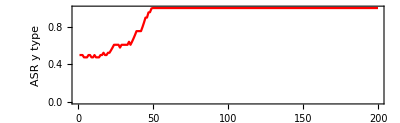

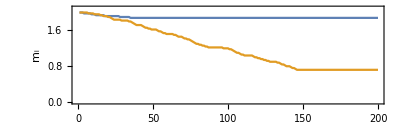

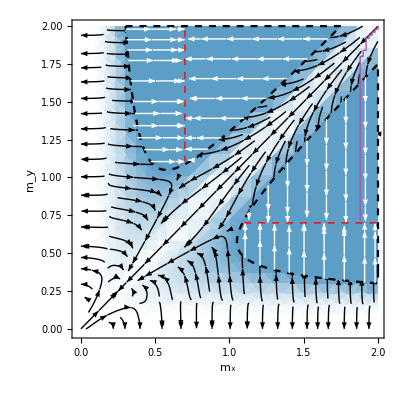

```mathematica
ListLinePlot[evoTraj[[All,{1,4}]],PlotRange->{0,1},AspectRatio->1/2 1/GoldenRatio,Frame->True,PlotStyle->Red,FrameStyle->12,FrameLabel->{Style["τ",16],Style["ASR y type",16]}]
ListLinePlot[{evoTraj[[All,{1,2}]],evoTraj[[All,{1,3}]]},PlotRange->{0,2.1},AspectRatio->1/2 1/GoldenRatio,Frame->True,FrameStyle->12,FrameLabel->{Style["τ",16],Style["m_i",16]}]

mycolorFunc=Blend[{White,ColorData[97,"ColorList"][[7]]},#]&;


Show[
DensityPlot[Eq8a/.params,{mx,0.02,2},{my,0.02,2},FrameLabel->{Style["m_x",16],Style["m_y",16],
Style["βz="<>ToString[N[βz/.params]]<>". βp="<>ToString[N[βp/.params]],20]},FrameStyle->12,PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

DensityPlot[Evaluate[Eq8a/.{mx->my,my->mx}/.params],{mx,0.02,2},{my,0.02,2},PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

StreamPlot[
{Eq9,Eq10}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my<mx],StreamStyle->Black
],

StreamPlot[
Evaluate[({Eq10,Eq9}/.{mx->my,my->mx})/.params],
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my>mx],StreamStyle->Black
],

(*ListPlot[{{0.28,0.28}},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],
ListPlot[{Last[Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]],Reverse[Last[Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]]]},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],*)

RegionPlot[(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0),{mx,0.02,2},{my,0.02,2},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

RegionPlot[Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)],{mx,0.02,2},{my,0.02,2},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

StreamPlot[
{0,Eq7/.m->my}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0)],StreamStyle->White
],

StreamPlot[
{Eq7/.m->mx,0}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)]],StreamStyle->White
],

Plot[βp/.params,{mx,1.1,2},PlotStyle->{Thick,Red,Dashed}],
Graphics[{Directive[{Thick,Red,Dashed}],Line[{{βp/.params,1.1},{βp/.params,2}}]}],

ListLinePlot[
Table[{Max[evoTraj[[i,2]],evoTraj[[i,3]]],Min[evoTraj[[i,2]],evoTraj[[i,3]]]},{i,1,Length[evoTraj]}]
,PlotRange->All,PlotStyle->{Lighter[Purple],Thick}]

]
```

### Sex ratios (for panel A1)

#### Loop - different my (panel A)

```mathematica
params1={ϕ->100,βz->1,βp->1,A->1000,M->1,f0->0,maxGen->200};
params2={ϕ->100,βz->1,βp->0.75,A->1000,M->1,f0->0,maxGen->200};
params3={ϕ->100,βz->1,βp->0.6,A->1000,M->1,f0->0,maxGen->200};
params4={ϕ->100,βz->1,βp->3,A->1000,M->1,f0->0,maxGen->200};

fyTable1PanelA=Table[{i,0},{i,0.1,1,0.1}];
fyTable2PanelA=Table[{i,0},{i,0.1,1,0.1}];
fyTable3PanelA=Table[{i,0},{i,0.1,1,0.1}];
fyTable4PanelA=Table[{i,0},{i,0.1,1,0.1}];

For[i=1,i≤Length[fyTable1PanelA],i++,

mParams={fs->0.51,δm->-0.1,mx->1,my->fyTable1[[i,1]]};

exTrajYMut=Quiet[invTrajYMut[mParams,params1]];
fyTable1PanelA[[i,2]]=1-(Last[exTrajYMut][[2]])/(Last[exTrajYMut][[2]]+Last[exTrajYMut][[3]]);

exTrajYMut=Quiet[invTrajYMut[mParams,params2]];
fyTable2PanelA[[i,2]]=1-(Last[exTrajYMut][[2]])/(Last[exTrajYMut][[2]]+Last[exTrajYMut][[3]]);

exTrajYMut=Quiet[invTrajYMut[mParams,params3]];
fyTable3PanelA[[i,2]]=1-(Last[exTrajYMut][[2]])/(Last[exTrajYMut][[2]]+Last[exTrajYMut][[3]]);

exTrajYMut=Quiet[invTrajYMut[mParams,params4]];
fyTable4PanelA[[i,2]]=1-(Last[exTrajYMut][[2]])/(Last[exTrajYMut][[2]]+Last[exTrajYMut][[3]]);

];
```

#### Loop - different βp (panel B)

```mathematica
mParams={fs->0.51,δm->-0.1,mx->1,my->0.8};

fyTable1PanelB=Table[{i,0},{i,0.1,2,0.1}];

For[i=1,i≤Length[fyTable1PanelB],i++,

params1={ϕ->100,βz->1,βp->fyTable1PanelB[[i,1]],A->1000,M->1,f0->0,maxGen->200};

exTrajYMut=Quiet[invTrajYMut[mParams,params1]];
fyTable1PanelB[[i,2]]=1-(Last[exTrajYMut][[2]])/(Last[exTrajYMut][[2]]+Last[exTrajYMut][[3]]);
];
```

## Figures

### Figure 2: Illustrative evolutionary trajectories

#### Panels A,C

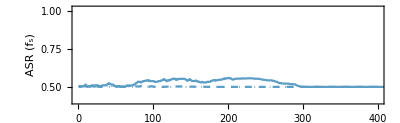

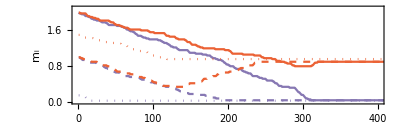

```mathematica
params={ϕ->100,βz->1,βg->0.7,g->1000,M->1,f0->10^-2,maxGen->10000,maxMut->500};

cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]}];

plotFig2PanelA=Show[
ListLinePlot[Table[{panelAevoTraj1[[i,1]],Abs[panelAevoTraj1[[i,4]]-0.5]+0.5},{i,1,Length[panelAevoTraj1]}],PlotRange->{{0,400},{0.4,1.02}},AspectRatio->1/2 1/GoldenRatio,Frame->True,PlotStyle->ColorData[97,"ColorList"][[7]],FrameStyle->12,FrameLabel->{Style["τ",16],Style["ASR (f_s)",16]}],
ListLinePlot[Table[{panelAevoTraj2[[i,1]],Abs[panelAevoTraj2[[i,4]]-0.5]+0.5},{i,1,Length[panelAevoTraj2]}],PlotStyle->{ColorData[97,"ColorList"][[7]],Dashed}],
ListLinePlot[Table[{panelAevoTraj3[[i,1]],Abs[panelAevoTraj3[[i,4]]-0.5]+0.5},{i,1,Length[panelAevoTraj3]}],PlotStyle->{ColorData[97,"ColorList"][[7]],Dotted}]
]

plotFig2PanelC=
Show[

ListLinePlot[{
Table[{panelAevoTraj1[[i,1]],Min[panelAevoTraj1[[i,2]],panelAevoTraj1[[i,3]]]},{i,1,Length[panelAevoTraj1]}],
Table[{panelAevoTraj1[[i,1]],Max[panelAevoTraj1[[i,2]],panelAevoTraj1[[i,3]]]},{i,1,Length[panelAevoTraj1]}]
},PlotRange->{{0,400},{0,2.1}},AspectRatio->1/2 1/GoldenRatio,Frame->True,FrameStyle->12,FrameLabel->{Style["τ",16],Style["m_i",16]},PlotStyle->{{ColorData[97,"ColorList"][[5]]},{ColorData[97,"ColorList"][[4]]}}],

ListLinePlot[{
Table[{panelAevoTraj2[[i,1]],Min[panelAevoTraj2[[i,2]],panelAevoTraj2[[i,3]]]},{i,1,Length[panelAevoTraj2]}],
Table[{panelAevoTraj2[[i,1]],Max[panelAevoTraj2[[i,2]],panelAevoTraj2[[i,3]]]},{i,1,Length[panelAevoTraj2]}]
},PlotStyle->{{Dashed,ColorData[97,"ColorList"][[5]]},{Dashed,ColorData[97,"ColorList"][[4]]}}],

ListLinePlot[{
Table[{panelAevoTraj3[[i,1]],Min[panelAevoTraj3[[i,2]],panelAevoTraj3[[i,3]]]},{i,1,Length[panelAevoTraj3]}],
Table[{panelAevoTraj3[[i,1]],Max[panelAevoTraj3[[i,2]],panelAevoTraj3[[i,3]]]},{i,1,Length[panelAevoTraj3]}]
},PlotStyle->{{Dotted,ColorData[97,"ColorList"][[5]]},{Dotted,ColorData[97,"ColorList"][[4]]}}]

]
```

#### Panels B,D

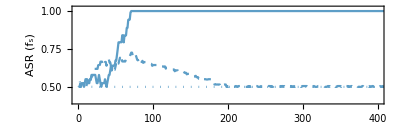

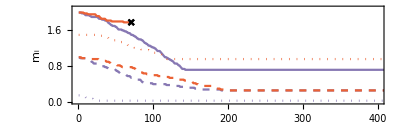

```mathematica
params={ϕ->100,βz->1,βg->0.7,g->1000,M->1,f0->10^-2,maxGen->10000,maxMut->500};

cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]}];

plotFig2PanelB=Show[
ListLinePlot[Table[{panelBevoTraj1[[i,1]],Abs[panelBevoTraj1[[i,4]]-0.5]+0.5},{i,1,Length[panelBevoTraj1]}],PlotRange->{{0,400},{0.4,1.02}},AspectRatio->1/2 1/GoldenRatio,Frame->True,PlotStyle->ColorData[97,"ColorList"][[7]],FrameStyle->12,FrameLabel->{Style["τ",16],Style["ASR (f_s)",16]}],
ListLinePlot[Table[{panelBevoTraj2[[i,1]],Abs[panelBevoTraj2[[i,4]]-0.5]+0.5},{i,1,Length[panelBevoTraj2]}],PlotStyle->{ColorData[97,"ColorList"][[7]],Dashed}],
ListLinePlot[Table[{panelBevoTraj3[[i,1]],Abs[panelBevoTraj3[[i,4]]-0.5]+0.5},{i,1,Length[panelBevoTraj3]}],PlotStyle->{ColorData[97,"ColorList"][[7]],Dotted}]
]

plotFig2PanelD=
Show[

ListLinePlot[{
Table[{panelBevoTraj1[[i,1]],Min[panelBevoTraj1[[i,2]],panelBevoTraj1[[i,3]]]},{i,1,Length[panelBevoTraj1]}],
Table[{panelBevoTraj1[[i,1]],Max[panelBevoTraj1[[i,2]],panelBevoTraj1[[i,3]]]},{i,1,(Flatten[Position[panelBevoTraj1[[All,4]],x_/;x<10^-3]][[1]])}]
},PlotRange->{{0,400},{0,2.1}},AspectRatio->1/2 1/GoldenRatio,Frame->True,FrameStyle->12,FrameLabel->{Style["τ",16],Style["m_i",16]},PlotStyle->{{ColorData[97,"ColorList"][[5]]},{ColorData[97,"ColorList"][[4]]}}],

ListPlot[{panelBevoTraj1[[(Flatten[Position[panelBevoTraj1[[All,4]],x_/;x<10^-3]][[1]])
,{1,2}]]},PlotMarkers->{cross,0.09},PlotStyle->Black],

ListLinePlot[{
Table[{panelBevoTraj2[[i,1]],Min[panelBevoTraj2[[i,2]],panelBevoTraj2[[i,3]]]},{i,1,Length[panelBevoTraj2]}],
Table[{panelBevoTraj2[[i,1]],Max[panelBevoTraj2[[i,2]],panelBevoTraj2[[i,3]]]},{i,1,Length[panelBevoTraj2]}]
},PlotStyle->{{Dashed,ColorData[97,"ColorList"][[5]]},{Dashed,ColorData[97,"ColorList"][[4]]}}],

ListLinePlot[{
Table[{panelBevoTraj3[[i,1]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}],
Table[{panelBevoTraj3[[i,1]],Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]
},PlotStyle->{{Dotted,ColorData[97,"ColorList"][[5]]},{Dotted,ColorData[97,"ColorList"][[4]]}}]

]
```

#### Legend

```mathematica
plotFig2Legend=SwatchLegend[{ColorData[97,"ColorList"][[7]],ColorData[97,"ColorList"][[5]],ColorData[97,"ColorList"][[4]]},{Style["Adult Sex Ratio (ASR)",18],Style["Microgamete Mass",18],Style["Macrogamete Mass",18]}]
```

### Figure 3: Fully Sexual / Fully Parthenogenic

#### Panel A

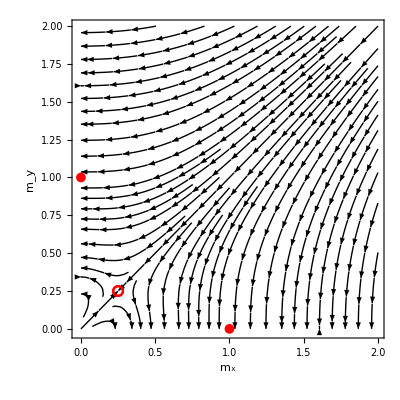

```mathematica
params={ϕ->100,βz->1,βp->10,A->1000,M->1,f0->10^-2,maxGen->5000,maxMut->150};

plotFig3PanelA=Quiet[
Show[
StreamPlot[
{Eq5,Eq6}/.params,
{mx,0,2},{my,0,2},
FrameLabel->{Style["m_x",16],Style["m_y",16],Style["Fully Sexual Rep.",20]},FrameStyle->12,PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},
StreamStyle->Black
],
ListPlot[{{0.25,0.25}},PlotMarkers->Graphics[{Red,Circle[]},ImageSize->10]],
ListPlot[{{0,1},{1,0}},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]]
]
]
```

#### Panel B

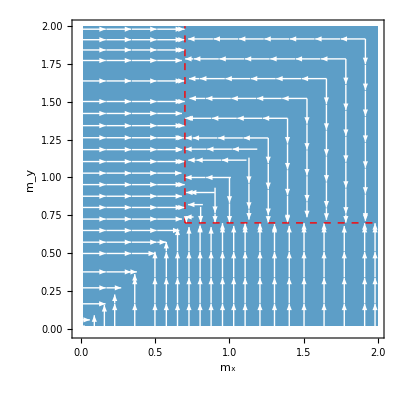

```mathematica
params={ϕ->100,βz->10,βp->0.7,g->1000,M->1,f0->10^-2,maxGen->5000,maxMut->150};
mycolorFunc=Blend[{White,ColorData[97,"ColorList"][[7]]},#]&;

plotFig3PanelB=Quiet[
Show[
DensityPlot[1,{mx,0.02,2},{my,0.02,2},FrameLabel->{Style["m_x",16],Style["m_y",16],Style["Fully Parthenogenic Rep.",20]},FrameStyle->12,PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],
StreamPlot[
{0,Eq7/.m->my}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my<mx],StreamStyle->White
],
StreamPlot[
Evaluate[{Eq7/.m->mx,0}/.params],
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my>mx],StreamStyle->White
],
Plot[βp/.params,{mx,βp/.params,2},PlotStyle->{Thick,Red,Dashed}],
Graphics[{Directive[{Thick,Red,Dashed}],Line[{{βp/.params,βp/.params},{βp/.params,2}}]}]
]
]
```

#### Legend

```mathematica
plotFig3Legend=BarLegend[{((mycolorFunc)[Rescale[#,{0.5,1}]]&),{0.5,1}}]
```

### Figure 4: Mixed Sexual/Asexual

#### Panel A

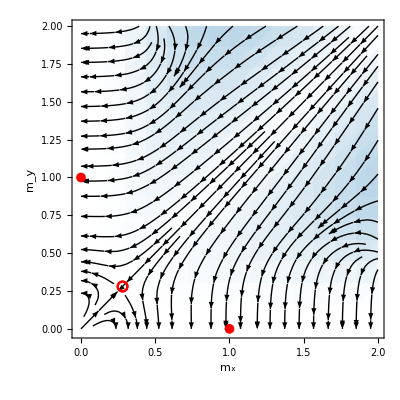

```mathematica
params={ϕ->100,βz->1,βp->1.3,g->1000,M->1,f0->10^-2,maxGen->5000,maxMut->150};
mycolorFunc=Blend[{White,ColorData[97,"ColorList"][[7]]},#]&;

plotFig4PanelA=Show[
DensityPlot[Eq8a/.params,{mx,0.02,2},{my,0.02,2},FrameLabel->{Style["m_x",16],Style["m_y",16],(*Style["β_z="<>ToString[βz/.params]<>", β_g="<>ToString[βp/.params],20]*)
Style["Parthenogenic Disadvantage",20]},FrameStyle->12,PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

DensityPlot[Evaluate[Eq8a/.{mx->my,my->mx}/.params],{mx,0.02,2},{my,0.02,2},PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

StreamPlot[
{Eq9,Eq10}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my<mx],StreamStyle->Black
],

StreamPlot[
Evaluate[({Eq10,Eq9}/.{mx->my,my->mx})/.params],
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my>mx],StreamStyle->Black
],
ListPlot[{{0.28,0.28}},PlotMarkers->Graphics[{Red,Circle[]},ImageSize->10]],
ListPlot[{{0,1},{1,0}},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]]
]
```

#### Panel B

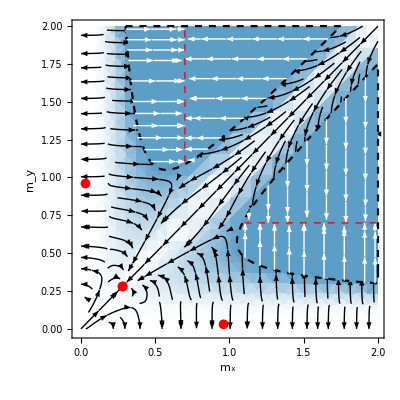

```mathematica
params={ϕ->100,βz->1,βp->0.7,A->1000,M->1,f0->10^-2,maxGen->5000,maxMut->150};
mycolorFunc=Blend[{White,ColorData[97,"ColorList"][[7]]},#]&;


plotFig4PanelB=Show[
DensityPlot[Eq8a/.params,{mx,0.02,2},{my,0.02,2},FrameLabel->{Style["m_x",16],Style["m_y",16],(*Style["β_z="<>ToString[βz/.params]<>", β_g="<>ToString[βp/.params],20]*)
Style["Parthenogenic Advantage",20]},FrameStyle->12,PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

DensityPlot[Evaluate[Eq8a/.{mx->my,my->mx}/.params],{mx,0.02,2},{my,0.02,2},PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

StreamPlot[
{Eq9,Eq10}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my<mx],StreamStyle->Black
],

StreamPlot[
Evaluate[({Eq10,Eq9}/.{mx->my,my->mx})/.params],
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my>mx],StreamStyle->Black
],

ListPlot[{{0.28,0.28}},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],
ListPlot[{Last[Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]],Reverse[Last[Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]]]},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],

RegionPlot[(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0),{mx,0.02,2},{my,0.02,2},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

RegionPlot[Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)],{mx,0.02,2},{my,0.02,2},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

StreamPlot[
{0,Eq7/.m->my}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0)],StreamStyle->White
],

StreamPlot[
{Eq7/.m->mx,0}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)]],StreamStyle->White
],

Plot[βp/.params,{mx,1.1,2},PlotStyle->{Thick,Red,Dashed}],
Graphics[{Directive[{Thick,Red,Dashed}],Line[{{βp/.params,1.1},{βp/.params,2}}]}]

]
```

#### Legend

```mathematica
plotFig4Legend=BarLegend[{((mycolorFunc)[Rescale[#,{0.5,1}]]&),{0.5,1}}]
```

### Figure 5: Asexual Invasion

#### Panel A

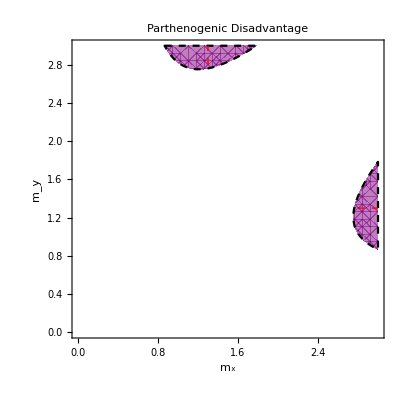

```mathematica
params1={βz->1,βp->1.3};

D1=Triangle[{{0,0},{2,0},{2,2}}];
D2=Triangle[{{0,0},{0,2},{2,2}}];

plotFig5PanelA=Show[
RegionPlot[{
Evaluate[(Evaluate[((mx>my)&&(Eq11>βp/.params1)/.{mx->my,my->mx})])||(Evaluate[((mx>my)&&(Eq11>βp/.params1))])],
Evaluate[(Evaluate[((mx>my)&&(Eq12>βp/.params1)/.{mx->my,my->mx})])||(Evaluate[((mx>my)&&(Eq12>βp/.params1))])]
},
{mx,0,3},{my,0,3},PlotStyle->{{Purple,Opacity[0.5]},{Orange,Opacity[0.5]}},FrameStyle->12,FrameLabel->{Style["m_x",16],Style["m_y",16]},BoundaryStyle->{Black,Dashed},
PlotLabel->(*Style["β_z=1, β_g=1.3",20]*)Style["Parthenogenic Disadvantage",20]
],

Plot[βp/.params1,{mx,2.8,3},PlotStyle->{Thick,Red,Dashed}],
Graphics[{Directive[{Thick,Red,Dashed}],Line[{{βp/.params1,2.8},{βp/.params1,3}}]}]
]
```

#### Panel B

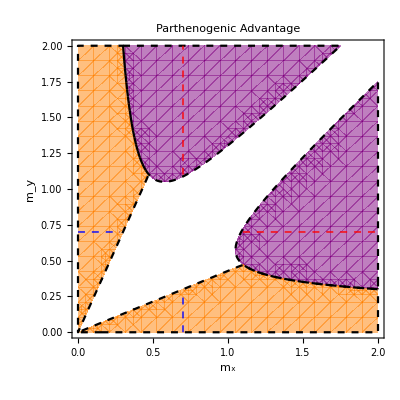

```mathematica
params2={βz->1,βg->0.7};

D1=Triangle[{{0,0},{2,0},{2,2}}];
D2=Triangle[{{0,0},{0,2},{2,2}}];

plotFig5PanelB=Show[
RegionPlot[{
Evaluate[(Evaluate[((mx>my)&&(Eq11>βg/.params2)/.{mx->my,my->mx})])||(Evaluate[((mx>my)&&(Eq11>βg/.params2))])],
Evaluate[(Evaluate[((mx>my)&&(Eq12>βg/.params2)&&(Eq11<βg/.params2)/.{mx->my,my->mx})])||(Evaluate[((mx>my)&&(Eq12>βg/.params2)&&(Eq11<βg/.params2))])]
},
{mx,0,2},{my,0,2},PlotStyle->{{Purple,Opacity[0.5]},{Orange,Opacity[0.5]}},FrameStyle->12,FrameLabel->{Style["m_x",16],Style["m_y",16]},BoundaryStyle->{Black,Dashed},
PlotLabel->Style["Parthenogenic Advantage",20](*Style["β_z=1, β_g=1.3",20]*)
],
Plot[βp/.params,{mx,1.1,2},PlotStyle->{Thick,Red,Dashed}],
Graphics[{Directive[{Thick,Red,Dashed}],Line[{{βp/.params,1.1},{βp/.params,2}}]}],

Plot[βp/.params,{mx,0,0.28},PlotStyle->{Thick,Blue,Dashed}],
Graphics[{Directive[{Thick,Blue,Dashed}],Line[{{βp/.params,0},{βp/.params,0.28}}]}]
]
```

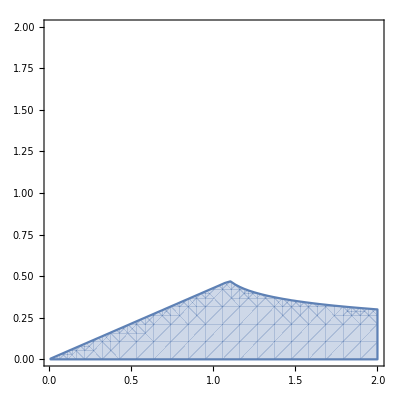

```mathematica
RegionPlot[(Eq12>βp>Eq11)/.params,{mx,0.01,2},{my,0,2}]
```

#### Legend

```mathematica
plotFig5Legend=SwatchLegend[{Purple,Orange},{Style["Asexual Microgamete invades",18],Style["Asexual Macrogamete Invades",18]}]
```

### Figure A1: Sex-ratio calc

#### Panel A

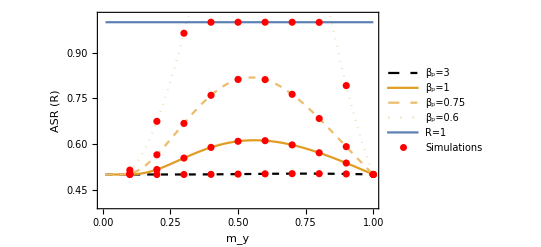

```mathematica
params1={mx->1,βz->1,βp->1};
params2={mx->1,βz->1,βp->0.75};
params3={mx->1,βz->1,βp->0.6};
params4={mx->1,βz->1,βp->3};

plotFigA1PanelA=Show[
Plot[Evaluate[
Join[
{Eq8a/.params4},
{Eq8a/.params1},
{Eq8a/.params2},
{Eq8a/.params3},
{1}
]
],{my,0.01,1},
PlotRange->{0.4,1.02},Frame->True,FrameLabel->{Style["m_y",16],Style["ASR (R)",16]},
PlotStyle->{
{Black,Dashed},
{ColorData[97,"ColorList"][[2]]},
{Lighter[ColorData[97,"ColorList"][[2]]],Dashed},
{Lighter[Lighter[ColorData[97,"ColorList"][[2]]]],Dotted},
{ColorData[97,"ColorList"][[1]]}
},PlotLegends->{"β_p=3","β_p=1","β_p=0.75","β_p=0.6","R=1"}
],
ListPlot[fyTable1PanelA,PlotStyle->Red,PlotLegends->{"Simulations"}],
ListPlot[fyTable2PanelA,PlotStyle->Red],
ListPlot[fyTable3PanelA,PlotStyle->Red],
ListPlot[fyTable4PanelA,PlotStyle->Red]
]
```

#### Panel B

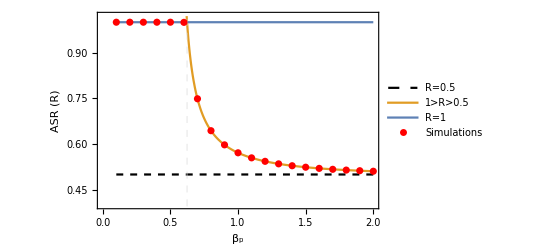

```mathematica
mParams={fs->0.51,δm->-0.1,mx->1,my->0.8};

plotFigA1PanelB=Show[
Plot[Evaluate[{
0.5,
Eq8a/.mParams/.βz->1,
Eq8b
}],{βp,0.1,2},PlotRange->{0.4,1.02},AxesOrigin->{0,-0.02},GridLines->{{my Log[(ⅇ^(βz/(mx+my)) mx)/my]/.params1/.mParams},{}},GridLinesStyle->Directive[{Thick,LightGray, Dashed}],Frame->True,FrameLabel->{Style["β_p",16],Style["ASR (R)",16]},PlotLegends->{"R=0.5","1>R>0.5","R=1"},
PlotStyle->{
{Black,Dashed},
{ColorData[97,"ColorList"][[2]]},
{ColorData[97,"ColorList"][[1]]}
}
],
ListPlot[fyTable1PanelB,PlotStyle->Red,PlotLegends->{"Simulations"}]
]
```

### Figure A2: Mixed Sexual/Asexual larger range

#### Panel A

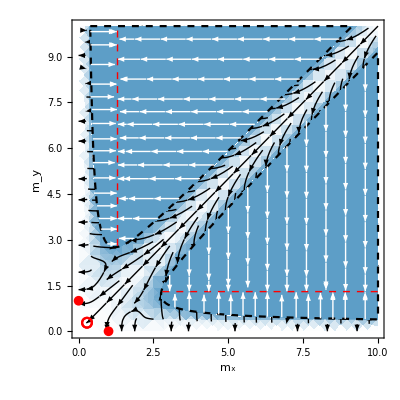

```mathematica
params={ϕ->100,βz->1,βp->1.3,g->1000,M->1,f0->10^-2,maxGen->5000,maxMut->150};
mycolorFunc=Blend[{White,ColorData[97,"ColorList"][[7]]},#]&;

plotFigA2PanelA=Show[
DensityPlot[Eq8a/.params,{mx,0.02,10},{my,0.02,10},FrameLabel->{Style["m_x",16],Style["m_y",16],(*Style["β_z="<>ToString[βz/.params]<>", β_g="<>ToString[βp/.params],20]*)
Style["Parthenogenic Disadvantage",20]},FrameStyle->12,PlotRange->{{-0.02,10},{-0.02,10},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

DensityPlot[Evaluate[Eq8a/.{mx->my,my->mx}/.params],{mx,0.02,10},{my,0.02,10},PlotRange->{{-0.02,10},{-0.02,10},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

StreamPlot[
{Eq9,Eq10}/.params,
{mx,0,10},{my,0,10},RegionFunction->Function[{mx,my},my<mx],StreamStyle->Black
],

StreamPlot[
Evaluate[({Eq10,Eq9}/.{mx->my,my->mx})/.params],
{mx,0,10},{my,0,10},RegionFunction->Function[{mx,my},my>mx],StreamStyle->Black
],
ListPlot[{{0.28,0.28}},PlotMarkers->Graphics[{Red,Circle[]},ImageSize->10]],
ListPlot[{{0,1},{1,0}},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],

RegionPlot[(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0),{mx,0.02,10},{my,0.02,10},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

RegionPlot[Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)],{mx,0.02,10},{my,0.02,10},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

StreamPlot[
{0,Eq7/.m->my}/.params,
{mx,0,10},{my,0,10},RegionFunction->Function[{mx,my},(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0)],StreamStyle->White
],

StreamPlot[
{Eq7/.m->mx,0}/.params,
{mx,0,10},{my,0,10},RegionFunction->Function[{mx,my},Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)]],StreamStyle->White
],

Plot[βp/.params,{mx,2.8,10},PlotStyle->{Thick,Red,Dashed}],
Graphics[{Directive[{Thick,Red,Dashed}],Line[{{βp/.params,2.8},{βp/.params,10}}]}]

]
```

#### Panel B

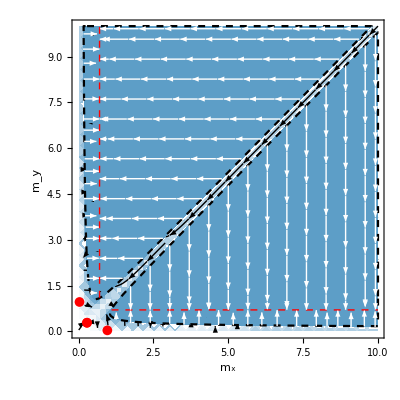

```mathematica
params={ϕ->100,βz->1,βp->0.7,A->1000,M->1,f0->10^-2,maxGen->5000,maxMut->150};
mycolorFunc=Blend[{White,ColorData[97,"ColorList"][[7]]},#]&;


plotFigA2PanelB=Show[
DensityPlot[Eq8a/.params,{mx,0.02,10},{my,0.02,10},FrameLabel->{Style["m_x",16],Style["m_y",16],(*Style["β_z="<>ToString[βz/.params]<>", β_g="<>ToString[βp/.params],20]*)
Style["Parthenogenic Advantage",20]},FrameStyle->12,PlotRange->{{-0.02,10},{-0.02,10},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

DensityPlot[Evaluate[Eq8a/.{mx->my,my->mx}/.params],{mx,0.02,10},{my,0.02,10},PlotRange->{{-0.02,10},{-0.02,10},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

StreamPlot[
{Eq9,Eq10}/.params,
{mx,0,10},{my,0,10},RegionFunction->Function[{mx,my},my<mx],StreamStyle->Black
],

StreamPlot[
Evaluate[({Eq10,Eq9}/.{mx->my,my->mx})/.params],
{mx,0,10},{my,0,10},RegionFunction->Function[{mx,my},my>mx],StreamStyle->Black
],

ListPlot[{{0.28,0.28}},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],
ListPlot[{Last[Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]],Reverse[Last[Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]]]},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],

RegionPlot[(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0),{mx,0.02,10},{my,0.02,10},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

RegionPlot[Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)],{mx,0.02,10},{my,0.02,10},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

StreamPlot[
{0,Eq7/.m->my}/.params,
{mx,0,10},{my,0,10},RegionFunction->Function[{mx,my},(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0)],StreamStyle->White
],

StreamPlot[
{Eq7/.m->mx,0}/.params,
{mx,0,10},{my,0,10},RegionFunction->Function[{mx,my},Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)]],StreamStyle->White
],

Plot[βp/.params,{mx,1.1,10},PlotStyle->{Thick,Red,Dashed}],
Graphics[{Directive[{Thick,Red,Dashed}],Line[{{βp/.params,1.1},{βp/.params,10}}]}]

]
```

#### Legend

```mathematica
plotFigA2Legend=BarLegend[{((mycolorFunc)[Rescale[#,{0.5,1}]]&),{0.5,1}}]
```

### Figure A3: Mixed Sexual/Asexual with stochastic trajectories overlaid

#### Panel A

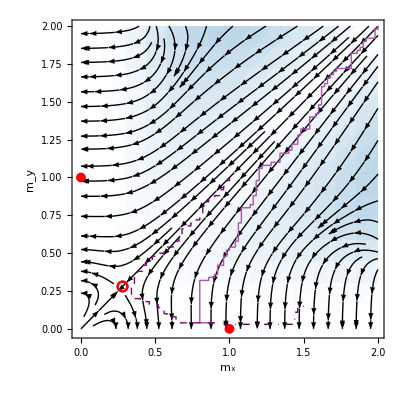

```mathematica
params={ϕ->100,βz->1,βp->1.3,g->1000,M->1,f0->10^-2,maxGen->5000,maxMut->150};
mycolorFunc=Blend[{White,ColorData[97,"ColorList"][[7]]},#]&;

plotFigA3PanelA=Show[
DensityPlot[Eq8a/.params,{mx,0.02,2},{my,0.02,2},FrameLabel->{Style["m_x",16],Style["m_y",16],(*Style["β_z="<>ToString[βz/.params]<>", β_g="<>ToString[βp/.params],20]*)
Style["Parthenogenic Disadvantage",20]},FrameStyle->12,PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

DensityPlot[Evaluate[Eq8a/.{mx->my,my->mx}/.params],{mx,0.02,2},{my,0.02,2},PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

StreamPlot[
{Eq9,Eq10}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my<mx],StreamStyle->Black
],

StreamPlot[
Evaluate[({Eq10,Eq9}/.{mx->my,my->mx})/.params],
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my>mx],StreamStyle->Black
],
ListPlot[{{0.28,0.28}},PlotMarkers->Graphics[{Red,Circle[]},ImageSize->10]],
ListPlot[{{0,1},{1,0}},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],

ListLinePlot[
Table[{Max[panelAevoTraj1[[i,2]],panelAevoTraj1[[i,3]]],Min[panelAevoTraj1[[i,2]],panelAevoTraj1[[i,3]]]},{i,1,Length[panelAevoTraj1]}]
,PlotRange->All,PlotStyle->{Lighter[Purple],Thick}],

ListLinePlot[
Table[{Max[panelAevoTraj2[[i,2]],panelAevoTraj2[[i,3]]],Min[panelAevoTraj2[[i,2]],panelAevoTraj2[[i,3]]]},{i,1,Length[panelAevoTraj2]}]
,PlotRange->All,PlotStyle->{Purple,Dashed,Thick}],

ListLinePlot[
Table[{Max[panelAevoTraj3[[i,2]],panelAevoTraj3[[i,3]]],Min[panelAevoTraj3[[i,2]],panelAevoTraj3[[i,3]]]},{i,1,Length[panelAevoTraj3]}]
,PlotRange->All,PlotStyle->{Darker[Purple],DotDashed,Thick}]


]
```

#### Panel B

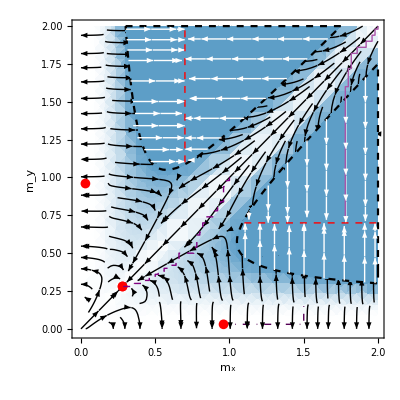

```mathematica
params={ϕ->100,βz->1,βp->0.7,A->1000,M->1,f0->10^-2,maxGen->5000,maxMut->150};
mycolorFunc=Blend[{White,ColorData[97,"ColorList"][[7]]},#]&;


plotFigA3PanelB=Show[
DensityPlot[Eq8a/.params,{mx,0.02,2},{my,0.02,2},FrameLabel->{Style["m_x",16],Style["m_y",16],(*Style["β_z="<>ToString[βz/.params]<>", β_g="<>ToString[βp/.params],20]*)
Style["Parthenogenic Advantage",20]},FrameStyle->12,PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

DensityPlot[Evaluate[Eq8a/.{mx->my,my->mx}/.params],{mx,0.02,2},{my,0.02,2},PlotRange->{{-0.02,2},{-0.02,2},{0.5,1}},ColorFunctionScaling->False,ColorFunction->((mycolorFunc)[Rescale[#,{0.5,1}]]&)],

StreamPlot[
{Eq9,Eq10}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my<mx],StreamStyle->Black
],

StreamPlot[
Evaluate[({Eq10,Eq9}/.{mx->my,my->mx})/.params],
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},my>mx],StreamStyle->Black
],

ListPlot[{{0.28,0.28}},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],
ListPlot[{Last[Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]],Reverse[Last[Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]]]},PlotMarkers->Graphics[{Red,Disk[]},ImageSize->10]],

RegionPlot[(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0),{mx,0.02,2},{my,0.02,2},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

RegionPlot[Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)],{mx,0.02,2},{my,0.02,2},PlotStyle->ColorData[97,"ColorList"][[7]],BoundaryStyle->{Black,Dashed}],

StreamPlot[
{0,Eq7/.m->my}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},(mx>my)&&((Eq8a/.params)>1||(Eq8a/.params)<0)],StreamStyle->White
],

StreamPlot[
{Eq7/.m->mx,0}/.params,
{mx,0,2},{my,0,2},RegionFunction->Function[{mx,my},Evaluate[((Evaluate[(Eq8a/.{mx->my,my->mx}/.params)>1])||(Evaluate[(Eq8a/.{mx->my,my->mx}/.params)<0]))&&(mx<my)]],StreamStyle->White
],

Plot[βp/.params,{mx,1.1,2},PlotStyle->{Thick,Red,Dashed}],
Graphics[{Directive[{Thick,Red,Dashed}],Line[{{βp/.params,1.1},{βp/.params,2}}]}],

ListLinePlot[
Table[{Max[panelBevoTraj1[[i,2]],panelBevoTraj1[[i,3]]],Min[panelBevoTraj1[[i,2]],panelBevoTraj1[[i,3]]]},{i,1,Length[panelBevoTraj1]}]
,PlotRange->All,PlotStyle->{Lighter[Purple],Thick}],

ListLinePlot[
Table[{Max[panelBevoTraj2[[i,2]],panelBevoTraj2[[i,3]]],Min[panelBevoTraj2[[i,2]],panelBevoTraj2[[i,3]]]},{i,1,Length[panelBevoTraj2]}]
,PlotRange->All,PlotStyle->{Purple,Dashed,Thick}],

ListLinePlot[
Table[{Max[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]],Min[panelBevoTraj3[[i,2]],panelBevoTraj3[[i,3]]]},{i,1,Length[panelBevoTraj3]}]
,PlotRange->All,PlotStyle->{Darker[Purple],DotDashed,Thick}]

]
```

#### Legend

```mathematica
plotFigA3Legend=BarLegend[{((mycolorFunc)[Rescale[#,{0.5,1}]]&),{0.5,1}}]
```